## Broken verision

#### LIPS out of COM

```mathematica
Clear[M2]
dΠLIPS=dΩ/(16 π^2) kD/Ei /.Ei ->p + mD
dΠi = (nD g)/(mD p)     (dp  p^2)/(8 π^2)1/(E^(β p)+1)
Integrand = Simplify[Simplify[dΠLIPS dΠi M2 Et]]
```

(dΩ kD)/(16 (mD+p) π^2)

(dp g nD p)/(8 (1+ⅇ^(p β)) mD π^2)

(d^2 dp dΩ g kD M2 nD p^3)/(64 (1+ⅇ^(p β)) (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

Mandelstam variables

```mathematica
s = Simplify[(mD + p)^2 - p^2]
t = Simplify[(Et)^2 - q^2]
u = FullSimplify[(Ef - mD)^2-Ef^2]
```

mD (mD+2 p)

-(4 d^2 mD^2 p^2)/(mD^2+2 mD p-(-1+d^2) p^2)

(mD (mD^3+3 (-1+d^2) mD p^2+2 (-1+d^2) p^3))/((mD+p-d p) (mD+p+d p))

```mathematica
Et
```

(2 d^2 mD p^2)/(-d^2 p^2+(mD+p)^2)

```mathematica
M2lD =FullSimplify[(8 e^2 eD^2 ϵ^2)/t^2((s/2)^2+(u/2)^2)] (*lepton dark matter scattering*)
```

(e^2 eD^2 (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2)/(4 d^4 mD^2 p^4)

```mathematica
Integrand/.M2->M2lD
```

(dp dΩ e^2 eD^2 g kD nD (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2)/(256 d^2 (1+ⅇ^(p β)) mD^2 p (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

```mathematica
Integrate[Integrand,d]
```

(dp dΩ g kD M2 nD (-2 d p-(mD+p) Log[-mD+(-1+d) p]+(mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) (mD+p) π^4)

```mathematica
Simplify[2 π/dΩ Integrate[Integrand/.M2->M2lD,d]]
FullSimplify[((%/.d->1)-(%/.d->-1))/mD^2]
```

(dp e^2 eD^2 g kD nD ϵ^2 (-((mD+p)^2 (mD^2+4 p^2))/d-d p^2 (5 mD^2+8 mD p+4 p^2)-4 mD^2 p (mD+p) Log[mD+p-d p]+4 mD^2 p (mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) mD^2 p (mD+p) π^3)

-(dp e^2 eD^2 g kD nD ϵ^2 (mD^4+2 mD^3 p+10 mD^2 p^2+16 mD p^3+8 p^4+4 mD^2 p (mD+p) (Log[mD]-Log[mD+2 p])))/(64 (1+ⅇ^(p β)) mD^4 p (mD+p) π^3)

#### cross-section squared

```mathematica
Simplify[s/(2 t)]
FullSimplify[%/.p->mD pt]
```

-((mD+2 p) (mD^2+2 mD p-(-1+d^2) p^2))/(8 d^2 mD p^2)

((1+2 pt) (-1+(-1+d) pt) (1+pt+d pt))/(8 d^2 pt^2)

```mathematica
FullSimplify[u/(2 t)]
FullSimplify[%/.p->mD pt]
```

-(mD^3+3 (-1+d^2) mD p^2+2 (-1+d^2) p^3)/(8 d^2 mD p^2)

-(1+(-1+d^2) pt^2 (3+2 pt))/(8 d^2 pt^2)

```mathematica
IntegrandΓ=FullSimplify[1/(E^(p β)+1)Et/d ((u/(2 t))^2+(s/(2 t))^2)/.{p->mD ξ}]
Integrate[IntegrandΓ,d]
```

(mD (-1+ξ (-4+ξ (-10+2 d^2 (1+ξ)^2 (-1+4 ξ (1+ξ))-d^4 ξ^2 (5+4 ξ (2+ξ))-ξ (20+ξ (25+4 ξ (4+ξ)))))))/(16 d^3 (1+ⅇ^(mD β ξ)) ξ^2 (-1+(-1+d) ξ) (1+ξ+d ξ))

(mD (-((1+ξ)^2 (1+4 ξ^2))/(2 d^2)+ξ^2 (3-8 ξ-4 ξ^2) Log[d]-4 ξ^2 Log[1+ξ-d ξ]-4 ξ^2 Log[1+ξ+d ξ]))/(16 (1+ⅇ^(mD β ξ)) ξ^2)

```mathematica
Integrate[IntegrandΓ,{d,-1,1}]
```

Integrate::idiv: Integral of (mD (-1+ξ (-4+ξ (-10+2 Power[«2»] Power[«2»] Plus[«2»]-Power[«2»] Power[«2»] Plus[«2»]-ξ Plus[«2»]))))/(16 d^3 (1+ⅇ^(mD β ξ)) ξ^2 (-1+(-1+d) ξ) (1+ξ+d ξ)) does not converge on {-1,1}.

∫_-1^1 (mD (-1+ξ (-4+ξ (-10+2 d^2 (1+ξ)^2 (-1+4 ξ (1+ξ))-d^4 ξ^2 (5+4 ξ (2+ξ))-ξ (20+ξ (25+4 ξ (4+ξ)))))))/(16 d^3 (1+ⅇ^(mD β ξ)) ξ^2 (-1+(-1+d) ξ) (1+ξ+d ξ))ⅆd

```mathematica
IntegrandΓ=FullSimplify[1/(E^(p β)+1)Et^2/d ((u/(2 t))^2+(s/(2 t))^2)/.{p->mD ξ}]
Integrate[IntegrandΓ,d]
```

(mD^2 (1+ξ (4+ξ (10-2 d^2 (1+ξ)^2 (-1+4 ξ (1+ξ))+d^4 ξ^2 (5+4 ξ (2+ξ))+ξ (20+ξ (25+4 ξ (4+ξ)))))))/(8 d (1+ⅇ^(mD β ξ)) (1+ξ (2+ξ-d^2 ξ))^2)

1/(8 (1+ⅇ^(mD β ξ)))mD^2 (-(4 (1+ξ)^2)/(-1-2 ξ+(-1+d^2) ξ^2)+(1+4 ξ^2) Log[d]+2 (1+2 ξ) Log[1+2 ξ+ξ^2-d^2 ξ^2])

```mathematica
Integrate[IntegrandΓ,{d,-1,1}]
```

Integrate::idiv: Integral of (mD^2 (1+ξ (4+ξ (10-2 Power[«2»] Power[«2»] Plus[«2»]+Power[«2»] Power[«2»] Plus[«2»]+ξ Plus[«2»]))))/(8 d (1+ⅇ^(mD β ξ)) (1+ξ (2+ξ-d^2 ξ))^2) does not converge on {-1,1}.

∫_-1^1 ((mD^2 (1+ξ (4+ξ (10-2 d^2 (1+ξ)^2 (-1+4 ξ (1+ξ))+d^4 ξ^2 (5+4 ξ (2+ξ))+ξ (20+ξ (25+4 ξ (4+ξ)))))))/(8 d (1+ⅇ^(mD β ξ)) (1+ξ (2+ξ-d^2 ξ))^2))ⅆd

```mathematica
Simplify[(2^4 kD p^2 nD g 4 π)/(Eitotal 16 π^2(2π)^3 2 mD 2 E)]
```

(g kD nD p^2)/(8 ⅇ Eitotal mD π^4)

#### Get k_D (q) - massive case

```mathematica
Clear[q]
qsol = Solve[mD + √(p^2+m^2) == √(mD^2 + q^2) + √(p^2 - 2 p d q + q^2 + m^2),q][[2]]
q = Simplify[q/.qsol]
Simplify[PowerExpand[Limit[q,m->0]]]==qless
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{q→(2 (-d m^2 mD^2 p+d mD^4 p-d mD^2 p^3-d^3 mD^2 p^3+d m^2 mD p √(m^2+p^2)-d mD^3 p √(m^2+p^2)+d mD p^3 √(m^2+p^2)-d^3 mD p^3 √(m^2+p^2)))/(m^4-2 m^2 mD^2+mD^4+2 m^2 p^2-2 d^2 m^2 p^2-2 mD^2 p^2-2 d^2 mD^2 p^2+p^4-2 d^2 p^4+d^4 p^4)}

-(2 d mD p (-mD^3+(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)+m^2 (mD-√(m^2+p^2))))/(m^4+mD^4-2 (1+d^2) mD^2 p^2+(-1+d^2)^2 p^4-2 m^2 (mD^2+(-1+d^2) p^2))

True

Compute E transfered

```mathematica
Clear[d]
Ef = FullSimplify[√(p^2 - 2 q d p +q^2+m^2)/.qsol]
Et =FullSimplify[√(mD^2 + q^2)-mD/.qsol]
ESM = √(p^2+m^2)
Ei = ESM + mD
```

√(m^2+p^2+(4 d^2 mD^2 p^2 (-mD^3+(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)+m^2 (mD-√(m^2+p^2)))^2)/((m^2-mD^2)^2-2 ((-1+d^2) m^2+(1+d^2) mD^2) p^2+(-1+d^2)^2 p^4)^2+(4 d^2 mD p^2 (m^2-mD^2+p^2))/(mD^3-(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)-m^2 (mD+√(m^2+p^2))))

-mD+√(mD^2 (1+(4 d^2 p^2 (-mD^3+(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)+m^2 (mD-√(m^2+p^2)))^2)/((m^2-mD^2)^2-2 ((-1+d^2) m^2+(1+d^2) mD^2) p^2+(-1+d^2)^2 p^4)^2))

√(m^2+p^2)

mD+√(m^2+p^2)

compare SM final state energy to massless case

```mathematica
PowerExpand[Simplify[PowerExpand[Limit[Ef,m->0]]] ]
Simplify[%-Efless]
```

ConditionalExpression[(p (mD^2-2 (-1+d^2) mD p-(-1+d^2) p^2))/(mD^2+2 mD p-(-1+d^2) p^2), ]

ConditionalExpression[0, ]

compare energy transfered to massless case

```mathematica
Simplify[PowerExpand[Simplify[PowerExpand[Limit[Et,m->0]]]]]
Simplify[%-Etless]
```

ConditionalExpression[(2 d^2 mD p^2)/(mD^2+2 mD p-(-1+d^2) p^2), ]

ConditionalExpression[0, ]

```mathematica
Limit[Et,d->0]
Limit[Ef,d->0]
```

-mD+√(mD^2)

√(m^2+p^2)

```mathematica
s=Simplify[(mD + ESM)^2-p^2] (*p + pD squared*)
t = Simplify[ (Et)^2- q^2](*kD - pD squared*)
(*u = Simplify[(Ef-mD)^2-√(Ef^2-m^2)](*k - pD squared*)*)
u = Simplify[(Ef-mD)^2-(Ef^2-m^2)](*k - pD squared*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(mD^2 (1+(4 d^2 p^2 (-mD^3+(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)+m^2 (mD-√(m^2+p^2)))^2)/(((m^2-mD^2)^2-2 ((-1+d^2) m^2+(1+d^2) mD^2) p^2+(-1+d^2)^2 p^4)^2))))

m^2+mD^2-2 mD √(m^2+p^2+(4 d^2 mD^2 p^2 (-mD^3+(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)+m^2 (mD-√(m^2+p^2)))^2)/(((m^2-mD^2)^2-2 ((-1+d^2) m^2+(1+d^2) mD^2) p^2+(-1+d^2)^2 p^4)^2)+(4 d^2 mD p^2 (m^2-mD^2+p^2))/(mD^3-(1+d^2) mD p^2+mD^2 √(m^2+p^2)+(-1+d^2) p^2 √(m^2+p^2)-m^2 (mD+√(m^2+p^2))))

```mathematica
Simplify[PowerExpand[Limit[q,m->0]]]
```

-(2 d mD p (mD+p))/(-mD^2-2 mD p+(-1+d^2) p^2)

s

```mathematica
PowerExpand[Limit[s,m->0]]
```

mD (mD+2 p)

t

```mathematica
Simplify[PowerExpand[Simplify[Limit[t,m->0]]]]
```

ConditionalExpression[-2 mD^2 (-1+√(((mD^2+2 mD p+(1+d^2) p^2)^2)/((mD^2+2 mD p-(-1+d^2) p^2)^2))), ]

```mathematica
Simplify[PowerExpand[√(((mD^2+2 mD p+(1+d^2) p^2)^2)/((mD^2+2 mD p-(-1+d^2) p^2)^2))]-1]
```

(2 d^2 p^2)/(mD^2+2 mD p-(-1+d^2) p^2)

No take non-relativistic limits

```mathematica
Simplify[PowerExpand[Series[q/.p->m ξ,{ξ,0,2}]]]
```

(2 d m mD ξ)/(m+mD)+O[ξ]^3

```mathematica
Simplify[PowerExpand[Series[Et/.p->m ξ,{ξ,0,2}]]]
```

(2 d^2 m^2 mD ξ^2)/(m+mD)^2+O[ξ]^3

```mathematica
Simplify[PowerExpand[Series[Ef/.p->m ξ,{ξ,0,2}]]]
```

m+(m (m^2+(2-4 d^2) m mD+mD^2) ξ^2)/(2 (m+mD)^2)+O[ξ]^3

```mathematica
Simplify[PowerExpand[Series[ESM/.p->m ξ,{ξ,0,2}]]]
```

m+(m ξ^2)/2+O[ξ]^3

```mathematica
Simplify[PowerExpand[Series[s/.p->m ξ,{ξ,0,2}]]]
```

(m+mD)^2+m mD ξ^2+O[ξ]^3

```mathematica
Simplify[PowerExpand[Series[t/.p->m ξ,{ξ,0,2}]]]
```

-(4 (d^2 m^2 mD^2) ξ^2)/(m+mD)^2+O[ξ]^3

this is -2 Et

```mathematica
Simplify[PowerExpand[Series[u/.p->m ξ,{ξ,0,2}]]]
```

(m-mD)^2-(m mD (m^2+(2-4 d^2) m mD+mD^2) ξ^2)/(m+mD)^2+O[ξ]^3

Second term is - 2 mD(Ef-m)

#### scrapp

u

```mathematica
PowerExpand[Limit[u,m->0]]
Simplify[%]
```

ConditionalExpression[mD^2-2 mD p √(1+(4 d^2 mD (-mD^2+p^2))/(mD^3+mD^2 p-(1+d^2) mD p^2+(-1+d^2) p^3)+(4 d^2 mD^2 (-mD^3+mD^2 p+(1+d^2) mD p^2+(-1+d^2) p^3)^2)/((mD^4-2 (1+d^2) mD^2 p^2+(-1+d^2)^2 p^4)^2)), ]

ConditionalExpression[mD (mD-2 p √(((mD^2-2 (-1+d^2) mD p-(-1+d^2) p^2)^2)/((mD^2+2 mD p-(-1+d^2) p^2)^2))), ]

```mathematica
Simplify[PowerExpand[Limit[(Ef-mD)^2-√(Ef^2-m^2),m->0]]]
```

ConditionalExpression[-p √(((mD^2-2 (-1+d^2) mD p-(-1+d^2) p^2)^2)/((mD^2+2 mD p-(-1+d^2) p^2)^2))+(mD-p √(((mD^2-2 (-1+d^2) mD p-(-1+d^2) p^2)^2)/((mD^2+2 mD p-(-1+d^2) p^2)^2)))^2, ]

#### Massive case - in momentum variables

compute q and compare to massless case

```mathematica
Clear[θsol,d]
θsol = Solve[mD + √(p^2+m^2) == √(mD^2 + kD^2) + √(p^2 - 2 p d kD + kD^2 + m^2),d][[1]]
d= Simplify[d/.θsol]
PowerExpand[Series[d,{kD,0,1}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{d→1/(kD p)(-mD^2+mD √(kD^2+mD^2)-mD √(m^2+p^2)+√(kD^2+mD^2) √(m^2+p^2))}

((-mD+√(kD^2+mD^2)) (mD+√(m^2+p^2)))/(kD p)

((mD+√(m^2+p^2)) kD)/(2 mD p)+O[kD]^2

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

Compute E transfered

```mathematica
(*Ef = FullSimplify[√(p^2 - 2 kD d p +kD^2+m^2)/.θsol]*)
Ef = FullSimplify[mD +√(p^2+m^2) - √(mD^2 + kD^2)]
Et =FullSimplify[√(mD^2 + kD^2)-mD]
ESM = √(p^2+m^2)
Ei = ESM + mD
```

mD-√(kD^2+mD^2)+√(m^2+p^2)

-mD+√(kD^2+mD^2)

√(m^2+p^2)

mD+√(m^2+p^2)

```mathematica
Simplify[Expand[(ESMt + mD)^2/(ESMt^2-m^2) -1]]
```

(m^2+2 ESMt mD+mD^2)/(ESMt^2-m^2)

```mathematica
s=Simplify[(mD + ESM)^2-p^2] (*p + pD squared*)
t = Simplify[ (Et)^2- kD^2](*kD - pD squared*)
(*u = Simplify[(Ef-mD)^2-√(Ef^2-m^2)](*k - pD squared*)*)
u = Simplify[(Ef-mD)^2-(Ef^2-m^2)](*k - pD squared*)
```

m^2+mD (mD+2 √(m^2+p^2))

2 mD (mD-√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2-mD^2+2mD Ei](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+3mD^2+2mD (Et-Ei)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2+mD^2+2mD ESM](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+mD^2+2mD (Et-ESM)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[u+t+s]
```

2 (m^2+mD^2)

```mathematica
(s/t)^2+(u/t)^2
FullSimplify[%]
```

((m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2)))^2)/(4 mD^2 (mD-√(kD^2+mD^2))^2)+((m^2+mD (mD+2 √(m^2+p^2)))^2)/(4 mD^2 (mD-√(kD^2+mD^2))^2)

((m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2)))^2+(m^2+mD (mD+2 √(m^2+p^2)))^2)/(4 mD^2 (mD-√(kD^2+mD^2))^2)

```mathematica
s/t
```

(m^2+mD (mD+2 √(m^2+p^2)))/(2 mD (mD-√(kD^2+mD^2)))

```mathematica
Expand[s^2+u^2]
```

2 m^4+4 kD^2 mD^2+8 m^2 mD^2+6 mD^4+4 m^2 mD √(kD^2+mD^2)-4 mD^3 √(kD^2+mD^2)+8 mD^2 p^2+8 mD^3 √(m^2+p^2)-8 mD^2 √(kD^2+mD^2) √(m^2+p^2)

```mathematica
p/.Solve[ESMt ==ESM,p][[2]]
D[%,ESMt]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

√(ESMt^2-m^2)

ESMt/(√(ESMt^2-m^2))

```mathematica
Solve[Et==Ett,kD]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kD→-√Ett √(Ett+2 mD)},{kD→√Ett √(Ett+2 mD)}}

```mathematica
Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%]
Simplify[(%%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%%/.Ett->Λ)]
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt)%,ESMt]
FullintApproxnonTherm = Integrate[%%,ESMt];
```

-2 ESMt Ett+Ett^2/2+2 Ett ms+2 ESMt^2 Log[Ett]+2 ms^2 Log[Ett]

1/2 Ett (-4 ESMt+Ett+4 ms)+2 (ESMt^2+ms^2) Log[Ett]

((-2 ESMt^2 mD+2 ESMt mD Λ+mD^2 Λ+m^2 (2 mD+Λ)) (4 ESMt m^2+6 ESMt^2 mD+m^2 (2 mD-4 ms-Λ)+2 ESMt mD (2 mD-4 ms-Λ)-mD^2 (4 ms+Λ)))/(2 (m^2+mD (2 ESMt+mD))^2)+2 (ESMt^2+ms^2) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))]-2 (ESMt^2+ms^2) Log[Λ]

1/32 ((128 ⅇ^(-m β) m (ExpIntegralEi[(-ESMt+m) β]-ⅇ^(2 m β) ExpIntegralEi[-((ESMt+m) β)]))/β^2+(128 ⅇ^(-m β) (ExpIntegralEi[(-ESMt+m) β]+ⅇ^(2 m β) ExpIntegralEi[-((ESMt+m) β)]))/β^3+(64 ⅇ^(-m β) m^2 (ExpIntegralEi[(-ESMt+m) β]+ⅇ^(2 m β) ExpIntegralEi[-((ESMt+m) β)]))/β+(64 ⅇ^(-m β) ms^2 (ExpIntegralEi[(-ESMt+m) β]+ⅇ^(2 m β) ExpIntegralEi[-((ESMt+m) β)]))/β-32 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 ms ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]+(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^4 ms ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/mD^2+16 ⅇ^(((m^2+mD^2) β)/(2 mD)) mD^2 ms ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]-(128 ⅇ^(((m^2+mD^2) β)/(2 mD)) ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/β^3+(64 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/(mD β^2)+(64 ⅇ^(((m^2+mD^2) β)/(2 mD)) mD ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/β^2-(32 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/β-(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^4 ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/(mD^2 β)-(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) mD^2 ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/β-(64 ⅇ^(((m^2+mD^2) β)/(2 mD)) ms^2 ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)])/β+(6 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^4 (-2 ⅇ^(-((m^2+mD (2 ESMt+mD)) β)/(2 mD)) mD-(m^2+mD (2 ESMt+mD)) β ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]))/(m^2+mD (2 ESMt+mD))+(ⅇ^(((m^2+mD^2) β)/(2 mD)) m^8 (-2 ⅇ^(-((m^2+mD (2 ESMt+mD)) β)/(2 mD)) mD-(m^2+mD (2 ESMt+mD)) β ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]))/(mD^4 (m^2+mD (2 ESMt+mD)))+(ⅇ^(((m^2+mD^2) β)/(2 mD)) mD^4 (-2 ⅇ^(-((m^2+mD (2 ESMt+mD)) β)/(2 mD)) mD-(m^2+mD (2 ESMt+mD)) β ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]))/(m^2+mD (2 ESMt+mD))+(4 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^6 (2 ⅇ^(-((m^2+mD (2 ESMt+mD)) β)/(2 mD)) mD+(m^2+mD (2 ESMt+mD)) β ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]))/(mD^2 (m^2+mD (2 ESMt+mD)))+(4 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 mD^2 (2 ⅇ^(-((m^2+mD (2 ESMt+mD)) β)/(2 mD)) mD+(m^2+mD (2 ESMt+mD)) β ExpIntegralEi[-((m^2+mD (2 ESMt+mD)) β)/(2 mD)]))/(m^2+mD (2 ESMt+mD))-(64 ⅇ^(-ESMt β) (2+2 ESMt β+ESMt^2 β^2+ms^2 β^2) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))])/β^3+1/(mD^2 β^3)4 ⅇ^(-ESMt β) (m^4 β^2+mD^4 β^2-4 m^2 mD β (3+ESMt β-2 ms β)-4 mD^3 β (3+ESMt β-2 ms β)+2 mD^2 (-12+6 ESMt^2 β^2-3 m^2 β^2-8 β Λ+2 β^2 Λ^2+8 ms β (-1+β Λ)-4 ESMt β (-1+2 ms β+2 β Λ))+16 mD^2 (2+2 ESMt β+ESMt^2 β^2+ms^2 β^2) Log[Λ]))

```mathematica
Simplify[FullintApproxTherm /.{ESMt->m+Λ,ms->(m^2+mD^2)/(2 mD)}]
(*Series[%/.Λ->β ξ,{ξ,0,1}]*)
```

1/32 ((128 ⅇ^(-m β) m (ExpIntegralEi[-β Λ]-ⅇ^(2 m β) ExpIntegralEi[-β (2 m+Λ)]))/β^2+(128 ⅇ^(-m β) (ExpIntegralEi[-β Λ]+ⅇ^(2 m β) ExpIntegralEi[-β (2 m+Λ)]))/β^3+(64 ⅇ^(-m β) m^2 (ExpIntegralEi[-β Λ]+ⅇ^(2 m β) ExpIntegralEi[-β (2 m+Λ)]))/β+(16 ⅇ^(-m β) (m^2+mD^2)^2 (ExpIntegralEi[-β Λ]+ⅇ^(2 m β) ExpIntegralEi[-β (2 m+Λ)]))/(mD^2 β)+(8 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^4 (m^2+mD^2) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/mD^3-(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 (m^2+mD^2) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/mD+8 ⅇ^(((m^2+mD^2) β)/(2 mD)) mD (m^2+mD^2) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]-(128 ⅇ^(((m^2+mD^2) β)/(2 mD)) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/β^3+(64 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/(mD β^2)+(64 ⅇ^(((m^2+mD^2) β)/(2 mD)) mD ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/β^2-(32 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/β-(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^4 ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/(mD^2 β)-(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) mD^2 ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/β-(16 ⅇ^(((m^2+mD^2) β)/(2 mD)) (m^2+mD^2)^2 ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)])/(mD^2 β)+(6 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^4 (-2 ⅇ^(-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)) mD-β (m^2+mD (mD+2 (m+Λ))) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]))/(m^2+mD (mD+2 (m+Λ)))+(ⅇ^(((m^2+mD^2) β)/(2 mD)) m^8 (-2 ⅇ^(-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)) mD-β (m^2+mD (mD+2 (m+Λ))) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]))/(mD^4 (m^2+mD (mD+2 (m+Λ))))+(ⅇ^(((m^2+mD^2) β)/(2 mD)) mD^4 (-2 ⅇ^(-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)) mD-β (m^2+mD (mD+2 (m+Λ))) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]))/(m^2+mD (mD+2 (m+Λ)))+(4 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^6 (2 ⅇ^(-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)) mD+β (m^2+mD (mD+2 (m+Λ))) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]))/(mD^2 (m^2+mD (mD+2 (m+Λ))))+(4 ⅇ^(((m^2+mD^2) β)/(2 mD)) m^2 mD^2 (2 ⅇ^(-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)) mD+β (m^2+mD (mD+2 (m+Λ))) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]))/(m^2+mD (mD+2 (m+Λ)))+1/(mD^2 β^3)4 ⅇ^(-β (m+Λ)) (5 m^4 β^2+5 mD^4 β^2-4 m^2 mD β (5+3 m β+β Λ)-4 mD^3 β (5+3 m β+β Λ)+2 mD^2 (7 m^2 β^2+4 m β (1+β Λ)-4 (3+β Λ))+4 (m^4 β^2+mD^4 β^2+mD^2 (8+6 m^2 β^2+8 β Λ+4 β^2 Λ^2+8 m β (1+β Λ))) Log[Λ])-(64 ⅇ^(-β (m+Λ)) (2+((m^2+mD^2)^2 β^2)/(4 mD^2)+2 β (m+Λ)+β^2 (m+Λ)^2) Log[(2 mD Λ (2 m+Λ))/(m^2+2 m mD+mD (mD+2 Λ))])/β^3)

```mathematica
Limit[FullintApproxnonTherm,ESMt -> ∞]
Simplify[FullintApproxnonTherm/.{ESMt->m+Λ,ms->(m^2+mD^2)/(2 mD)}/.mD->m]
```

∞

1/18 (-67 m^3-90 m^2 Λ-27 m Λ^2-4 Λ^3+96 m^3 ArcTanh[(m+Λ)/m]-48 m^3 Log[2 m (2 m+Λ)])

```mathematica
Simplify[PowerExpand[Simplify[Solve[(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1)==Λ,ESMt]/.mD->m]]]
```

{{ESMt→-m},{ESMt→m+Λ}}

```mathematica
Limit[FullintApproxTherm,ESMt -> ∞]
```

ConditionalExpression[0, ]

```mathematica
Simplify[FullintApproxTherm/.mD->m ]
```

1/(2 β^3)ⅇ^(-((ESMt+m) β)) (4 ⅇ^(ESMt β) (2+2 m β+m^2 β^2+ms^2 β^2) ExpIntegralEi[(-ESMt+m) β]+ⅇ^(m β) (-6+2 ESMt β-6 m β-4 ms β+3 ESMt^2 β^2-2 ESMt m β^2-m^2 β^2-4 ESMt ms β^2+4 m ms β^2-4 β Λ-4 ESMt β^2 Λ+4 ms β^2 Λ+β^2 Λ^2-4 (2+2 ESMt β+ESMt^2 β^2+ms^2 β^2) Log[ESMt-m]+4 (2+2 ESMt β+ESMt^2 β^2+ms^2 β^2) Log[Λ]))

```mathematica
ExpIntegralEi[0]
```

-∞

```mathematica
FullintApproxTherm/.ESMt->m + ESMt;
Limit[%,ESMt -> 0]
```

Indeterminate

```mathematica
Simplify[FullintApproxTherm/.{ESMt->m+Λ,ms->(m^2+mD^2)/(2 mD)}/.mD->m]
```

(ⅇ^(-β (m+Λ)) (-3-4 m β-β Λ+4 ⅇ^(β Λ) (1+m β+m^2 β^2) ExpIntegralEi[-β Λ]))/β^3

```mathematica
Series[ExpIntegralEi[x],{x,∞,6}]//Normal
```

ⅇ^x (120/x^6+24/x^5+6/x^4+2/x^3+1/x^2+1/x)+1/2 (Log[-1/x]-Log[-x]+2 Log[x])

```mathematica
Series[ExpIntegralEi[x],{x,-∞,6}]//Normal
```

ⅇ^x (120/x^6+24/x^5+6/x^4+2/x^3+1/x^2+1/x)+1/2 (Log[-1/x]-Log[1/x]-Log[-x]+Log[x])

```mathematica
Simplify[FullintApproxTherm/.{ms->(m^2+mD^2)/(2 mD)}];
Limit[%,ESMt->∞]
```

ConditionalExpression[0, ]

```mathematica
Simplify[Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]]
Simplify[Integrate[1/Ett^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]]
```

1/2 Ett (-4 ESMt+Ett+4 ms)+2 (ESMt^2+ms^2) Log[Ett]

(-2 ESMt^2+Ett^2-2 ms^2+2 Ett (-ESMt+ms) Log[Ett])/Ett

```mathematica
Simplify[Solve[(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1)==Ett,ESMt]]
```

{{ESMt→(Ett mD-√(mD (Ett+2 mD) (2 m^2+Ett mD)))/(2 mD)},{ESMt→(Ett mD+√(mD (Ett+2 mD) (2 m^2+Ett mD)))/(2 mD)}}

ℏ c == 200 MeV fm
so 1/m = 200 10^-15  10^6 eV

```mathematica
2.5 10^8(200 10^-15 10^6)^3 
ne = % 2.5 10^8
```

2.×10^-12

0.0005

```mathematica
0.0005/((1/(2 π)0.5 10^6 T)^(3/2))
%^-1
%^(2/3)
```

(2.22733×10^-11)/T^(3/2)

4.48968×10^10 T^(3/2)

1.26321×10^7 (T^(3/2))^(2/3)

```mathematica
Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)/.mD->m]
Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->Λ)]/.mD->m]
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt + β μ)%,ESMt]
```

-2 ESMt Ett+Ett^2/2+2 Ett ms+2 ESMt^2 Log[Ett]+2 ms^2 Log[Ett]

1/2 Ett (-4 ESMt+Ett+4 m)+2 (ESMt^2+m^2) Log[Ett]

-3/2 (ESMt-m)^2-1/2 Λ (-4 ESMt+4 m+Λ)+2 (ESMt^2+m^2) Log[ESMt-m]-2 (ESMt^2+m^2) Log[Λ]

1/(2 β^3)ⅇ^(β (-ESMt+μ)) (-6+2 ESMt β-10 m β+3 ESMt^2 β^2-6 ESMt m β^2+3 m^2 β^2-4 β Λ-4 ESMt β^2 Λ+4 m β^2 Λ+β^2 Λ^2+8 ⅇ^((ESMt-m) β) (1+m β+m^2 β^2) ExpIntegralEi[(-ESMt+m) β]-4 (2+2 ESMt β+ESMt^2 β^2+m^2 β^2) Log[ESMt-m]+8 Log[Λ]+8 ESMt β Log[Λ]+4 ESMt^2 β^2 Log[Λ]+4 m^2 β^2 Log[Λ])

```mathematica
Simplify[FullintApproxTherm/.ESMt->m+Λ]
%/.μ->m
%/.Λ -> β^-1 ξ 
Simplify[Series[%,{ξ,0,1}]]
```

(ⅇ^(-β (m+Λ-μ)) (-3-4 m β-β Λ+4 ⅇ^(β Λ) (1+m β+m^2 β^2) ExpIntegralEi[-β Λ]))/β^3

(ⅇ^(-β Λ) (-3-4 m β-β Λ+4 ⅇ^(β Λ) (1+m β+m^2 β^2) ExpIntegralEi[-β Λ]))/β^3

(ⅇ^-ξ (-3-4 m β-ξ+4 ⅇ^ξ (1+m β+m^2 β^2) ExpIntegralEi[-ξ]))/β^3

Floor[Arg[ξ]/(2 π)] (-(4 ⅈ π (1+m β+m^2 β^2))/β^3+O[ξ]^2)+Floor[-Arg[ξ]/(2 π)] ((4 ⅈ π (1+m β+m^2 β^2))/β^3+O[ξ]^2)+(1/β^3(-3+4 EulerGamma-4 m β+4 EulerGamma m β+4 EulerGamma m^2 β^2+4 Log[ξ]+4 m β Log[ξ]+4 m^2 β^2 Log[ξ])-(2 (1+2 m^2 β^2) ξ)/β^3+O[ξ]^2)

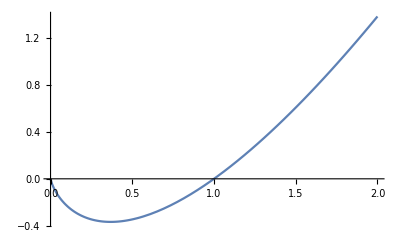

```mathematica
Plot[x Log[x],{x,0,2}]
```

#### Make Plots

```mathematica
Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)/.mD->m]
Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->Λ)]/.mD->m]
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt + β μ)%,ESMt]
Simplify[FullintApproxTherm/.ESMt->m+Λ]
meqmDreduced=%/.μ->m
```

-2 ESMt Ett+Ett^2/2+2 Ett ms+2 ESMt^2 Log[Ett]+2 ms^2 Log[Ett]

1/2 Ett (-4 ESMt+Ett+4 m)+2 (ESMt^2+m^2) Log[Ett]

-3/2 (ESMt-m)^2-1/2 Λ (-4 ESMt+4 m+Λ)+2 (ESMt^2+m^2) Log[ESMt-m]-2 (ESMt^2+m^2) Log[Λ]

1/(2 β^3)ⅇ^(β (-ESMt+μ)) (-6+2 ESMt β-10 m β+3 ESMt^2 β^2-6 ESMt m β^2+3 m^2 β^2-4 β Λ-4 ESMt β^2 Λ+4 m β^2 Λ+β^2 Λ^2+8 ⅇ^((ESMt-m) β) (1+m β+m^2 β^2) ExpIntegralEi[(-ESMt+m) β]-4 (2+2 ESMt β+ESMt^2 β^2+m^2 β^2) Log[ESMt-m]+8 Log[Λ]+8 ESMt β Log[Λ]+4 ESMt^2 β^2 Log[Λ]+4 m^2 β^2 Log[Λ])

1/β^3 ⅇ^(-β (m+Λ-μ)) (-3-4 m β-β Λ+4 ⅇ^(β Λ) (1+m β+m^2 β^2) ExpIntegralEi[-β Λ])

1/β^3 ⅇ^(-β Λ) (-3-4 m β-β Λ+4 ⅇ^(β Λ) (1+m β+m^2 β^2) ExpIntegralEi[-β Λ])

```mathematica
me= 5 10^5;
Xe = 0.01;
na = 5 10^-4;(*eV^3*)
ne = Xe na;
α = 1/137;
ΛDB = 4 π α (2 π ne β)/me;
prefactor= 2/π α^2;
```

```mathematica
ΛDB
```

5.76327×10^-12 β

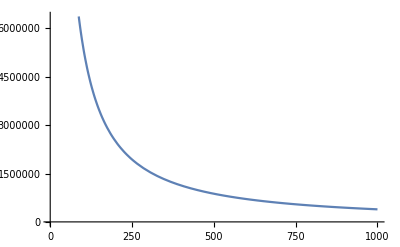

```mathematica
Plot[-prefactor meqmDreduced/.{m->me,Λ->ΛDB},{β,1,1000}]
```

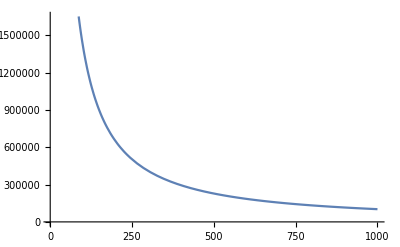

```mathematica
Plot[-prefactor 1/β m^2 Log[Abs[β Λ]]/.{m->me,Λ->ΛDB},{β,1,1000}]
```

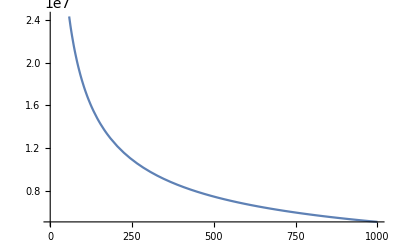

```mathematica
Plot[-prefactor 1/β m^2 Log[Abs[β Λ]]/.{m->me,Λ->ΛDB}/.β->a^(1/2),{a,1,1000}]
```

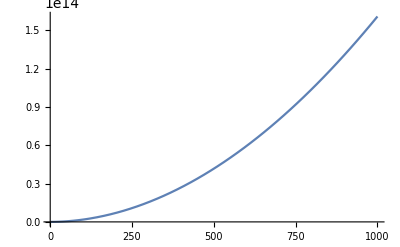

```mathematica
Plot[-a^(5/2)prefactor 1/β m^2 Log[Abs[β Λ]]/.{m->me,Λ->ΛDB}/.β->a^(1/2),{a,1,1000}]
```

ℏ c == 200 MeV fm
so 1/m = 200 10^-15  10^6 eV

```mathematica
1==eVm  200 10^-15 10^6
```

True

```mathematica
na0m = 0.25; (*m^{-3}*)
na0 = na0m  (200 10^-15 10^6)^3(*eV^3*)
```

2.×10^-21

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11}

```mathematica
2.5 10^8(200 10^-15 10^6)^3 
ne = % 2.5 10^8
```

2.×10^-12

0.0005

```mathematica
0.0005/((1/(2 π)0.5 10^6 T)^(3/2))
%^-1
%^(2/3)
```

(2.22733×10^-11)/T^(3/2)

4.48968×10^10 T^(3/2)

1.26321×10^7 (T^(3/2))^(2/3)

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0eVinv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0eV = H0eVinv^-1 (*eV*)
T0eV = 0.24 10^-3(*eV*)
β0 = T0eV^-1(*eV^-1*)
T0eV/H0eV
a0=1;
```

1.51515×10^-33

0.00024

4166.67

1.584×10^29

```mathematica
eVs=((3 10^8)/eVm)^-1(*eV s*)
```

1/60

```mathematica
me= 5 10^5;
Xe0 = 0.01;
(*na = 5 10^-4;(*eV^3*)*)
ne0 = Xe0 na0;
α = 1/137;
ΛDB0 = 4 π α (2 π ne0)/(me T0eV);
prefactor= 2/π α^2;
```

```mathematica
T0eV a/.Solve[(β0 ΛDB0) a^4==1,a][[4]] (*[eV] a is T/Subscript[T, 0] so this is T in eV such that we can no longer expand in β Λ*)
```

53.658

```mathematica
(g 4 π)/(2 π)^3 Integrate[p^2 E^(-β(m + p^2/(2 m) - μ)),{p,0,∞}]
```

ConditionalExpression[(ⅇ^(β (-m+μ)) g)/(2 √2 π^(3/2) (β/m)^(3/2)), Re[β/m]>0]

-Graphics-

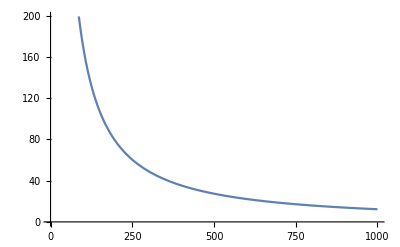

```mathematica
Plot[-T0eV/(a0 H0eV) prefactor  m Log[Abs[β Λ]]/.{m->me,Λ->ΛDB},{β,10^-5,1000}] (*per particle per scale factor*)
Plot[-prefactor/eVs 1/β m Log[Abs[β Λ]]/.{m->me,Λ->ΛDB},{β,10^-5,1000}] (*per particle per s *)
```

-Graphics-

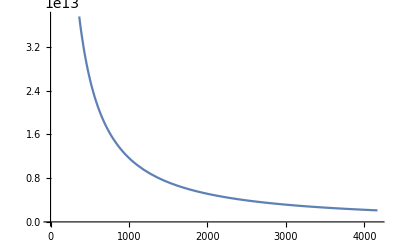

```mathematica
Plot[-T0eV/(a0 H0eV) β prefactor  m meqmDreduced/.{m->me,Λ->ΛDB},{β,10^-5,1/T0eV}] (*per particle per scale factor*)
Plot[-prefactor/eVs  m  meqmDreduced/.{m->me,Λ->ΛDB},{β,10^-5,1/T0eV}] (*per particle per s *)
```

```mathematica
Plot[-T0eV/(a0 H0eV) β prefactor  m meqmDreduced/.{m->me,Λ->ΛDB},{β,10^-5,1/(1000T0eV)}] (*per particle per scale factor*)
Plot[-prefactor/eVs  m  meqmDreduced/.{m->me,Λ->ΛDB},{β,10^-5,1/(1000T0eV)}] (*per particle per s *)
```

-Graphics-

-Graphics-

```mathematica
Plot[-prefactor/eVs  m  meqmDreduced/.{m->me,Λ->ΛDB},{β,10^-5,1/(1000T0eV)},PlotRange->All]
```

-Graphics-

```mathematica
Solve[T a^2== T0,a]
```

{{a→-(√T0)/(√T)},{a→(√T0)/(√T)}}

```mathematica
N[5 10^5 (2 10^9)^-2]
```

1.25×10^-13

```mathematica
0.25 2 10^-12
```

5.×10^-13

## Cleaner version

#### Constants and thermo dynamics

Temperature at decoupling

```mathematica
Td = 5 10^5; (*[eV] decoupling temperature*)
ad =(2 10^9)^-1; (*[] scale factor (~1/z) at decoupling*)
Tdt = N[Td ad^2]; (*[eV] \tilde{T}_d the projected / extrapolated electron bath temperature today - if recombination / reionization etc. never happened*)
aR = (1100)^-1;(*[] scale factor ~ 1/z at recombination*)
TR = Tdt/aR^2; (*[eV] temperature at recombination*)
```

```mathematica
TR
```

1.5125×10^-7

density today (and at decoupling)

```mathematica
Clear[ne]
n0 = 5 10^-13; (*[eV^3] number density today*)
ne[β_]:= n0(1/(β Tdt))^(3/2)
nd = n0 (Td/Tdt)^(3/2)
((2 π)^(3/2)nd)/(me Td)^(3/2)
```

4.×10^15

(1.78186×10^8)/me^(3/2)

```mathematica
ne[1/TR]
```

0.0006655

```mathematica
ndm = nd 5 10^13
Td
```

2.×10^29

500000

Thermal Quantities

```mathematica
me = 5 10^5; (*[eV] electron mass*)
pth =( (me Tdt)/(2 π))^(1/2); (*[eV] thermal de-broglie momentum*)
Q = pth^3/n0(*[] whether classical is good or not*)
kF = N[(3 π^2 n0)^(1/3)] (*[eV] fermi momentum today*)
EF = kF^2/(2 me)
EFd = EF Td/Tdt (*[eV]fermi energy at decoupling*)
Degen = EF/Tdt (*Degeneracy of gas today - degeneracy is independent of time*)
```

1.98418

0.000245545

6.02921×10^-14

241169.

0.482337

Notice, fermi energy is about m/2. This is kinda interesting, numerology or dynamic?

fine structure constant

```mathematica
α=1/137;
```

Debeye Cutoff

```mathematica
Λ[β_]:= 4 π α (2π n0)/(me (Tdt β)^(3/2))
```

```mathematica
1/Td Λ[1/Td]
1/Tdt Λ[1/Tdt]
10^-5/TR Λ[10^-5/TR]
```

9221.24

4.61062×10^-6

1.60381

```mathematica
1/Td
10^-5/TR
```

1/500000

66.1157

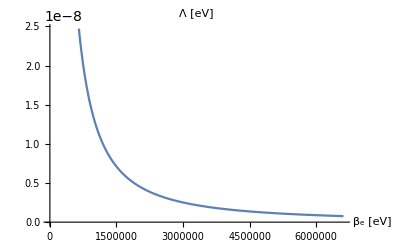

```mathematica
Plot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

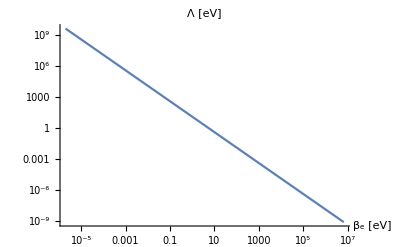

```mathematica
LogLogPlot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

### m=mD case - between decoupling and recombination - non-degenerate / classical limit

#### energy transfered per unit time - COMMENTED

assuming m=mD

```mathematica
(*Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)/.mD->m]
Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->Λ)]/.mD->m]
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt + β μ)%,ESMt]
Simplify[FullintApproxTherm/.ESMt->m+Λ]
meqmDreduced=%/.μ->m
*)
```

not assuming m=mD ---- XXXXXXXXXXXXX wrong can’t use m+Λ for m neq mD

```mathematica
(*Clear[m]
Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett];
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->Λ)]];
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt + β μ)%,ESMt];
Simplify[FullintApproxTherm/.ESMt->m+Λ];
mneqmDreduced=Simplify[%/.μ->m + 1/β Log[n ((2π β)/m)^(3/2)]]*)
```

1/(8 √2 mD^4 β^3)n π^(3/2) (β/m)^(3/2) (16 mD^2 (m^4 β^2+mD^4 β^2+mD^2 (8+8 m β+6 m^2 β^2)) ExpIntegralEi[-β Λ]+16 ⅇ^(2 m β) mD^2 (m^4 β^2+mD^4 β^2+mD^2 (8-8 m β+6 m^2 β^2)) ExpIntegralEi[-β (2 m+Λ)]-ⅇ^(((m+mD)^2 β)/(2 mD)) (-8 m^6 mD β^3-8 mD^7 β^3+m^8 β^4+mD^8 β^4+8 m^2 mD^3 β (-8+m^2 β^2)+8 mD^5 β (-8+m^2 β^2)-4 m^4 mD^2 β^2 (-8+m^2 β^2)-4 mD^6 β^2 (-8+m^2 β^2)+2 mD^4 (64+32 m^2 β^2+3 m^4 β^4)) ExpIntegralEi[-(β (m^2+mD (mD+2 (m+Λ))))/(2 mD)]-1/(m^2+mD (mD+2 (m+Λ)))2 ⅇ^(-β Λ) mD (48 m^2 mD^3+48 mD^5+40 m^4 mD^2 β+80 m^2 mD^4 β+40 mD^6 β-10 m^6 mD β^2-14 m^4 mD^3 β^2-14 m^2 mD^5 β^2-10 mD^7 β^2+m^8 β^3-4 m^6 mD^2 β^3+6 m^4 mD^4 β^3-4 m^2 mD^6 β^3+mD^8 β^3+32 m^2 mD^3 β Λ+32 mD^5 β Λ-16 m^4 mD^2 β^2 Λ-32 m^2 mD^4 β^2 Λ-16 mD^6 β^2 Λ-8 m^2 mD^3 β^2 Λ^2-8 mD^5 β^2 Λ^2+96 mD^4 (m+Λ)+64 m^2 mD^3 β (m+Λ)+64 mD^5 β (m+Λ)+4 m^4 mD^2 β^2 (m+Λ)+40 m^2 mD^4 β^2 (m+Λ)+4 mD^6 β^2 (m+Λ)+64 mD^4 β Λ (m+Λ)-16 mD^4 β^2 Λ^2 (m+Λ)-32 mD^4 β (m+Λ)^2+24 m^2 mD^3 β^2 (m+Λ)^2+24 mD^5 β^2 (m+Λ)^2+64 mD^4 β^2 Λ (m+Λ)^2-48 mD^4 β^2 (m+Λ)^3-8 mD (m^2+mD (mD+2 (m+Λ))) (m^4 β^2+mD^4 β^2+2 mD^2 (4+m^2 β^2+4 β (m+Λ)+2 β^2 (m+Λ)^2)) Log[Λ]+8 mD (m^2+mD (mD+2 (m+Λ))) (m^4 β^2+mD^4 β^2+2 mD^2 (4+m^2 β^2+4 β (m+Λ)+2 β^2 (m+Λ)^2)) Log[(2 mD Λ (2 m+Λ))/(m^2+2 m mD+mD (mD+2 Λ))]))

```mathematica
(*meqmDreduced =PowerExpand[Simplify[mneqmDreduced/.mD->m]]
Normal[Series[%/.Λ->1/β ξ,{ξ,∞,1}]]*)
```

1/(m^(3/2) β^(3/2))2 √2 ⅇ^(-β Λ) n π^(3/2) (-3-4 m β-β Λ+4 ⅇ^(β Λ) (1+m β+m^2 β^2) ExpIntegralEi[-β Λ])

ⅇ^-ξ ((2 √2 n π^(3/2) (-3-4 m β))/(m^(3/2) β^(3/2))-(8 √2 n π^(3/2) (1+m β+m^2 β^2))/(m^(3/2) β^(3/2) ξ)-(2 √2 n π^(3/2) ξ)/(m^(3/2) β^(3/2)))-1/(m^(3/2) β^(3/2))4 √2 n π^(3/2) (1+m β+m^2 β^2) (Log[-1/ξ]-Log[-ξ]+2 Log[ξ])

General::munfl: Exp[-1425.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1432.56] is too small to represent as a normalized machine number; precision may be lost.

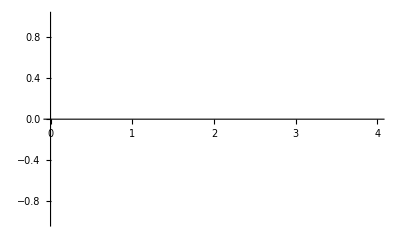

```mathematica
(*meqmDreduced/.{Λ->Λ[β],n->n0};
dEdtdND =- 2/π(α^2 κ^2)/me%/.κ->1;
Plot[dEdtdND,{β,1/me,1/TR}]*)
```

#### compute hubble to convert to per a

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0inv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0= H0inv^-1 (*eV*)
```

1.51515×10^-33

```mathematica
ΛCDMrepl= {Ωk ->0.01,Ωr->9.4 10^-5, Ωm->0.32,ΩΛ->0.68}; (*[] ΛCDM density parameters*)
H[β_] :=H0(Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)/.ΛCDMrepl/.a->(Tdt β)^(1/2)
aH[β_] :=a H0 (Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)/.ΛCDMrepl/.a->(Tdt β)^(1/2)
```

(3.22269×10^-18+3.87879×10^-21 √β+4.2855×10^-29 β+3.64267×10^-40 β^2)/β^(3/2)

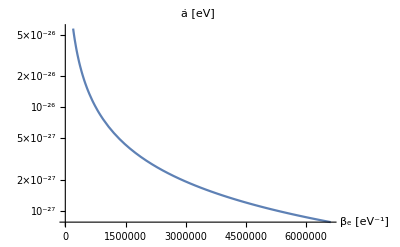

```mathematica
Simplify[aH[β]]
LogPlot[aH[β],{β,1/Td,1/TR},PlotLabel->"ȧ [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

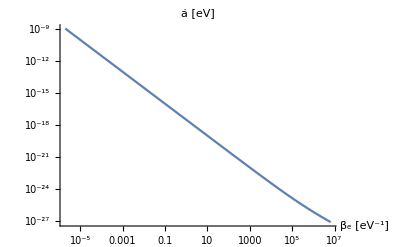

```mathematica
LogLogPlot[aH[β],{β,1/Td,1/TR},PlotLabel->"ȧ [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

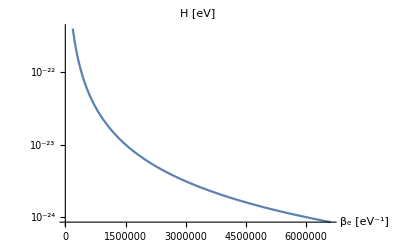

```mathematica
LogPlot[H[β],{β,1/Td,1/TR},PlotLabel->"H [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

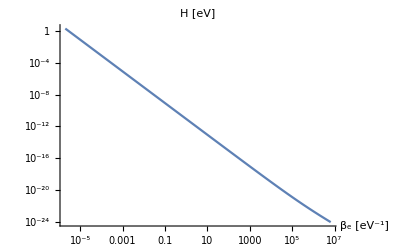

```mathematica
LogLogPlot[H[β],{β,1/Td,1/TR},PlotLabel->"H [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

#### Compare hubble and screening lengths - shows we can work in minkowski space

Screening energy - minimum energy transfered

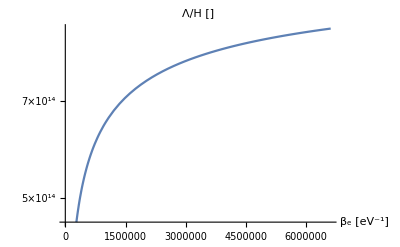

```mathematica
LogPlot[Λ[β]/H[β],{β,1/Td,1/TR},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

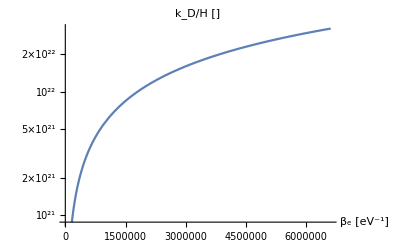

```mathematica
LogPlot[(√(2 me Λ[β]))/H[β],{β,1/Td,1/TR},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

#### Energy transfered per a - m=mD case - COMMENTED

General::munfl: Exp[-1425.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1432.56] is too small to represent as a normalized machine number; precision may be lost.

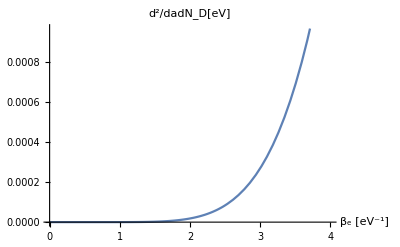

```mathematica
(*(*dEdadND =- 2/π(α^2 κ^2)/m%/.κ->1;*)
Plot[dEdtdND/aH[β],{β,1/Td,1/TR},PlotLabel->"d^2/dadN_D[eV]",AxesLabel->{"β_e [eV^-1]"}]*)
```

```mathematica
(*Td*)
```

500000

#### m neq mD case - before ne fix

Find cutoff energy - screening

```mathematica
Clear[m]
Solve[Λ==(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1),ESMt]
Simplify[%]
(*Simplify[PowerExpand[Simplify[%%/.mD->m]]]*)
Emin = ESMt/.%[[2]]
```

{{ESMt→(mD Λ-√(4 m^2 mD^2+2 m^2 mD Λ+2 mD^3 Λ+mD^2 Λ^2))/(2 mD)},{ESMt→(mD Λ+√(4 m^2 mD^2+2 m^2 mD Λ+2 mD^3 Λ+mD^2 Λ^2))/(2 mD)}}

{{ESMt→(mD Λ-√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD)},{ESMt→(mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD)}}

(mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD)

integrate to find expression for energy transfer rates

```mathematica
Clear[m]
Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett];
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->Λ)]];
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt + β μ)%,ESMt];
Simplify[FullintApproxTherm/.ESMt->Emin];
mneqmDreduced=Simplify[%/.μ->m + 1/β Log[n ((2π β)/m)^(3/2)]]
```

```mathematica
Simplify[mneqmDreduced/.mD->ξ m]
```

1/(8 √2 m^4 β^3 ξ^4)n π^(3/2) (β/m)^(3/2) (16 m^4 ξ^2 (8 ξ^2+8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[-β Λ]+16 ⅇ^(2 m β) m^4 ξ^2 (8 ξ^2-8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[-β (2 m+Λ)]-ⅇ^((m β (1+ξ)^2)/(2 ξ)) m^4 (128 ξ^4+m^4 β^4 (-1+ξ^2)^4-64 m β ξ^3 (1+ξ^2)-8 m^3 β^3 ξ (-1+ξ^2)^2 (1+ξ^2)+32 m^2 β^2 ξ^2 (1+ξ^2)^2) ExpIntegralEi[-(β (2 Λ ξ+m (1+ξ)^2))/(2 ξ)]-(2 ⅇ^(-β Λ) m^2 ξ (m^6 β^3-10 m^5 β^2 ξ+40 m^4 β ξ^2-4 m^6 β^3 ξ^2-16 m^4 β^2 Λ ξ^2+4 m^4 β^2 (m+Λ) ξ^2+48 m^3 ξ^3-14 m^5 β^2 ξ^3+32 m^3 β Λ ξ^3-8 m^3 β^2 Λ^2 ξ^3+64 m^3 β (m+Λ) ξ^3+24 m^3 β^2 (m+Λ)^2 ξ^3+80 m^4 β ξ^4+6 m^6 β^3 ξ^4-32 m^4 β^2 Λ ξ^4+96 m^2 (m+Λ) ξ^4+40 m^4 β^2 (m+Λ) ξ^4+64 m^2 β Λ (m+Λ) ξ^4-16 m^2 β^2 Λ^2 (m+Λ) ξ^4-32 m^2 β (m+Λ)^2 ξ^4+64 m^2 β^2 Λ (m+Λ)^2 ξ^4-48 m^2 β^2 (m+Λ)^3 ξ^4+48 m^3 ξ^5-14 m^5 β^2 ξ^5+32 m^3 β Λ ξ^5-8 m^3 β^2 Λ^2 ξ^5+64 m^3 β (m+Λ) ξ^5+24 m^3 β^2 (m+Λ)^2 ξ^5+40 m^4 β ξ^6-4 m^6 β^3 ξ^6-16 m^4 β^2 Λ ξ^6+4 m^4 β^2 (m+Λ) ξ^6-10 m^5 β^2 ξ^7+m^6 β^3 ξ^8-8 ξ (m^4 β^2+2 m^2 (4+m^2 β^2+4 β (m+Λ)+2 β^2 (m+Λ)^2) ξ^2+m^4 β^2 ξ^4) (2 Λ ξ+m (1+ξ)^2) Log[Λ]+8 ξ (m^4 β^2+2 m^2 (4+m^2 β^2+4 β (m+Λ)+2 β^2 (m+Λ)^2) ξ^2+m^4 β^2 ξ^4) (2 Λ ξ+m (1+ξ)^2) Log[(2 Λ (2 m+Λ) ξ)/(2 Λ ξ+m (1+ξ)^2)]))/(2 Λ ξ+m (1+ξ)^2))

```mathematica
(*Series[mneqmDreduced/.Λ->ξ/β,{ξ,∞,1}]*)
```

ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 m^3 n π^(3/2) √(β/m) ξ))/((mD (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 m^3 n π^(3/2) √(β/m) ξ))/((mD (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((4 √2 m^3 n π^(3/2) √(β/m) ξ)/(mD (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(12 (√2 m mD n π^(3/2) √(β/m) ξ))/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(12 (√2 m mD n π^(3/2) √(β/m) ξ))/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((8 √2 m mD n π^(3/2) √(β/m) ξ)/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 mD^3 n π^(3/2) √(β/m) ξ))/((m (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 mD^3 n π^(3/2) √(β/m) ξ))/((m (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((4 √2 mD^3 n π^(3/2) √(β/m) ξ)/(m (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(16 (√2 mD n π^(3/2) √(β/m) ξ))/((m β^2 (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(16 (√2 mD n π^(3/2) √(β/m) ξ))/((m β^2 (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((16 √2 mD n π^(3/2) √(β/m) ξ)/(m β^2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(8 (√2 m n π^(3/2) √(β/m) ξ))/((β (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(16 (√2 mD n π^(3/2) √(β/m) ξ))/((β (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((16 √2 mD n π^(3/2) √(β/m) ξ)/(β (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(8 (√2 mD^2 n π^(3/2) √(β/m) ξ))/((m β (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((√2 m^3 n π^(3/2) β √(β/m) ξ)/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(√2 m^5 n π^(3/2) β √(β/m) ξ)/(mD^2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((√2 m mD^2 n π^(3/2) β √(β/m) ξ)/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(√2 mD^4 n π^(3/2) β √(β/m) ξ)/(m (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((m^7 n π^(3/2) β^2 √(β/m) ξ)/(4 √2 mD^3 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(m^5 n π^(3/2) β^2 √(β/m) ξ)/(√2 mD (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((3 m^3 mD n π^(3/2) β^2 √(β/m) ξ)/(2 √2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(m mD^3 n π^(3/2) β^2 √(β/m) ξ)/(√2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((mD^5 n π^(3/2) β^2 √(β/m) ξ)/(4 √2 m (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+(-1/(16 (√2 m mD^4 β^2))n π^(3/2) √(β/m) (-128 mD^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 ⅇ^(2 m β) mD^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 m mD^4 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 ⅇ^(2 m β) m mD^4 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 m^4 mD^2 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-96 m^2 mD^4 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 mD^6 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 ⅇ^(2 m β) mD^6 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 mD^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 ⅇ^(2 m β) mD^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 m mD^4 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 ⅇ^(2 m β) m mD^4 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 m^4 mD^2 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+96 m^2 mD^4 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 mD^6 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 ⅇ^(2 m β) mD^6 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 mD^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 ⅇ^(2 m β) mD^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 m mD^4 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 ⅇ^(2 m β) m mD^4 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 m^4 mD^2 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-96 m^2 mD^4 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 mD^6 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 ⅇ^(2 m β) mD^6 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 mD^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 ⅇ^(2 m β) mD^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 m mD^4 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 ⅇ^(2 m β) m mD^4 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 m^4 mD^2 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+96 m^2 mD^4 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 mD^6 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 ⅇ^(2 m β) mD^6 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)])+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 n π^(3/2) √(β/m)) ξ)/(m β^2)-(n π^(3/2) √(β/m) (24 mD^3 ξ+16 m^2 mD^2 β ξ+16 mD^4 β ξ-m^4 mD β^2 ξ+2 m^2 mD^3 β^2 ξ-mD^5 β^2 ξ+24 mD^2 β √((mD^2 ξ^2)/β^2)+16 m^2 mD β^2 √((mD^2 ξ^2)/β^2)+16 mD^3 β^2 √((mD^2 ξ^2)/β^2)+m^4 β^3 √((mD^2 ξ^2)/β^2)-2 m^2 mD^2 β^3 √((mD^2 ξ^2)/β^2)+mD^4 β^3 √((mD^2 ξ^2)/β^2)))/(2 (√2 m mD^2 β^2 (mD ξ+β √((mD^2 ξ^2)/β^2))))-(n π^(3/2) √(β/m) (8 m^4 mD^2 ξ-16 m^2 mD^4 ξ+8 mD^6 ξ-8 m^6 mD β ξ+8 m^4 mD^3 β ξ+8 m^2 mD^5 β ξ-8 mD^7 β ξ+m^8 β^2 ξ-4 m^6 mD^2 β^2 ξ+6 m^4 mD^4 β^2 ξ-4 m^2 mD^6 β^2 ξ+mD^8 β^2 ξ))/(4 (√2 m mD^3 (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)

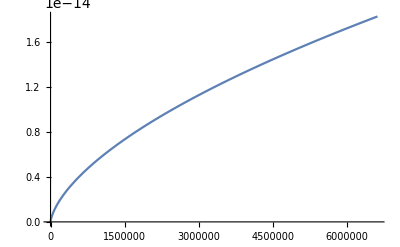

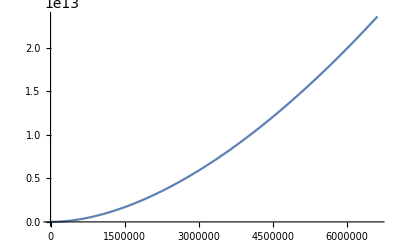

-1/(8 √2 mD^4 β^3)n π^(3/2) (β/m)^(3/2) (2 mD ((ⅇ^(m β-(β (mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)) (m^8 β^3-2 m^6 mD β^2 (5+2 mD β)+2 m^4 mD β (5 mD^2 β+3 mD^3 β^2+β √(mD (2 mD+Λ) (2 m^2+mD Λ))+mD (20-β Λ))+2 m^2 mD^2 (5 mD^3 β^2-2 mD^4 β^3+16 β √(mD (2 mD+Λ) (2 m^2+mD Λ))+2 mD^2 β (12+β Λ)+mD (24+24 β Λ-2 β^2 √(mD (2 mD+Λ) (2 m^2+mD Λ))))+mD^3 (-10 mD^4 β^2+mD^5 β^3-2 mD^3 β (-20+β Λ)+16 √(mD (2 mD+Λ) (2 m^2+mD Λ)) (3+β Λ)+16 mD (3 Λ+β Λ^2+2 β √(mD (2 mD+Λ) (2 m^2+mD Λ)))+2 mD^2 (24+24 β Λ+β^2 √(mD (2 mD+Λ) (2 m^2+mD Λ))))))/(m^2+mD^2+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ)))-8 mD (m^4 β^2+mD^4 β^2+mD^2 (8+8 m β+6 m^2 β^2)) ExpIntegralEi[-(β (-2 m mD+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)])-16 ⅇ^(2 m β) mD^2 (m^4 β^2+mD^4 β^2+mD^2 (8-8 m β+6 m^2 β^2)) ExpIntegralEi[-(β (2 m mD+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)]+ⅇ^(((m+mD)^2 β)/(2 mD)) (-8 m^6 mD β^3-8 mD^7 β^3+m^8 β^4+mD^8 β^4+8 m^2 mD^3 β (-8+m^2 β^2)+8 mD^5 β (-8+m^2 β^2)-4 m^4 mD^2 β^2 (-8+m^2 β^2)-4 mD^6 β^2 (-8+m^2 β^2)+2 mD^4 (64+32 m^2 β^2+3 m^4 β^4)) ExpIntegralEi[-(β (m^2+mD^2+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)])

```mathematica
Clear[dEdtdND]
dEdtdND[βt_,mt_,κ_] :=- 2/π(α^2 κ^2)/mt meqmDreduced/.{Λ->Λ[βt],n->n0}/.{β->βt,m->mt};
Plot[dEdtdND[β,me,1],{β,1/Td,1/TR}]
Plot[dEdtdND[β,me,1]/aH[β],{β,1/Td,1/TR}]
```

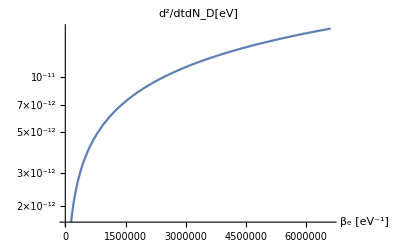

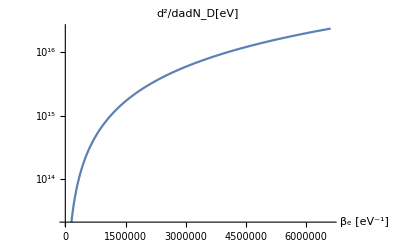

```mathematica
(*dEdtdND[β_,m_,κ_,mD] =- 2/π(α^2 κ^2)/mD mneqmDreduced/.{Λ->Λ[β],n->n0};*)
Clear[dEdtdND]
dEdtdND[βt_,mt_,mDt_,κ_] :=- 2/π(α^2 κ^2)/mDt meqmDreduced/.{Λ->Λ[βt],n->n0}/.{β->βt,m->mt}
LogPlot[dEdtdND[β,me,me/1000,1],{β,1/Td,1/TR},PlotLabel->"d^2/dtdN_D[eV]",AxesLabel->{"β_e [eV^-1]"}]
LogPlot[dEdtdND[β,me,me/1000,1]/aH[β],{β,1/Td,1/TR},PlotLabel->"d^2/dadN_D[eV]",AxesLabel->{"β_e [eV^-1]"}]
```

#### m neq mD case - post ne fix

Find cutoff energy - screening

```mathematica
Clear[m]
Solve[Λ==(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1),ESMt]
Simplify[%]
(*Simplify[PowerExpand[Simplify[%%/.mD->m]]]*)
Emin = ESMt/.%[[2]]
```

{{ESMt→(mD Λ-√(4 m^2 mD^2+2 m^2 mD Λ+2 mD^3 Λ+mD^2 Λ^2))/(2 mD)},{ESMt→(mD Λ+√(4 m^2 mD^2+2 m^2 mD Λ+2 mD^3 Λ+mD^2 Λ^2))/(2 mD)}}

{{ESMt→(mD Λ-√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD)},{ESMt→(mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD)}}

(mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD)

```mathematica
Emin/.Λ->Λ[β]
```

(√(mD (2 mD+13.0408/β^(3/2)) (2 m^2+(13.0408 mD)/β^(3/2)))+(13.0408 mD)/β^(3/2))/(2 mD)

integrate to find expression for energy transfer rates

```mathematica
Clear[m,mneqmDreduced]
Integrate[1/Ett((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett];
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->Λ)]];
(*Integrate[%/(E^(β ESMt)+1),ESMt]*)
FullintApproxTherm = Integrate[E^(-β ESMt + β μ)%,ESMt];
Simplify[FullintApproxTherm/.ESMt->Emin];
(*mneqmDreduced=Simplify[%/.μ->m + 1/β Log[n ((2π β)/m)^(3/2)]]*)
mneqmDreduced=Simplify[%/.μ->m + 1/β Log[Qt]]
```

1/(32 mD^4 β^3)Qt (-((2 ⅇ^(-(β (-2 m mD+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)) mD (m^8 β^3-2 m^6 mD β^2 (5+2 mD β)+2 m^4 mD β (5 mD^2 β+3 mD^3 β^2+β √(mD (2 mD+Λ) (2 m^2+mD Λ))+mD (20-β Λ))+2 m^2 mD^2 (5 mD^3 β^2-2 mD^4 β^3+16 β √(mD (2 mD+Λ) (2 m^2+mD Λ))+2 mD^2 β (12+β Λ)+mD (24+24 β Λ-2 β^2 √(mD (2 mD+Λ) (2 m^2+mD Λ))))+mD^3 (-10 mD^4 β^2+mD^5 β^3-2 mD^3 β (-20+β Λ)+16 √(mD (2 mD+Λ) (2 m^2+mD Λ)) (3+β Λ)+16 mD (3 Λ+β Λ^2+2 β √(mD (2 mD+Λ) (2 m^2+mD Λ)))+2 mD^2 (24+24 β Λ+β^2 √(mD (2 mD+Λ) (2 m^2+mD Λ))))))/(m^2+mD^2+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))+16 ⅇ^(2 m β) mD^2 (m^4 β^2+mD^4 β^2+mD^2 (8-8 m β+6 m^2 β^2)) ExpIntegralEi[-(β (2 m mD+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)]-ⅇ^(((m+mD)^2 β)/(2 mD)) (-8 m^6 mD β^3-8 mD^7 β^3+m^8 β^4+mD^8 β^4+8 m^2 mD^3 β (-8+m^2 β^2)+8 mD^5 β (-8+m^2 β^2)-4 m^4 mD^2 β^2 (-8+m^2 β^2)-4 mD^6 β^2 (-8+m^2 β^2)+2 mD^4 (64+32 m^2 β^2+3 m^4 β^4)) ExpIntegralEi[-(β (m^2+mD^2+mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ))))/(2 mD)]+16 mD^2 (m^4 β^2+mD^4 β^2+mD^2 (8+8 m β+6 m^2 β^2)) ExpIntegralEi[β (m-(mD Λ+√(mD (2 mD+Λ) (2 m^2+mD Λ)))/(2 mD))])

```mathematica
(*Simplify[mneqmDreduced/.mD->ξ m]*)
```

1/(8 √2 m^4 β^3 ξ^4)n π^(3/2) (β/m)^(3/2) (16 m^4 ξ^2 (8 ξ^2+8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[-β Λ]+16 ⅇ^(2 m β) m^4 ξ^2 (8 ξ^2-8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[-β (2 m+Λ)]-ⅇ^((m β (1+ξ)^2)/(2 ξ)) m^4 (128 ξ^4+m^4 β^4 (-1+ξ^2)^4-64 m β ξ^3 (1+ξ^2)-8 m^3 β^3 ξ (-1+ξ^2)^2 (1+ξ^2)+32 m^2 β^2 ξ^2 (1+ξ^2)^2) ExpIntegralEi[-(β (2 Λ ξ+m (1+ξ)^2))/(2 ξ)]-(2 ⅇ^(-β Λ) m^2 ξ (m^6 β^3-10 m^5 β^2 ξ+40 m^4 β ξ^2-4 m^6 β^3 ξ^2-16 m^4 β^2 Λ ξ^2+4 m^4 β^2 (m+Λ) ξ^2+48 m^3 ξ^3-14 m^5 β^2 ξ^3+32 m^3 β Λ ξ^3-8 m^3 β^2 Λ^2 ξ^3+64 m^3 β (m+Λ) ξ^3+24 m^3 β^2 (m+Λ)^2 ξ^3+80 m^4 β ξ^4+6 m^6 β^3 ξ^4-32 m^4 β^2 Λ ξ^4+96 m^2 (m+Λ) ξ^4+40 m^4 β^2 (m+Λ) ξ^4+64 m^2 β Λ (m+Λ) ξ^4-16 m^2 β^2 Λ^2 (m+Λ) ξ^4-32 m^2 β (m+Λ)^2 ξ^4+64 m^2 β^2 Λ (m+Λ)^2 ξ^4-48 m^2 β^2 (m+Λ)^3 ξ^4+48 m^3 ξ^5-14 m^5 β^2 ξ^5+32 m^3 β Λ ξ^5-8 m^3 β^2 Λ^2 ξ^5+64 m^3 β (m+Λ) ξ^5+24 m^3 β^2 (m+Λ)^2 ξ^5+40 m^4 β ξ^6-4 m^6 β^3 ξ^6-16 m^4 β^2 Λ ξ^6+4 m^4 β^2 (m+Λ) ξ^6-10 m^5 β^2 ξ^7+m^6 β^3 ξ^8-8 ξ (m^4 β^2+2 m^2 (4+m^2 β^2+4 β (m+Λ)+2 β^2 (m+Λ)^2) ξ^2+m^4 β^2 ξ^4) (2 Λ ξ+m (1+ξ)^2) Log[Λ]+8 ξ (m^4 β^2+2 m^2 (4+m^2 β^2+4 β (m+Λ)+2 β^2 (m+Λ)^2) ξ^2+m^4 β^2 ξ^4) (2 Λ ξ+m (1+ξ)^2) Log[(2 Λ (2 m+Λ) ξ)/(2 Λ ξ+m (1+ξ)^2)]))/(2 Λ ξ+m (1+ξ)^2))

```mathematica
(*Series[mneqmDreduced/.Λ->ξ/β,{ξ,∞,1}]*)
```

ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 m^3 n π^(3/2) √(β/m) ξ))/((mD (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 m^3 n π^(3/2) √(β/m) ξ))/((mD (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((4 √2 m^3 n π^(3/2) √(β/m) ξ)/(mD (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(12 (√2 m mD n π^(3/2) √(β/m) ξ))/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(12 (√2 m mD n π^(3/2) √(β/m) ξ))/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((8 √2 m mD n π^(3/2) √(β/m) ξ)/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 mD^3 n π^(3/2) √(β/m) ξ))/((m (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 mD^3 n π^(3/2) √(β/m) ξ))/((m (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((4 √2 mD^3 n π^(3/2) √(β/m) ξ)/(m (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(16 (√2 mD n π^(3/2) √(β/m) ξ))/((m β^2 (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(16 (√2 mD n π^(3/2) √(β/m) ξ))/((m β^2 (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((16 √2 mD n π^(3/2) √(β/m) ξ)/(m β^2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(8 (√2 m n π^(3/2) √(β/m) ξ))/((β (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(16 (√2 mD n π^(3/2) √(β/m) ξ))/((β (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((16 √2 mD n π^(3/2) √(β/m) ξ)/(β (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(8 (√2 mD^2 n π^(3/2) √(β/m) ξ))/((m β (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((√2 m^3 n π^(3/2) β √(β/m) ξ)/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(√2 m^5 n π^(3/2) β √(β/m) ξ)/(mD^2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((√2 m mD^2 n π^(3/2) β √(β/m) ξ)/((mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(√2 mD^4 n π^(3/2) β √(β/m) ξ)/(m (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((m^7 n π^(3/2) β^2 √(β/m) ξ)/(4 √2 mD^3 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(m^5 n π^(3/2) β^2 √(β/m) ξ)/(√2 mD (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((3 m^3 mD n π^(3/2) β^2 √(β/m) ξ)/(2 √2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(m mD^3 n π^(3/2) β^2 √(β/m) ξ)/(√2 (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)-(β (-2 m mD^2 ξ+m^2 β √((mD^2 ξ^2)/β^2)+mD^2 β √((mD^2 ξ^2)/β^2)))/(2 (mD^2 ξ))+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) ((mD^5 n π^(3/2) β^2 √(β/m) ξ)/(4 √2 m (mD ξ+β √((mD^2 ξ^2)/β^2)) ξ)+O[1/ξ]^2)+(-1/(16 (√2 m mD^4 β^2))n π^(3/2) √(β/m) (-128 mD^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 ⅇ^(2 m β) mD^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 m mD^4 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 ⅇ^(2 m β) m mD^4 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 m^4 mD^2 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-96 m^2 mD^4 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 mD^6 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-16 ⅇ^(2 m β) mD^6 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[(-mD ξ-β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 mD^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 ⅇ^(2 m β) mD^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 m mD^4 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 ⅇ^(2 m β) m mD^4 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 m^4 mD^2 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+96 m^2 mD^4 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 mD^6 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+16 ⅇ^(2 m β) mD^6 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[-(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 mD^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 ⅇ^(2 m β) mD^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-128 m mD^4 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 ⅇ^(2 m β) m mD^4 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 m^4 mD^2 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-96 m^2 mD^4 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 mD^6 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-16 ⅇ^(2 m β) mD^6 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]-4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[(2 mD)/(mD ξ+β √((mD^2 ξ^2)/β^2))]+128 mD^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 ⅇ^(2 m β) mD^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^3 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+128 m mD^4 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-128 ⅇ^(2 m β) m mD^4 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+64 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^5 β Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 m^4 mD^2 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 ⅇ^(2 m β) m^4 mD^2 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^2 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+96 m^2 mD^4 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+96 ⅇ^(2 m β) m^2 mD^4 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-64 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^4 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 mD^6 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+16 ⅇ^(2 m β) mD^6 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-32 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^6 β^2 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^3 β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-8 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^5 β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+8 ⅇ^(((m+mD)^2 β)/(2 mD)) mD^7 β^3 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-ⅇ^(((m+mD)^2 β)/(2 mD)) m^8 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^6 mD^2 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-6 ⅇ^(((m+mD)^2 β)/(2 mD)) m^4 mD^4 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]+4 ⅇ^(((m+mD)^2 β)/(2 mD)) m^2 mD^6 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)]-ⅇ^(((m+mD)^2 β)/(2 mD)) mD^8 β^4 Log[(mD ξ+β √((mD^2 ξ^2)/β^2))/(2 mD)])+O[1/ξ]^2)+ⅇ^(((-mD ξ-β √((mD^2 ξ^2)/β^2)) ξ)/(2 mD ξ)+(2 m mD^2 β ξ-m^2 β^2 √((mD^2 ξ^2)/β^2)-mD^2 β^2 √((mD^2 ξ^2)/β^2))/(2 mD^2 ξ)+((-m+mD)^2 (m+mD)^2 β^3 √((mD^2 ξ^2)/β^2))/(4 mD^3 ξ ξ)+O[1/ξ]^2) (-(2 (√2 n π^(3/2) √(β/m)) ξ)/(m β^2)-(n π^(3/2) √(β/m) (24 mD^3 ξ+16 m^2 mD^2 β ξ+16 mD^4 β ξ-m^4 mD β^2 ξ+2 m^2 mD^3 β^2 ξ-mD^5 β^2 ξ+24 mD^2 β √((mD^2 ξ^2)/β^2)+16 m^2 mD β^2 √((mD^2 ξ^2)/β^2)+16 mD^3 β^2 √((mD^2 ξ^2)/β^2)+m^4 β^3 √((mD^2 ξ^2)/β^2)-2 m^2 mD^2 β^3 √((mD^2 ξ^2)/β^2)+mD^4 β^3 √((mD^2 ξ^2)/β^2)))/(2 (√2 m mD^2 β^2 (mD ξ+β √((mD^2 ξ^2)/β^2))))-(n π^(3/2) √(β/m) (8 m^4 mD^2 ξ-16 m^2 mD^4 ξ+8 mD^6 ξ-8 m^6 mD β ξ+8 m^4 mD^3 β ξ+8 m^2 mD^5 β ξ-8 mD^7 β ξ+m^8 β^2 ξ-4 m^6 mD^2 β^2 ξ+6 m^4 mD^4 β^2 ξ-4 m^2 mD^6 β^2 ξ+mD^8 β^2 ξ))/(4 (√2 m mD^3 (mD ξ+β √((mD^2 ξ^2)/β^2))) ξ)+O[1/ξ]^2)

```mathematica
(*N[dEdtdND[1/TR,me,1]]*)
```

-1/mD^47.33509×10^-33 (-((3.96835 2.71828^(3.30579×10^12-(3.30579×10^6 (7.67092×10^-10 mD+√((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))))/mD) mD (1.12895×10^66-1.36603×10^48 mD (5.+1.32231×10^7 mD)+8.26446×10^29 mD (19.9949 mD+3.30579×10^7 mD^2+1.31139×10^14 mD^3+6.61157×10^6 √((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD)))+5.×10^11 mD^2 (1.58745×10^8 mD^2+2.18564×10^14 mD^3-5.78021×10^20 mD^4+1.05785×10^8 √((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))+mD (24.1217-8.74257×10^13 √((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))))+mD^3 (2.64396×10^8 mD^3-4.37129×10^14 mD^4+2.89011×10^20 mD^5+48.0811 √((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))+16. mD (2.30517×10^-9+1.32231×10^7 √((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD)))+2. mD^2 (24.1217+4.37129×10^13 √((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))))))/(2.5×10^11+7.67092×10^-10 mD+mD^2+√((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))))+7.97981415690532537921757600205`15.954589770191005*^2871368475394 mD^2 (2.73205×10^36+6.55693×10^25 mD^2+4.37129×10^13 mD^4) ExpIntegralEi[-1/mD 3.30579×10^6 (1.×10^6 mD+√((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD)))]-1.98418 2.71828^((3.30579×10^6 (500000.+mD)^2)/mD) (7.46412×10^72-3.61263×10^55 mD-1.19426×10^62 mD^2+1.44505×10^44 mD^3+7.16555×10^50 mD^4+5.78021×10^32 mD^5-1.91081×10^39 mD^6-2.31209×10^21 mD^7+1.91081×10^27 mD^8) ExpIntegralEi[-1/mD 3.30579×10^6 (2.5×10^11+7.67092×10^-10 mD+mD^2+√((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD)))]+31.7468 mD^2 (2.73205×10^36+6.55693×10^25 mD^2+4.37129×10^13 mD^4) ExpIntegralEi[6.61157×10^6 (500000.-1/mD 0.5 (7.67092×10^-10 mD+√((5.×10^11+7.67092×10^-10 mD) mD (7.67092×10^-10+2. mD))))])

```mathematica
(*Clear[dEdtdND]
(*dEdtdND[βt_,mt_,κ_] :=- 2/π(α^2 κ^2)/mt meqmDreduced/.{Λ->Λ[βt],n->ne[β]}/.{β->βt,m->mt};*)
dEdtdND[βt_,mt_,κ_] :=- 2/π(α^2 κ^2)/mt mneqmDreduced/.{Λ->Λ[βt],n->ne[β]}/.{β->βt,m->mt};
LogPlot[dEdtdND[β,me,1],{β,1/Td,1/TR},PlotLabel->"d^2/dtdN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
LogPlot[dEdtdND[β,me,1]/aH[β],{β,1/Td,1/TR},PlotLabel->"d^2/dadN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]*)
```

-Graphics-

-Graphics-

General::munfl: Exp[-9218.52] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9227.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6869.32] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

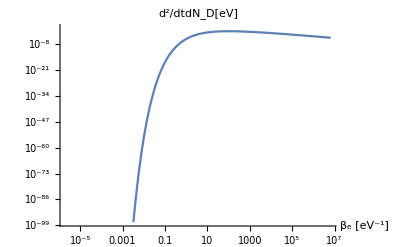

```mathematica
(*LogLogPlot[dEdtdND[β,me,1],{β,1/Td,1/TR},PlotLabel->"d^2/dtdN_D[eV]",AxesLabel->{"β_e [eV^-1]"}]*)
```

General::munfl: Exp[-1.35065×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

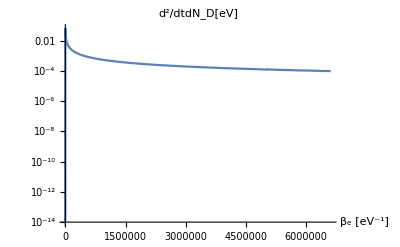

General::munfl: Exp[-1.35065×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

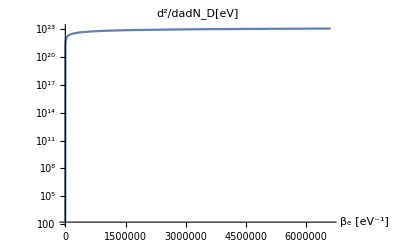

```mathematica
(*dEdtdND[β_,m_,κ_,mD] =- 2/π(α^2 κ^2)/mD mneqmDreduced/.{Λ->Λ[β],n->n0};*)
Clear[dEdtdND]
dEdtdND[βt_,mt_,mDt_,κ_] :=- 2/π(α^2 κ^2)/mDt mneqmDreduced /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}
(*dEdtdND[βt_,mt_,mDt_,κ_] :=- 2/π(α^2 κ^2)/mDt meqmDreduced/.{Λ->Λ[βt],n->ne[β]}/.{β->βt,m->mt}*)
LogPlot[dEdtdND[β,me,me,1],{β,1/Td,1/TR},PlotLabel->"d^2/dtdN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
LogPlot[dEdtdND[β,me,me,1]/aH[β],{β,1/Td,1/TR},PlotLabel->"d^2/dadN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

General::munfl: Exp[-1.00035×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

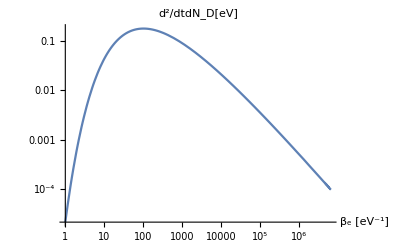

General::munfl: Exp[-1.00035×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

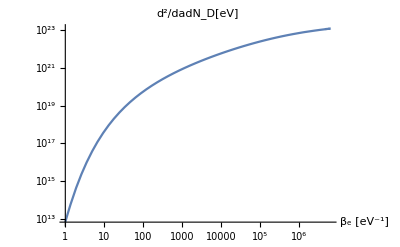

```mathematica
LogLogPlot[dEdtdND[β,me,me,1],{β,1,1/TR},PlotLabel->"d^2/dtdN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
LogLogPlot[dEdtdND[β,me,me,1]/aH[β],{β,1,1/TR},PlotLabel->"d^2/dadN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

General::munfl: Exp[-1.00035×10^6] is too small to represent as a normalized machine number; precision may be lost.

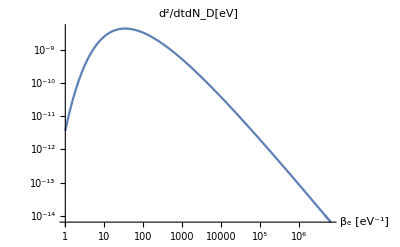

General::munfl: Exp[-1.00035×10^6] is too small to represent as a normalized machine number; precision may be lost.

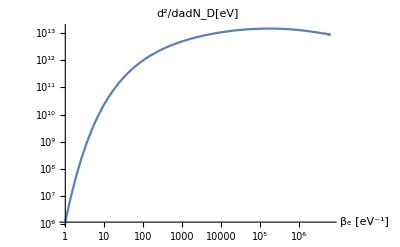

```mathematica
LogLogPlot[1/2(Tdt/β)^(1/2)dEdtdND[β,me,me,1],{β,1,1/TR},PlotLabel->"d^2/dtdN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
LogLogPlot[1/2(Tdt/β)^(1/2)dEdtdND[β,me,me,1]/aH[β],{β,1,1/TR},PlotLabel->"d^2/dadN_D[eV]",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

```mathematica
Simplify[dEdtdND[β,me,me,1]]
```

(ⅇ^(-6.5204/(√β)+(500000.-500000. √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β) (0.0000228906+5.26592×10^-6 √β+(5.26592+1.75531 √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^(3/2)+(0.403804+0.403804 √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^2+(269203.+269203. √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^3+ⅇ^(6.5204/(√β)+(-500000.+500000. √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β) √β (-7.02123×10^-6-3.51062 β+(-0.538405-0.538405 √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^(3/2)-1.75531×10^6 β^2+(-269203.-269203. √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^(5/2)+(-1.34601×10^11-1.34601×10^11 √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^(7/2)) ExpIntegralEi[-6.5204/(√β)+500000. β-500000. √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2)) β]))/(β^(7/2) (13040.8+(1.×10^9+1.×10^9 √(1+(1.70062×10^-10)/β^3+0.0000260816/β^(3/2))) β^(3/2)))

```mathematica
Information[dEdtdND]
```

```mathematica
Solve[Tdt == a^2,a]
```

{{a→-3.53553×10^-7},{a→3.53553×10^-7}}

```mathematica
Solve[Tdt == (4 10^8 )^-2 TBBN,TBBN]
```

{{TBBN→20000.}}

```mathematica
meqmnumfunc[β_?NumberQ]:=1/2(Tdt/β)^(1/2)dEdtdND[β,me,me,1]/aH[β]
NIntegrate[meqmnumfunc[β],{β,1,1/TR}]
```

NIntegrate::inumri: The integrand meqmnumfunc[β] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{1,6.61157×10^6}}.

NIntegrate[meqmnumfunc[β],{β,1,1/TR}]

```mathematica
meqmnumfunc[1/TR]
```

General::munfl: Exp[-6.61157×10^12] is too small to represent as a normalized machine number; precision may be lost.

8.52046×10^12

```mathematica
meqmnumfunc[1000000000/Td]
```

General::munfl: Exp[-2.×10^9] is too small to represent as a normalized machine number; precision may be lost.

6.49342×10^12

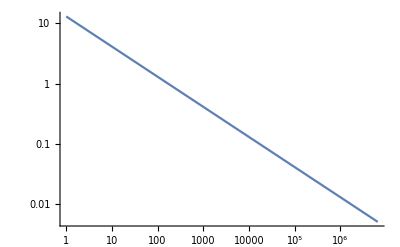

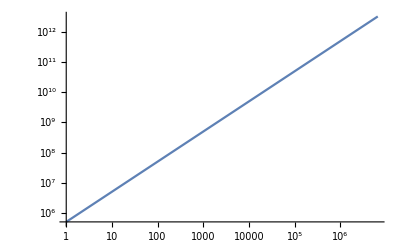

```mathematica
LogLogPlot[β Λ[β],{β,1,1/TR}]
LogLogPlot[β Emin/.Λ->Λ[β]/.{mD->m}/.m->me,{β,1,1/TR}]
```

#### Find analytic expression for integral over β - m=mD case

```mathematica
(*FullSimplify[PowerExpand[Simplify[mneqmDreduced/.mD->m]]]
meqmEtotal = Integrate[%,β]*)
```

(Qt (-ⅇ^(-β Λ) (3+4 m β+β Λ)+4 (1+m β (1+m β)) ExpIntegralEi[-β Λ]))/β^3

(ⅇ^(-β Λ) Qt (3+8 m β-β Λ-ⅇ^(β Λ) β^2 Λ (-8 m+Λ) ExpIntegralEi[-β Λ]))/(2 β^2)+1/2 Qt (-14 m^2-(2 ⅇ^(-β Λ))/β^2-(8 ⅇ^(-β Λ) m)/β+(2 ⅇ^(-β Λ) Λ)/β+16 m^2 β Λ Gamma[0,β Λ]-2 m^2 β^2 Λ^2 Gamma[0,β Λ]-8 m^2 β Λ HypergeometricPFQ[{1,1,1},{2,2,2},-β Λ]+8 EulerGamma m^2 Log[β]+8 m^2 Gamma[0,β Λ] Log[β]-4 m^2 Log[β]^2+2 ExpIntegralEi[-β Λ] (-2/β^2+Λ^2+m^2 β Λ (8-β Λ)-(4 m (1+β Λ))/β+4 m^2 Log[β])+8 m^2 β Λ Log[-1/(β Λ)]-m^2 β^2 Λ^2 Log[-1/(β Λ)]-8 m^2 β Λ Log[-β Λ]+m^2 β^2 Λ^2 Log[-β Λ]+16 m^2 β Λ Log[β Λ]-2 m^2 β^2 Λ^2 Log[β Λ]+8 m^2 Log[β] Log[β Λ])

```mathematica
(*FullSimplify[PowerExpand[Simplify[mneqmDreduced/.mD->m]]]
meqmEtotal = Integrate[1/2(T0/β)^(1/2)%,β]*)
```

(Qt (-ⅇ^(-β Λ) (3+4 m β+β Λ)+4 (1+m β (1+m β)) ExpIntegralEi[-β Λ]))/β^3

-1/(225 β^2)ⅇ^(-β Λ) Qt √(T0/β) (-63-100 m β+1800 m^2 β^2-33 β Λ+200 m β^2 Λ+66 β^2 Λ^2+2 ⅇ^(β Λ) √π β^(5/2) √Λ (900 m^2+100 m Λ+33 Λ^2) Erf[√β √Λ]+60 ⅇ^(β Λ) (3+5 m β+15 m^2 β^2) ExpIntegralEi[-β Λ])

```mathematica
FullSimplify[PowerExpand[Simplify[mneqmDreduced/.mD->m/.Λ->ΛnoT β]]]
%/.ΛnoT->0
meqmEtotal = Integrate[-1/2(T0/β)^(1/2)%%,β]
```

(Qt (-ⅇ^(-β^2 ΛnoT) (3+4 m β+β^2 ΛnoT)+4 (1+m β (1+m β)) ExpIntegralEi[-β^2 ΛnoT]))/β^3

(Qt (-3-4 m β+(1+m β (1+m β)) (-∞)))/β^3

1/(225 (β^2 ΛnoT)^(7/4))ⅇ^(-β^2 ΛnoT) Qt √(T0/β) ΛnoT (9 (β^2 ΛnoT)^(3/4)+100 m β (β^2 ΛnoT)^(3/4)+3600 m^2 β^2 (β^2 ΛnoT)^(3/4)-261 (β^2 ΛnoT)^(7/4)+60 ⅇ^(β^2 ΛnoT) (3+5 m β+15 m^2 β^2) (β^2 ΛnoT)^(3/4) ExpIntegralEi[-β^2 ΛnoT]-100 ⅇ^(β^2 ΛnoT) m β (β^2 ΛnoT)^(3/2) Gamma[1/4,β^2 ΛnoT]-3600 ⅇ^(β^2 ΛnoT) m^2 β^4 ΛnoT Gamma[3/4,β^2 ΛnoT]+261 ⅇ^(β^2 ΛnoT) β^4 ΛnoT^2 Gamma[3/4,β^2 ΛnoT])

```mathematica
meqmEtotal/.{ΛnoT->Λ[β]/β^(1/2),Qt->Q}/.{m->me,T0->Tdt}
```

-9.8589×10^-16 (1/β)^(5/2) (-349.086+1.75245×10^7 β+1.08637×10^14 β^2-29.4576 (3+2500000 β+3750000000000 β^2))

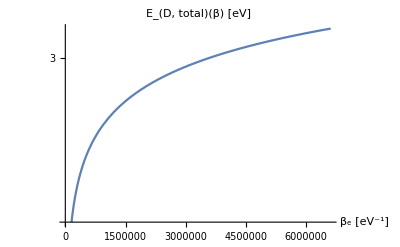

```mathematica
LogPlot[2/π(α^2 κ^2)/m(meqmEtotal-(meqmEtotal/.β->1/Td))/.{ΛnoT->Λ[β]/β,Qt->Q}/.{m->me,T0->Tdt,κ->1}/.β->βt,{βt,1/Td,1/TR},PlotLabel->"E_(D, total)(β) [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

General::munfl: Exp[-1303.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1310.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1309.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

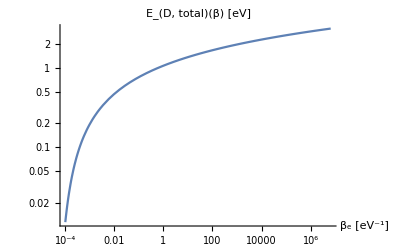

```mathematica
LogLogPlot[2/π(α^2 κ^2)/m(meqmEtotal-(meqmEtotal/.β->1/Td))/.{ΛnoT->Λ[β]/β,Qt->Q}/.{m->me,T0->Tdt,κ->1}/.β->βt,{βt,1/10000,1/TR},PlotLabel->"E_(D, total)(β) [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

```mathematica
FullSimplify[PowerExpand[Simplify[mneqmDreduced/.mD->m 10]]]
meqmEtotal = Integrate[%,β]
```

$Aborted

β $Aborted

```mathematica
Simplify[mneqmDreduced/.mD->m ξ]
meqmEtotal = Integrate[%,β]
```

1/(32 β^3 ξ^4)Qt (-((2 ⅇ^(-(β (-2 m^2 ξ+m Λ ξ+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))/(2 m ξ)) ξ (16 (3+β Λ) ξ^3 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))+m^5 β^3 (-1+ξ^2)^4-10 m^4 β^2 ξ (-1+ξ^2)^2 (1+ξ^2)+16 m (3 Λ ξ^4+β Λ^2 ξ^4+2 β ξ^2 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ)) (1+ξ^2))+2 m^3 β ξ^2 (-β Λ (-1+ξ^2)^2+4 (5+6 ξ^2+5 ξ^4))+2 m^2 (β^2 ξ √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))-2 ξ^3 (-12-12 β Λ+β^2 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ)))+ξ^5 (24+24 β Λ+β^2 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))))/(m^2+m Λ ξ+m^2 ξ^2+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))+16 ⅇ^(2 m β) ξ^2 (8 ξ^2-8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[-(β (2 m^2 ξ+m Λ ξ+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))/(2 m ξ)]-ⅇ^((m β (1+ξ)^2)/(2 ξ)) (128 ξ^4+m^4 β^4 (-1+ξ^2)^4-64 m β ξ^3 (1+ξ^2)-8 m^3 β^3 ξ (-1+ξ^2)^2 (1+ξ^2)+32 m^2 β^2 ξ^2 (1+ξ^2)^2) ExpIntegralEi[-(β (m^2+m Λ ξ+m^2 ξ^2+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))/(2 m ξ)]+16 ξ^2 (8 ξ^2+8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[β (m-(m Λ ξ+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ)))/(2 m ξ))])

1/(32 ξ^4)Qt ∫1/β^3(-((2 ⅇ^(-(β (-2 m^2 ξ+m Λ ξ+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))/(2 m ξ)) ξ (16 (3+β Λ) ξ^3 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))+m^5 β^3 (-1+ξ^2)^4-10 m^4 β^2 ξ (-1+ξ^2)^2 (1+ξ^2)+16 m (3 Λ ξ^4+β Λ^2 ξ^4+2 β ξ^2 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ)) (1+ξ^2))+2 m^3 β ξ^2 (-β Λ (-1+ξ^2)^2+4 (5+6 ξ^2+5 ξ^4))+2 m^2 (β^2 ξ √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))-2 ξ^3 (-12-12 β Λ+β^2 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ)))+ξ^5 (24+24 β Λ+β^2 √(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))))/(m^2+m Λ ξ+m^2 ξ^2+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))+16 ⅇ^(2 m β) ξ^2 (8 ξ^2-8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[-(β (2 m^2 ξ+m Λ ξ+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))/(2 m ξ)]-ⅇ^((m β (1+ξ)^2)/(2 ξ)) (128 ξ^4+m^4 β^4 (-1+ξ^2)^4-64 m β ξ^3 (1+ξ^2)-8 m^3 β^3 ξ (-1+ξ^2)^2 (1+ξ^2)+32 m^2 β^2 ξ^2 (1+ξ^2)^2) ExpIntegralEi[-(β (m^2+m Λ ξ+m^2 ξ^2+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ))))/(2 m ξ)]+16 ξ^2 (8 ξ^2+8 m β ξ^2+m^2 β^2 (1+6 ξ^2+ξ^4)) ExpIntegralEi[β (m-(m Λ ξ+√(m^2 ξ (Λ+2 m ξ) (2 m+Λ ξ)))/(2 m ξ))])ⅆβ

### Put into propagator instead

#### find energy transfer

```mathematica
(*Clear[m,ESMt,Integrand]
Integrate[1/(Ett+Λ)((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]]
Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]
Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESMt_?NumberQ]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]
NIntegrate[NumIntegrand[me,me,1,10/TR,ESM],{ESM,me,∞}]*)
(*FullintApproxTherm =NIntegrate[%,ESMt]*)


(*Simplify[FullintApproxTherm/.ESMt->Emin];*)
(*Simplify[FullintApproxTherm/.ESMt->0];*)
(*mneqmDreduced=Simplify[%/.μ->m + 1/β Log[n ((2π β)/m)^(3/2)]]*)
```

1/2 (Ett+Λ)^2-2 (Ett+Λ) (ESMt-ms+Λ)+(2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2) Log[Ett+Λ]

1/(2 mD^2)(-mD (2 m^2+mD (-4 ESMt+2 mD-3 Λ)) Λ+mD (2 m^2+mD (-4 ESMt+2 mD+(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))-3 Λ)) ((2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ)-(m^4+2 m^2 mD (mD-Λ)+mD^2 (4 ESMt^2+mD^2+4 ESMt Λ-2 mD Λ+2 Λ^2)) Log[Λ]+(m^4+2 m^2 mD (mD-Λ)+mD^2 (4 ESMt^2+mD^2+4 ESMt Λ-2 mD Λ+2 Λ^2)) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ])

1/(18769 mDt^3 π)ⅇ^(βt (-ESMt+μ)) κ^2 (mDt (2 mt^2+mDt (-4 ESMt+2 mDt+(2 mDt (ESMt^2-mt^2))/(2 ESMt mDt+mDt^2+mt^2)-39.1224/βt^(3/2))) ((2 mDt (ESMt^2-mt^2))/(2 ESMt mDt+mDt^2+mt^2)+13.0408/βt^(3/2))-(13.0408 mDt (2 mt^2+mDt (-4 ESMt+2 mDt-39.1224/βt^(3/2))))/βt^(3/2)+(mt^4+2 mDt mt^2 (mDt-13.0408/βt^(3/2))+mDt^2 (4 ESMt^2+mDt^2+340.125/βt^3+(52.1632 ESMt)/βt^(3/2)-(26.0816 mDt)/βt^(3/2))) Log[(2 mDt (ESMt^2-mt^2))/(2 ESMt mDt+mDt^2+mt^2)+13.0408/βt^(3/2)]-(mt^4+2 mDt mt^2 (mDt-13.0408/βt^(3/2))+mDt^2 (4 ESMt^2+mDt^2+340.125/βt^3+(52.1632 ESMt)/βt^(3/2)-(26.0816 mDt)/βt^(3/2))) (2.56808+Log[1/βt^(3/2)]))

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
Clear[m,ESMt,Integrand]
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]]
%%/.Ett->0
(*Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]*)
Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESM_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}/.ESMt->ESM)
(*NIntegrate[NumIntegrand[me,me,1,10000000/TR,ESM],{ESM,me,  1.00000000000001  me},AccuracyGoal->Infinity]*)
```

Ett^2/2-2 Ett (ESMt-ms+Λ)+(Λ (2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2))/(Ett+Λ)+(2 ESMt^2+2 ms^2+4 ESMt Λ-4 ms Λ+3 Λ^2) Log[Ett+Λ]

-2 ESMt^2-((m^2+mD^2)^2)/(2 mD^2)+(2 mD^2)/((-1+(ESMt+mD)^2/(ESMt^2-m^2))^2)+(2 (ESMt^2-m^2) (m^2+mD (-2 ESMt+mD-2 Λ)))/(m^2+mD (2 ESMt+mD))-2 ESMt Λ+((m^2+mD^2) Λ)/mD-Λ^2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/((2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ)-(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ]+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ]

2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ]

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
Clear[NumIntegrand]
(*NumIntegrand[mDt_,mt_,κ_,βt_,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.ESMt->1/β ξE + m/.{β->βt,m->mt,mD->mDt})*)
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/TR/.{m->mt,mD->mDt})*)
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}]
NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,∞},AccuracyGoal->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.910504}. NIntegrate obtained 586007. and 49.687 for the integral and error estimates.

586007.

```mathematica
NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,10^1},AccuracyGoal->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.208329}. NIntegrate obtained 582967. and 50.2039 for the integral and error estimates.

582967.

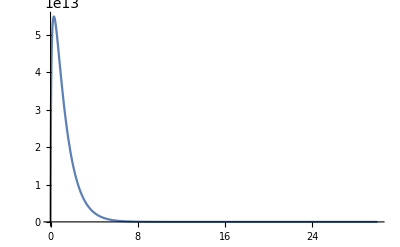

```mathematica
Plot[1/2(Tdt/me)^(1/2)1/(me/(1TR))^(1/2)NumIntegrand[me,me,1,me/(1TR),ξE],{ξE,0,30},PlotRange->All]
```

```mathematica
ESMIntegral[ me/100,me,1,10/Td]
```

NIntegrate::inumr: The integrand NumIntegrand[5000,500000,1,1/50000,ξE] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[NumIntegrand[5000,500000,1,1/50000,ξE],{ξE,0,∞}]

```mathematica
ESMIntegral[ me/100,me,1,10/Td]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.684255}. NIntegrate obtained 0.00400021 and 9.78528×10^-8 for the integral and error estimates.

0.00400021

```mathematica
1/2(Tdt/me)^(1/2)NIntegrate[1/ξβ^(1/2)ESMIntegral[me,me,1,ξβ],{ξβ,10^-1,1}]
```

$Aborted

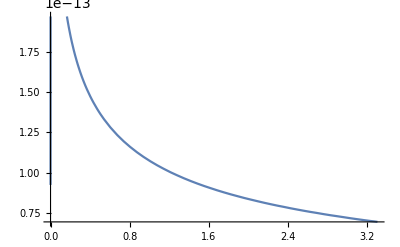

```mathematica
Plot[1/2(Tdt/(ξβ me))^(1/2)ESMIntegral[me,me,1,ξβ],{ξβ,me/Td,me/TR}]
```

```mathematica
Plot[ESMIntegral[me,me,1,ξβ],{ξβ,me/Td,me/TR}]
```

```mathematica
NIntegrate[ESMIntegral[me,me,1,β],{β,1,1/TR}]
```

$Aborted

```mathematica
NIntegrate[NIntegrate[NumIntegrand[me,me,1,β,ξE],{ξE,0,∞},AccuracyGoal->Infinity],{β,1/Td,1/TR}]
```

NIntegrate::inumr: The integrand NumIntegrand[500000,500000,1,β,ξE] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

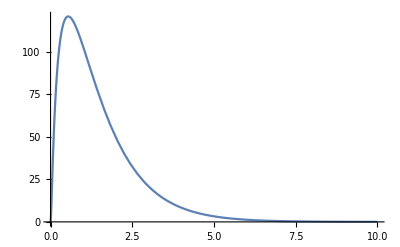

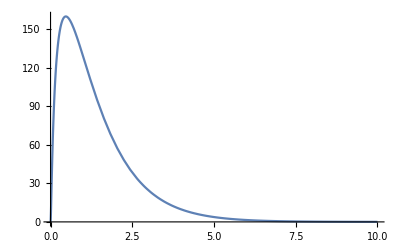

```mathematica
Plot[NumIntegrand[me,me,1,1/(100TR),ξE],{ξE,0,10}]
Plot[NumIntegrand[me,me,1,100000000000/Td,ξE],{ξE,0,10},PlotRange->All]
```

```mathematica
FullSimplify[NumIntegrand[10 me,me,1,1/(100TR),  N[me] ]]
```

(-3.56781×10^27+ESMt (-2.8344×10^21+ESMt (1.3105×10^16+ESMt (1.0893×10^10+ESMt (4582.15+(0.00177827+3.31943×10^-10 ESMt) ESMt))))+(-2.73567×10^26+ESMt (-2.16686×10^20+ESMt (1.00845×10^15+ESMt (8.32759×10^8+ESMt (336.536+(0.000135947+2.69201×10^-11 ESMt) ESMt))))) Log[-2.525×10^6+1. ESMt+(6.12563×10^12)/(2.525×10^6+1. ESMt)])/((2.525×10^6+ESMt)^2 (-2.5×10^11+ESMt (7.67092×10^-7+ESMt)))

```mathematica
NumIntegrand[10 me,me,1,1/(100TR),  1.00000000000001 me]
```

0.000413549

```mathematica
1/(100TR)
```

66115.7

```mathematica
FullSimplify[Integrand[mD,m,κ,β,ESMt]/.ESMt->1/β ξE + m]
FullSimplify[%/.β->ξβ/m]
FullSimplify[%/.{mD->me,m->me}]
```

-1/(18769 mD^3 π β^2)ⅇ^-ξE Qt κ^2 ((2 mD ξE (2 m β+ξE) ((m+mD)^4 β^4 (m^4+6 m^2 mD^2+mD^4-4 (m-mD)^2 mD Λ+6 mD^2 Λ^2)+4 mD (m+mD)^2 β^3 (m^4+2 m^2 mD (7 mD-Λ)+15 m mD^2 Λ+mD^2 (mD^2-2 mD Λ+6 Λ^2)) ξE+2 mD^2 β^2 (2 m^4+24 m^3 mD+mD^2 (2 mD+3 Λ) (mD+4 Λ)+6 m mD^2 (4 mD+11 Λ)+m^2 mD (84 mD+11 Λ)) ξE^2+4 mD^3 β (4 (m^2+7 m mD+mD^2)+11 mD Λ) ξE^3+28 mD^4 ξE^4))/(((m+mD)^2 β+2 mD ξE)^2 ((m+mD)^2 β^2 Λ+2 mD β (2 m+Λ) ξE+2 mD ξE^2))+(β^2 (m^4+6 m^2 mD^2+mD^4-4 (m-mD)^2 mD Λ+6 mD^2 Λ^2)+8 mD^2 β (m+Λ) ξE+4 mD^2 ξE^2) (Log[Λ]-Log[Λ+(2 mD ξE (2 m β+ξE))/(β ((m+mD)^2 β+2 mD ξE))]))

-1/(18769 mD^3 π ξβ^2)ⅇ^-ξE m^2 Qt κ^2 ((2 mD ξE (ξE+2 ξβ) (28 m^4 mD^4 ξE^4+4 m^3 mD^3 (4 (m^2+7 m mD+mD^2)+11 mD Λ) ξE^3 ξβ+2 m^2 mD^2 (2 m^4+24 m^3 mD+mD^2 (2 mD+3 Λ) (mD+4 Λ)+6 m mD^2 (4 mD+11 Λ)+m^2 mD (84 mD+11 Λ)) ξE^2 ξβ^2+4 m mD (m+mD)^2 (m^4+2 m^2 mD (7 mD-Λ)+15 m mD^2 Λ+mD^2 (mD^2-2 mD Λ+6 Λ^2)) ξE ξβ^3+(m+mD)^4 (m^4+6 m^2 mD^2+mD^4-4 (m-mD)^2 mD Λ+6 mD^2 Λ^2) ξβ^4))/((2 m mD ξE+(m+mD)^2 ξβ)^2 (2 m^2 mD ξE^2+2 m mD (2 m+Λ) ξE ξβ+(m+mD)^2 Λ ξβ^2))+((4 m^2 mD^2 ξE^2+8 m mD^2 (m+Λ) ξE ξβ+(m^4+6 m^2 mD^2+mD^4-4 (m-mD)^2 mD Λ+6 mD^2 Λ^2) ξβ^2) (Log[Λ]-Log[Λ+(2 m^2 mD ξE (ξE+2 ξβ))/(ξβ (2 m mD ξE+(m+mD)^2 ξβ))]))/m^2)

1/(4692250000 π ξβ^2 (500000 ξE+Λ ξβ))ⅇ^-ξE Qt κ^2 (-500000 ξE (875000000000 ξE^2+250000 (4000000+11 Λ) ξE ξβ+(1000000000000+3 Λ^2) ξβ^2)-(500000 ξE+Λ ξβ) (500000000000 ξE^2+2000000 (500000+Λ) ξE ξβ+(1000000000000+3 Λ^2) ξβ^2) (Log[Λ]-Log[Λ+(500000 ξE)/ξβ]))

```mathematica
Λ[β]
```

13.0408/β^(3/2)

```mathematica
FullSimplify[Integrand[mD,m,κ,β,ESMt]]
Integrate[%,ESMt]
```

-1/(18769 mD^3 π)ⅇ^((-ESMt+m) β) Qt κ^2 ((2 (ESMt-m) (ESMt+m) mD (m^8+4 ESMt m^6 mD+4 ESMt^2 m^4 mD^2+8 m^6 mD^2+16 ESMt^3 m^2 mD^3+12 ESMt m^4 mD^3+28 ESMt^4 mD^4+10 m^4 mD^4+16 ESMt^3 mD^5+12 ESMt m^2 mD^5+4 ESMt^2 mD^6+8 m^2 mD^6+4 ESMt mD^7+mD^8-2 mD (2 m^4+(-11 ESMt^2+7 m^2) mD^2+2 mD^4) (m^2+mD (2 ESMt+mD)) Λ+6 mD^2 (m^2+mD (2 ESMt+mD))^2 Λ^2))/((m^2+mD (2 ESMt+mD))^2 (2 (ESMt-m) (ESMt+m) mD+(m^2+mD (2 ESMt+mD)) Λ))+(m^4+2 m^2 mD (mD-2 Λ)+mD^2 (4 ESMt^2+mD^2+8 ESMt Λ-4 mD Λ+6 Λ^2)) (Log[Λ]-Log[(2 (ESMt-m) (ESMt+m) mD)/(m^2+mD (2 ESMt+mD))+Λ]))

$Aborted

```mathematica
Simplify[Integrand[ξ me,me,1,β,ESMt]]
Integrate[%,ESMt]
```

1/(β^3 ξ^3)2.69203×10^-22 ⅇ^((500000.-1. ESMt) β) (-3.2602×10^18 ξ (-0.0000391224 ξ+β^(3/2) (1-4.×10^-6 ESMt ξ+ξ^2))+1/((1.+4.×10^-6 ESMt ξ+1. ξ^2)^2)3.2602×10^18 ξ (1.+4.×10^-6 ESMt ξ-76682.4 β^(3/2) ξ+3.0673×10^-7 ESMt^2 β^(3/2) ξ+1. ξ^2) (ξ (-0.0000391224-1.5649×10^-10 ESMt ξ-0.0000391224 ξ^2)+β^(3/2) (1+(1-1.2×10^-11 ESMt^2) ξ^2+ξ^4))-6.25×10^22 (1.3605×10^-9 ξ^2+β^(3/2) ξ (-0.0000521632+2.08653×10^-10 ESMt ξ-0.0000521632 ξ^2)+β^3 (1+(2.+1.6×10^-11 ESMt^2) ξ^2+ξ^4)) (2.56808+Log[1/β^(3/2)])+6.25×10^22 (1.3605×10^-9 ξ^2+β^(3/2) ξ (-0.0000521632+2.08653×10^-10 ESMt ξ-0.0000521632 ξ^2)+β^3 (1+(2.+1.6×10^-11 ESMt^2) ξ^2+ξ^4)) Log[(3.2602×10^6+13.0408 ESMt ξ-2.5×10^11 β^(3/2) ξ+ESMt^2 β^(3/2) ξ+3.2602×10^6 ξ^2)/(β^(3/2) (250000.+ESMt ξ+250000. ξ^2))])

$Aborted

```mathematica
Integrate[Integrand[ξ me, me,1,β,ESMt],ESMt]
```

$Aborted

```mathematica
Integrated =Integrand[ξ me,me,1,β,ESMt]
```

1/(β^3 ξ^3)2.69203×10^-22 ⅇ^((500000.-1. ESMt) β) (-3.2602×10^18 ξ (-0.0000391224 ξ+β^(3/2) (1-4.×10^-6 ESMt ξ+ξ^2))+1/((1.+4.×10^-6 ESMt ξ+1. ξ^2)^2)3.2602×10^18 ξ (1.+4.×10^-6 ESMt ξ-76682.4 β^(3/2) ξ+3.0673×10^-7 ESMt^2 β^(3/2) ξ+1. ξ^2) (ξ (-0.0000391224-1.5649×10^-10 ESMt ξ-0.0000391224 ξ^2)+β^(3/2) (1+(1-1.2×10^-11 ESMt^2) ξ^2+ξ^4))-6.25×10^22 (1.3605×10^-9 ξ^2+β^(3/2) ξ (-0.0000521632+2.08653×10^-10 ESMt ξ-0.0000521632 ξ^2)+β^3 (1+(2.+1.6×10^-11 ESMt^2) ξ^2+ξ^4)) (2.56808+Log[1/β^(3/2)])+6.25×10^22 (1.3605×10^-9 ξ^2+β^(3/2) ξ (-0.0000521632+2.08653×10^-10 ESMt ξ-0.0000521632 ξ^2)+β^3 (1+(2.+1.6×10^-11 ESMt^2) ξ^2+ξ^4)) Log[(3.2602×10^6+13.0408 ESMt ξ-2.5×10^11 β^(3/2) ξ+ESMt^2 β^(3/2) ξ+3.2602×10^6 ξ^2)/(β^(3/2) (250000.+ESMt ξ+250000. ξ^2))])

```mathematica
IntegratedESMt=-Simplify[Integrated/.ESMt->me]
Integrate[IntegratedESMt,β]
(*LogLogPlot[%/.{ξ->10},{β,1/Td,1/TR}]*)
```

-1/(β^(3/2) ξ^2 (1.+1. ξ)^4)(-1.37832×10^-19+(-2.75663×10^-19-1.27715×10^-14 β^(3/2)) ξ+1.37832×10^-19 ξ^2+(1.65398×10^-18+2.55431×10^-14 β^(3/2)) ξ^3+6.89159×10^-19 ξ^4+(-2.75663×10^-19-1.27715×10^-14 β^(3/2)) ξ^5-1.37832×10^-19 ξ^6)

0

```mathematica
D[IntegratedESMt,β]
```

-(-1.91573×10^-14 √β ξ+3.83146×10^-14 √β ξ^3-1.91573×10^-14 √β ξ^5)/(β^(3/2) ξ^2 (1.+1. ξ)^4)+1/(2 β^(5/2) ξ^2 (1.+1. ξ)^4)3 (-1.37832×10^-19+(-2.75663×10^-19-1.27715×10^-14 β^(3/2)) ξ+1.37832×10^-19 ξ^2+(1.65398×10^-18+2.55431×10^-14 β^(3/2)) ξ^3+6.89159×10^-19 ξ^4+(-2.75663×10^-19-1.27715×10^-14 β^(3/2)) ξ^5-1.37832×10^-19 ξ^6)

#### Numerically integrate, interpolate, numerically integrate

```mathematica
Clear[m,ESMt,Integrand]
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]]

(*Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]*)
(*Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESM_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}/.ESMt->ESM)*)
```

Ett^2/2-2 Ett (ESMt-ms+Λ)+(Λ (2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2))/(Ett+Λ)+(2 ESMt^2+2 ms^2+4 ESMt Λ-4 ms Λ+3 Λ^2) Log[Ett+Λ]

-2 ESMt^2-((m^2+mD^2)^2)/(2 mD^2)+(2 mD^2)/((-1+(ESMt+mD)^2/(ESMt^2-m^2))^2)+(2 (ESMt^2-m^2) (m^2+mD (-2 ESMt+mD-2 Λ)))/(m^2+mD (2 ESMt+mD))-2 ESMt Λ+((m^2+mD^2) Λ)/mD-Λ^2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/((2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ)-(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ]+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ]

```mathematica
Clear[NumIntegrand]
(*NumIntegrand[mDt_,mt_,κ_,βt_,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.ESMt->1/β ξE + m/.{β->βt,m->mt,mD->mDt})*)
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/TR/.{m->mt,mD->mDt})*)
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[m/ξβ NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}](*extra factor comes from jacobian*)

NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,∞},AccuracyGoal->Infinity]
ESMIntegral[me,me,1,me 10/Td]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.910504}. NIntegrate obtained 148848. and 12.6207 for the integral and error estimates.

148848.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.910504}. NIntegrate obtained 7.44239×10^9 and 631034. for the integral and error estimates.

7.44239×10^9

Interpolate

```mathematica
(*InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Abs[ESMIntegral[mD,m,κ,Interξβs[[i]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
Interpolation[InterPoints]
]*) (*above is not log interpolated*)
InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,RateFnofβ},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]
testinterfunc=InterpolateEtransRate[me,me,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.0940357}. NIntegrate obtained 3.08914×10^9 and 1.66932×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {1.47353}. NIntegrate obtained 6.71516×10^9 and 702314. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.0441146}. NIntegrate obtained 1.21388×10^22 and 4.49477×10^16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],ξβ→{0.,0.963021,1.92604,2.88906,3.85208,4.81511,5.77813,6.74115,7.70417,8.66719,9.63021,10.5932,11.5563,12.5193},Points→{{0.,9.48984},{0.963021,9.82706},{1.92604,11.1493},{2.88906,12.5767},{3.85208,14.0093},{4.81511,15.4239},{5.77813,16.7901},{6.74115,18.0582},{7.70417,19.1802},{8.66719,20.1386},{9.63021,20.9427},{10.5932,21.5971},{11.5563,22.0842},{12.5193,22.3988}},mD→500000,m→500000,κ→1|>

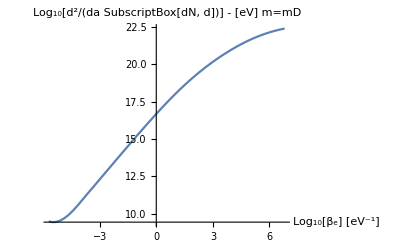

```mathematica
Plot[testinterfunc[["f"]][ξβ+Log10[me]],{ξβ,0-Log10[me],12.5-Log10[me]},PlotLabel->"Log_10[d^2/(da SubscriptBox[dN, d])] - [eV] m=mD",AxesLabel->{"Log_10[β_e] [eV^-1]"}]
```

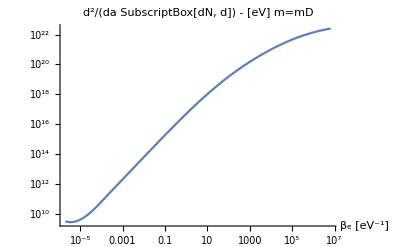

```mathematica
LogLogPlot[10^testinterfunc[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

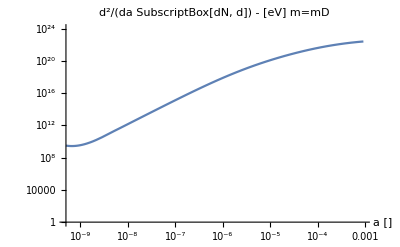

```mathematica
LogLogPlot[10^testinterfunc[["f"]][Log10[a^2/Tdt me]],{a,(Tdt/Td)^(1/2),(Tdt/TR)^(1/2)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^0,10^24}]
```

```mathematica
NIntegrate[1/2(Tdt/β)^(1/2)10^testinterfunc[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

1.37814×10^19

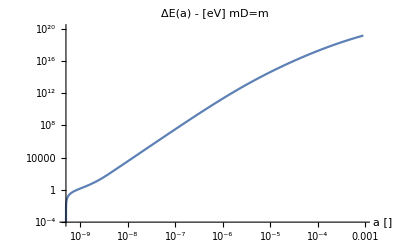

```mathematica
LogLogPlot[NIntegrate[1/2(Tdt/β)^(1/2)10^testinterfunc[["f"]][Log10[β me]],{β,1/Td,a^2/Tdt}],{a,(Tdt/Td)^(1/2),(Tdt/TR)^(1/2)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->{10^-4,10^20}]
```

mD = 2000 me

```mathematica
inter2000me=InterpolateEtransRate[2000 me,me,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.79026}. NIntegrate obtained 1.95798×10^6 and 85033.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.575423}. NIntegrate obtained 6.67997×10^6 and 1150.21 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξE near {ξE} = {0.454578}. NIntegrate obtained 1.41302×10^8 and 4232.74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],ξβ→{0.,0.963021,1.92604,2.88906,3.85208,4.81511,5.77813,6.74115,7.70417,8.66719,9.63021,10.5932,11.5563,12.5193},Points→{{0.,6.29181},{0.963021,6.82477},{1.92604,8.15015},{2.88906,9.58098},{3.85208,11.024},{4.81511,12.4681},{5.77813,13.9121},{6.74115,15.3548},{7.70417,16.7941},{8.66719,18.2229},{9.63021,19.6215},{10.5932,20.9417},{11.5563,22.097},{12.5193,23.0073}},mD→1000000000,m→500000,κ→1|>

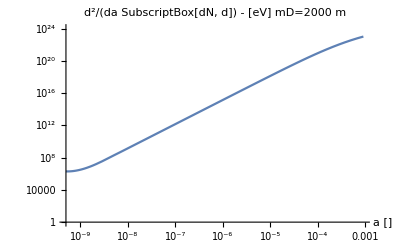

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a^2/Tdt me]],{a,(Tdt/Td)^(1/2),(Tdt/TR)^(1/2)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^0,10^24}]
```

```mathematica
NIntegrate[1/2(Tdt/β)^(1/2)10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

3.33359×10^19

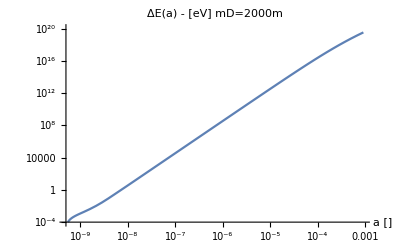

```mathematica
LogLogPlot[NIntegrate[1/2(Tdt/β)^(1/2)10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a^2/Tdt}],{a,(Tdt/Td)^(1/2),(Tdt/TR)^(1/2)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->{10^-4,10^20}]
```

#### Calculate ΔN_eff

```mathematica
ΔEeD=NIntegrate[1/2(Tdt/β)^(1/2)10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
ΔEpD=NIntegrate[1/2(Tdt/β)^(1/2)10^testinterfunc[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

3.33359×10^19

1.37814×10^19

```mathematica
TRSM = 0.26 (*[eV]*)
TD =κ^2 2/3 (ΔEeD + ΔEpD)/2
gstar=2 (TD/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
Solve[ΔNeff==0.1,κ][[8]]
```

0.26

1.57058×10^19 κ^2

2.66302×10^79 κ^8

1.17258×10^80 κ^8

{κ→7.35118×10^-11}

### Corrected after scaling issue

#### Constants and thermo dynamics

Temperature at decoupling

```mathematica
Td = 5 10^5; (*[eV] annihilation temperature*)
ad =(2 10^9)^-1; (*[] scale factor (~1/z) at annihilation*)
Tdt = N[Td ad] (*[eV] \tilde{T}_d the projected / extrapolated electron bath temperature today - if recombination / reionization etc. never happened*)
aR = (1100)^-1;(*[] scale factor ~ 1/z at recombination*)
TR = Tdt/aR (*[eV] temperature at recombination*)
```

0.00025

0.275

density today (and at decoupling)

```mathematica
Clear[ne]
n0 = 5 10^-13; (*[eV^3] number density today*)
ne[β_]:= n0(1/(β Tdt))^3
nd = n0 (Td/Tdt)^3
```

4.×10^15

```mathematica
ne[1/TR]
```

0.0006655

Thermal Quantities

```mathematica
me = 5 10^5; (*[eV] electron mass*)
pth =( (me Tdt)/(2 π))^(1/2); (*[eV] thermal de-broglie momentum*)
g = 4; (*[] dofs in SM electron*)
Z1[β_] := (g pth^3)/n0(1/(Tdt β))^(-3/2)(*[] whether classical is good or not*)
kF = N[(3 π^2 n0)^(1/3)] (*[eV] fermi momentum today*)
EF = kF^2/(2 me)
EFd = EF Td/Tdt (*[eV]fermi energy at decoupling*)
Degen = EF/Tdt (*Degeneracy of gas today - degeneracy is independent of time*)
```

0.000245545

6.02921×10^-14

0.000120584

2.41169×10^-10

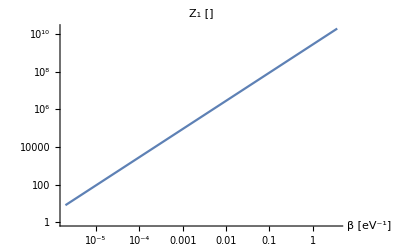

```mathematica
LogLogPlot[Z1[β],{β,1/Td,1/TR},PlotLabel->"Z_1 []",AxesLabel->{"β [eV^-1]"}]
```

```mathematica
Z1[1/me]
```

7.9367

Notice, fermi energy is about m/2. This is kinda interesting, numerology or dynamic?

fine structure constant

```mathematica
α=1/137;
```

Debeye Cutoff

```mathematica
Λ[β_]:= 4 π α (2π n0)/(me Tdt)(1/(β Tdt))^2
```

```mathematica
1/Td Λ[1/Td]
1/Tdt Λ[1/Tdt]
10^-5/TR Λ[10^-5/TR]
```

0.0184425

9.22124×10^-12

0.00101434

```mathematica
1/Td
10^-5/TR
```

1/500000

0.0000363636

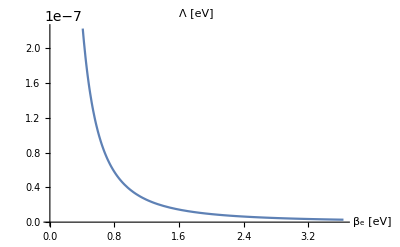

```mathematica
Plot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

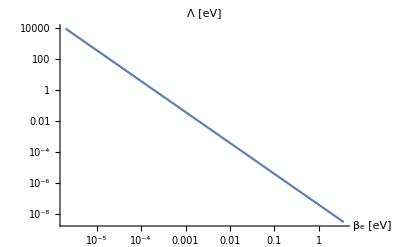

```mathematica
LogLogPlot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

#### compute hubble to convert to per a

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0inv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0= H0inv^-1 (*eV*) 
MP = (1.2 10^19 10^9)(*[eV] planck mass*)
```

1.51515×10^-33

1.2×10^28

```mathematica
N[200 10^-15 10^6]
```

2.×10^-7

```mathematica
ΛCDMrepl= {Ωk ->0.01,Ωr->9.4 10^-5, Ωm->0.32,ΩΛ->0.68,Ωb->0.05,Ωc->0.27}; (*[] ΛCDM density parameters*)
H[β_] :=H0(Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)/.ΛCDMrepl/.a->(Tdt β)
aH[β_] :=a H0 (Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)/.ΛCDMrepl/.a->(Tdt β)
```

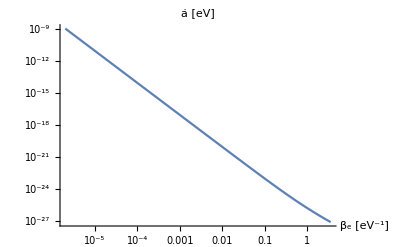

```mathematica
LogLogPlot[aH[β],{β,1/Td,1/TR},PlotLabel->"ȧ [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

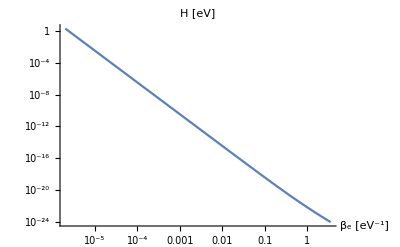

```mathematica
LogLogPlot[H[β],{β,1/Td,1/TR},PlotLabel->"H [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

#### Compare hubble and screening lengths - shows we can work in minkowski space

Screening energy - minimum energy transfered

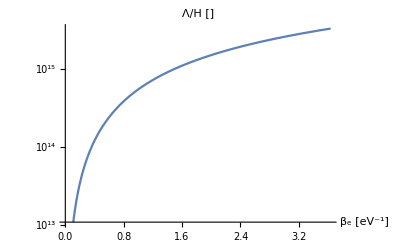

```mathematica
LogPlot[Λ[β]/H[β],{β,1/Td,1/TR},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

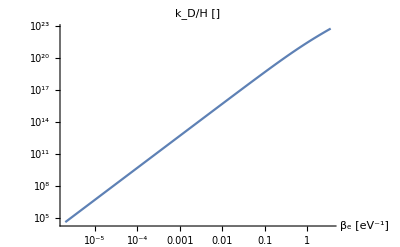

```mathematica
LogLogPlot[(√(2 me Λ[β]))/H[β],{β,1/Td,1/TR},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Temperature st. hubble is comparable to screening length

```mathematica
β/.Solve[(√(2 me Λ[β]))/H[β]==1,β][[3;;4]] (*[eV^-1]β*)
%^-1 (*[eV]photon temperatures*)
```

{5.74733×10^-8,1.86406×10^32}

{1.73994×10^7,5.36464×10^-33}

#### Numerically integrate, interpolate, numerically integrate

```mathematica
Clear[m,ESMt,Integrand]
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]];

(*Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]*)
(*Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESM_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}/.ESMt->ESM)*)
```

Ett^2/2-2 Ett (ESMt-ms+Λ)+(Λ (2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2))/(Ett+Λ)+(2 ESMt^2+2 ms^2+4 ESMt Λ-4 ms Λ+3 Λ^2) Log[Ett+Λ]

```mathematica
Clear[NumIntegrand]
(*NumIntegrand[mDt_,mt_,κ_,βt_,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.ESMt->1/β ξE + m/.{β->βt,m->mt,mD->mDt})*)
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/TR/.{m->mt,mD->mDt})*)
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[β],Qt->Z1[β]}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[m/ξβ NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}](*extra factor comes from jacobian*)

NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,∞},AccuracyGoal->Infinity]
ESMIntegral[me,me,1,me 10/Td]
```

1.2735×10^12

6.36748×10^16

Interpolate

```mathematica
(*InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Abs[ESMIntegral[mD,m,κ,Interξβs[[i]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
Interpolation[InterPoints]
]*) (*above is not log interpolated*)
InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,RateFnofβ},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]
inter1me=InterpolateEtransRate[me,me,1]
```

<|f→InterpolatingFunction[…],ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,16.5408},{0.481511,16.5593},{0.963021,16.7828},{1.44453,17.0747},{1.92604,17.379},{2.40755,17.6806},{2.88906,17.9763},{3.37057,18.2655},{3.85208,18.5475},{4.3336,18.8185},{4.81511,19.0663},{5.29662,19.261},{5.77813,19.354},{6.25964,19.3178}},mD→500000,m→500000,κ→1|>

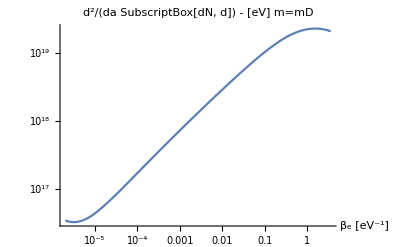

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

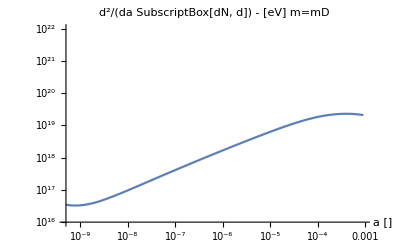

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^16,10^22}]
```

```mathematica
NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

1.90057×10^16

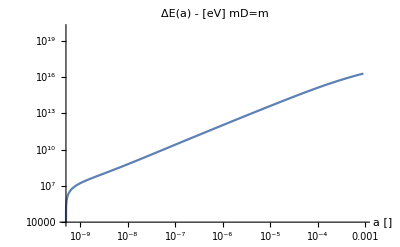

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->{10^4,10^20}]
```

mD = 2000 me

```mathematica
inter2000me=InterpolateEtransRate[2000 me,me,1]
```

<|f→InterpolatingFunction[…],ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,16.4368},{0.481511,17.0666},{0.963021,17.7795},{1.44453,18.4395},{1.92604,18.9997},{2.40755,19.474},{2.88906,19.887},{3.37057,20.2582},{3.85208,20.5994},{4.3336,20.9146},{4.81511,21.1966},{5.29662,21.4184},{5.77813,21.5335},{6.25964,21.5155}},mD→1000000000,m→500000,κ→1|>

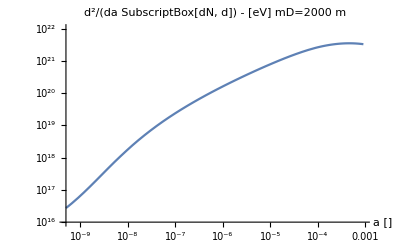

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^16,10^22}]
```

```mathematica
NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

2.8962×10^18

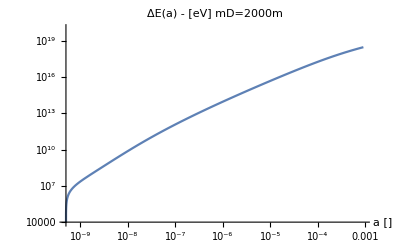

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->{10^4,10^20}]
```

#### Calculate ΔN_eff - my ham handed way

```mathematica
ΔEpD=0NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD=NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

0.

1.90057×10^16

```mathematica
TRSM = TR(*[eV]*)
TD =κ^2 2/3 (ΔEeD + ΔEpD)/1
gstar=2 (TD/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
Solve[ΔNeff==0.1,κ][[8]]
```

0.275

1.26705×10^16 κ^2

9.01309×10^66 κ^8

3.96865×10^67 κ^8

{κ→2.66176×10^-9}

#### Calculate ΔN_eff - David’s way

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

2.8962×10^18

1.90057×10^16

```mathematica
TRSM = TR(*[eV]*)
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

0.275

```mathematica
N[Simplify[Solve[0==-nD Etot+ nD 3 TDn + π^2/15 TDn^4,TDn]]];
(TDn/.%)^4/.nD->1/.Etot->10^10
```

{1.51982×10^10-1600.89 ⅈ,1.51982×10^10+0.000019684 ⅈ,1.51982×10^10+0.000034447 ⅈ,1.51982×10^10+1600.89 ⅈ}

```mathematica
Plot[-nD Etot+ nD 3 TDn + π^2/15 TDn^4/.Etot->10^19/.nD->1 ,{TDn,0,70000},PlotRange->All]
```

-Graphics-

```mathematica
Clear[Findroot]
Findroot[f_,f0_:0,n_:20,ofmmin_:0,ofmmax_:10]:=Module[{xmin,interval,mid},
			(*This function finds the root of E(2R,κ) via binary search with a fixed number of iterations
			Input:
				ofmmin - the order of magnitude to initialize the search (f >= 10^offmin)
			  ofmmax - the maximum order of magnitude(f <= 10^offmax)
			  n - number of iterations
			  f0 - value being solved for

			Output:
					xmin - root of f
					fmin - the value of the function at the root to given precision
			*)

		interval={ofmmin,ofmmax};
		mid=0;
		 Do[mid = (interval[[2]]+interval[[1]])/2;
			interval =If[f[10^mid]-f0<0,{mid,interval[[2]]},{interval[[1]],mid}],
			{i,n}
		];
		xmin = N[10^mid];
			<|"root"->xmin,"f[root]"->N[fD[10^mid]],"frac rem"->N[(fD[10^mid]-f0)/f0]|>
	]
```

```mathematica
Clear[fD,f]
fD[T_,nD_:1]:=nD 3 T + π^2/15 T^4
(*Findroot[f[#,1],]*)
```

```mathematica
TDR[nD_,ED_]:=Findroot[fD[#,nD]&,nD ED][["root"]]
```

```mathematica
TDR[10^1,ΔEtot]
```

81587.4

```mathematica
InternDs= Subdivide[-15,0,15]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TDInterPoints=Table[{InternDs[[i]],Log10[Abs[TDR[10^InternDs[[i]],ΔEtot]]]},{i,Length[InternDs]}] (*Abs since numerical instability at early times*)
TDfnofnD=Interpolation[TDInterPoints]
```

{{-15,0.911608},{-14,1.16162},{-13,1.41162},{-12,1.66162},{-11,1.91161},{-10,2.16161},{-9,2.41162},{-8,2.66162},{-7,2.91162},{-6,3.16161},{-5,3.41161},{-4,3.66162},{-3,3.91162},{-2,4.16162},{-1,4.41161},{0,4.66161}}

InterpolatingFunction[…]

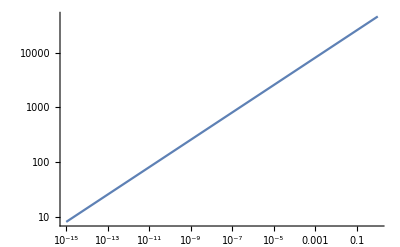

```mathematica
LogLogPlot[10^TDfnofnD[Log10[nDt]],{nDt,10^-15,1}]
```

```mathematica
gstar=2 (TDR/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
constraint = 0.1
Solve[ΔNeff==constraint,κ]
Simplify[(κ/.%[[2]])^2 nD]
```

349.703 TDR^4

1539.81 TDR^4

0.1

{}

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

nD (κ/.{}⟦2⟧)^2

```mathematica
N[3/(8 π)]((1.2 10^19 10^9))^2
```

1.71887×10^55

(7^(1/8) c^(1/8) √TSM)/(22^(1/6) √Tdark)

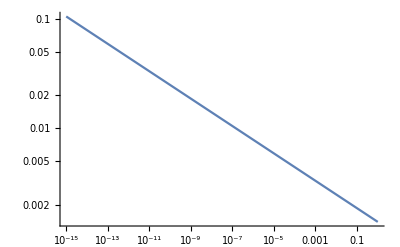

```mathematica
κmin =PowerExpand[ κ/.Solve[c==κ^8 gs 8/7(11/4)^(4/3),κ][[4]]/.gs ->2( Tdark/TSM)^4]
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

```mathematica
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

-Graphics-

```mathematica
TDR[1,1]
```

1.00002

```mathematica
Solve[nD 3 TDn == π^2/15 TDn^4,nD]
```

{{nD→(π^2 TDn^3)/45}}

#### n0 check

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
```

0.67

4.9379×10^-6

4.9379

```mathematica
Ωb= 0.05 
ρb = Ωb ρcritbaumannm
```

0.05

0.246895

see https://arxiv.org/pdf/1303.5076.pdf 

so baumann agrees with WMAP, our previous calculation is okay

```mathematica
ρcritbaumanneV = n0/0.05 2000 me
```

0.01

```mathematica
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
```

1000500000

0.00270135

```mathematica
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)
```

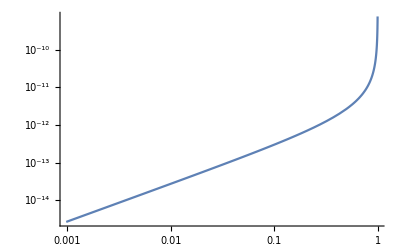

```mathematica
LogLogPlot[nD0[fDt,mSMtot],{fDt,0,1}]
```

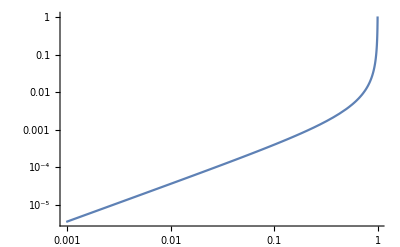

```mathematica
LogLogPlot[nD0[fDt,mSMtot]/aR^3,{fDt,0,1}]
```

### Corrected after Hubble issue

```mathematica
4 π Integrate[p^2/(2π)^3 E^(- β p^2/(2 m)),{p,0,∞}]
FullSimplify[Normal[%]]
```

ConditionalExpression[1/(2 √2 π^(3/2) (β/m)^(3/2)), Re[β/m]>0]

1/(2 √2 π^(3/2) (β/m)^(3/2))

#### Constants and thermo dynamics

```mathematica
Tdt
```

0.00025

Temperature at decoupling

```mathematica
Td = 5 10^5; (*[eV] annihilation temperature*)
ad =(2 10^9)^-1; (*[] scale factor (~1/z) at annihilation*)
Tdt = N[Td ad] (*[eV] \tilde{T}_d the projected / extrapolated electron bath temperature today - if recombination / reionization etc. never happened*)
aR = (1100)^-1;(*[] scale factor ~ 1/z at recombination*)
TR = Tdt/aR (*[eV] temperature at recombination*)
```

0.00025

0.275

density today (and at decoupling)

```mathematica
Clear[ne]
n0 = 5 10^-13; (*[eV^3] number density today*)
ne[β_]:= n0(1/(β Tdt))^3
nd = n0 (Td/Tdt)^3
```

4.×10^15

```mathematica
ne[1/TR]
```

0.0006655

Thermal Quantities

```mathematica
me = 5 10^5; (*[eV] electron mass*)
pth =( (me Tdt)/(2 π))^(1/2); (*[eV] thermal de-broglie momentum*)
g = 4; (*[] dofs in SM electron*)
Z1[β_] := (g pth^3)/n0(1/(Tdt β))^(-3/2)(*[] whether classical is good or not*)
kF = N[(3 π^2 n0)^(1/3)] (*[eV] fermi momentum today*)
EF = kF^2/(2 me)
EFd = EF Td/Tdt (*[eV]fermi energy at decoupling*)
Degen = EF/Tdt (*Degeneracy of gas today - degeneracy is independent of time*)
```

0.000245545

6.02921×10^-14

0.000120584

2.41169×10^-10

```mathematica
LogLogPlot[Z1[β],{β,1/Td,1/TR},PlotLabel->"Z_1 []",AxesLabel->{"β [eV^-1]"}]
```

-Graphics-

```mathematica
Z1[1/me]
```

7.9367

Notice, fermi energy is about m/2. This is kinda interesting, numerology or dynamic?

fine structure constant

Debeye Cutoff

```mathematica
Λ[β_]:= 4 π α (2π n0)/(me Tdt)(1/(β Tdt))^2
```

```mathematica
1/Td Λ[1/Td]
1/Tdt Λ[1/Tdt]
10^-5/TR Λ[10^-5/TR]
```

0.0184425

9.22124×10^-12

0.00101434

```mathematica
1/Td
10^-5/TR
```

1/500000

0.0000363636

```mathematica
Plot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

-Graphics-

```mathematica
LogLogPlot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

-Graphics-

#### compute hubble to convert to per a

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0inv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0= H0inv^-1 (*eV*) 
(*MP = (1.2 10^19 10^9)*)(*[eV] planck mass*)
```

1.51515×10^-33

```mathematica
N[200 10^-15 10^6]
```

2.×10^-7

```mathematica
ΛCDMrepl= {Ωk ->0.01,Ωr->9.4 10^-5, Ωm->0.32,ΩΛ->0.68,Ωb->0.05,Ωc->0.27}; (*[] ΛCDM density parameters*)
H[β_] :=H0(Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
aH[β_] :=a H0 (Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
```

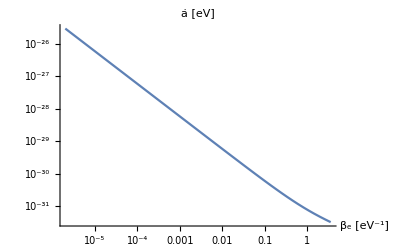

```mathematica
LogLogPlot[aH[β],{β,1/Td,1/TR},PlotLabel->"ȧ [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

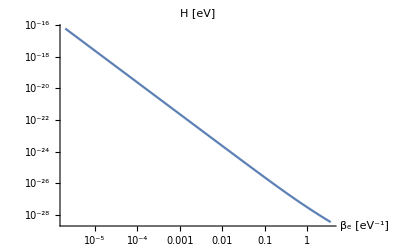

```mathematica
LogLogPlot[H[β],{β,1/Td,1/TR},PlotLabel->"H [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

#### Compare hubble and screening lengths - shows we can work in minkowski space

Screening energy - minimum energy transfered

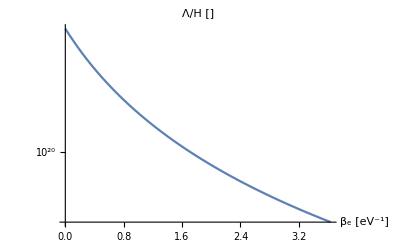

```mathematica
LogPlot[Λ[β]/H[β],{β,1/Td,1/TR},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

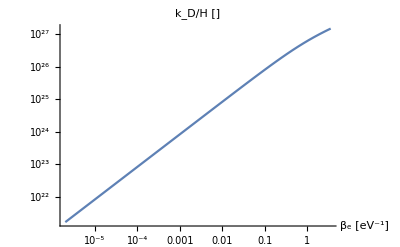

```mathematica
LogLogPlot[(√(2 me Λ[β]))/H[β],{β,1/Td,1/TR},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Temperature st. hubble is comparable to screening length

```mathematica
β/.Solve[(√(2 me Λ[β]))/H[β]==1,β][[3;;4]] (*[eV^-1]β*)
%^-1 (*[eV]photon temperatures*)
```

{1.22381×10^-27,1.53714×10^32}

{8.17118×10^26,6.50558×10^-33}

#### Numerically integrate, interpolate, numerically integrate

```mathematica
Clear[m,ESMt,Integrand]
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]];

(*Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]*)
(*Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESM_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}/.ESMt->ESM)*)
```

Ett^2/2-2 Ett (ESMt-ms+Λ)+(Λ (2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2))/(Ett+Λ)+(2 ESMt^2+2 ms^2+4 ESMt Λ-4 ms Λ+3 Λ^2) Log[Ett+Λ]

```mathematica
Clear[NumIntegrand]
(*NumIntegrand[mDt_,mt_,κ_,βt_,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.ESMt->1/β ξE + m/.{β->βt,m->mt,mD->mDt})*)
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/TR/.{m->mt,mD->mDt})*)
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[β],Qt->Z1[β]}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[m/ξβ NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}](*extra factor comes from jacobian*)

NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,∞},AccuracyGoal->Infinity]
ESMIntegral[me,me,1,me 10/Td]
```

4.93884×10^26

2.46942×10^31

Interpolate

```mathematica
(*InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Abs[ESMIntegral[mD,m,κ,Interξβs[[i]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
Interpolation[InterPoints]
]*) (*above is not log interpolated*)
InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,ΔEtransfered},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
ΔEtransfered = NIntegrate[Tdt 10^RateLogFnofβ[Log10[β me]],{β,1/Td,1/TR}];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ΔEtot"->ΔEtransfered,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]
inter1me=InterpolateEtransRate[me,me,1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→9.51638×10^23,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.1295},{0.481511,32.1849},{0.963021,31.4454},{1.44453,30.7743},{1.92604,30.1155},{2.40755,29.4542},{2.88906,28.787},{3.37057,28.1138},{3.85208,27.4346},{4.3336,26.7478},{4.81511,26.0476},{5.29662,25.3195},{5.77813,24.5392},{6.25964,23.6932}},mD→500000,m→500000,κ→1|>

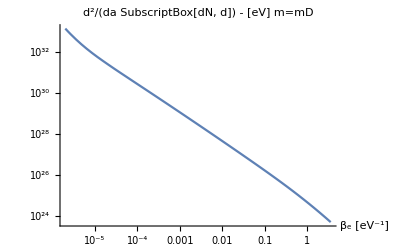

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

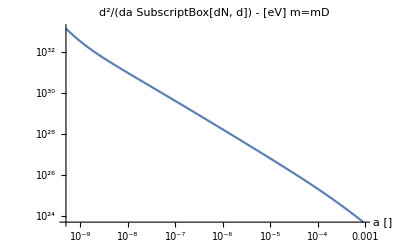

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"}]
```

```mathematica
NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
Tdt
```

0.00025

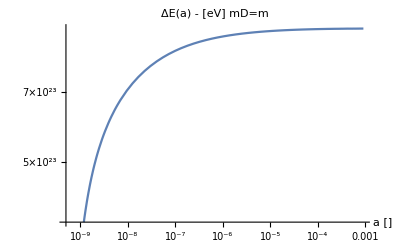

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"}]
```

mD = 2000 me

```mathematica
inter2000me=InterpolateEtransRate[2000 me,me,1]
```

<|f→InterpolatingFunction[…],ΔEtot→1.66481×10^25,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.0254},{0.481511,32.6922},{0.963021,32.4421},{1.44453,32.139},{1.92604,31.7363},{2.40755,31.2476},{2.88906,30.6978},{3.37057,30.1065},{3.85208,29.4864},{4.3336,28.8438},{4.81511,28.1779},{5.29662,27.4768},{5.77813,26.7187},{6.25964,25.891}},mD→1000000000,m→500000,κ→1|>

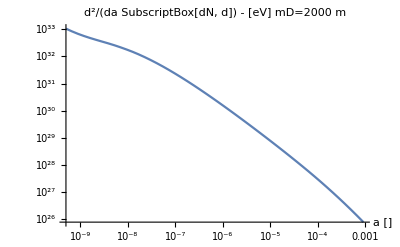

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"}]
```

```mathematica
NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

1.66481×10^25

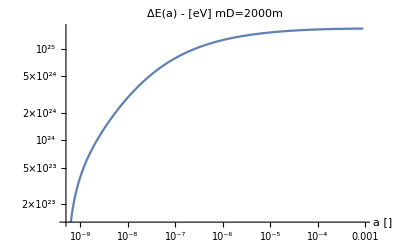

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"}]
```

#### Interpolate total energy transferred as a function of mass

```mathematica
InterpolateTotEtrans[mD_:{10^-3 me,10^4 me},m_:me,κ_:1]:=Module[{n=Round[Log10[mD[[2]]]-Log10[mD[[1]]]]+1,Interms,TableofInters,ΔEPoints,TotLogFnofm},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interms= N[Subdivide[Log10[mD[[2]]],Log10[mD[[1]]],n]]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TableofInters=Table[InterpolateEtransRate[10^Interms[[i]],m,κ],{i,Length[Interms]}];(*table of interpolations*)
ΔEPoints=Table[{Interms[[i]],Log10[TableofInters[[i]][["ΔEtot"]]]},{i,Length[Interms]}] ;(*Abs since numerical instability at early times*)
TotLogFnofm=Interpolation[ΔEPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->TotLogFnofm,"Inters"->TableofInters,"Points"->ΔEPoints,"Interms"->Interms,"mD"->mD,"m"->m,"κ"->κ|>
]
```

```mathematica
ΔEtottest =InterpolateTotEtrans[]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.000207602}. NIntegrate obtained 3.54231×10^25 and 5.85693×10^20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.000205967}. NIntegrate obtained 1.36851×10^25 and 2.45521×10^20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000674079}. NIntegrate obtained 4.67803×10^24 and 1.9385×10^19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],Inters→{<|f→InterpolatingFunction[…],ΔEtot→3.54231×10^25,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,32.6292},{0.481511,32.3542},{0.963021,32.2465},{1.44453,32.1401},{1.92604,31.9237},{2.40755,31.5779},{2.88906,31.1272},{3.37057,30.6021},{3.85208,30.0262},{4.3336,29.4138},{4.81511,28.7691},{5.29662,28.0836},{5.77813,27.3372},{6.25964,26.5186}},mD→5.×10^9,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.36851×10^25,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.0836},{0.481511,32.7309},{0.963021,32.4412},{1.44453,32.0936},{1.92604,31.6547},{2.40755,31.1406},{2.88906,30.5738},{3.37057,29.9711},{3.85208,29.3433},{4.3336,28.6952},{4.81511,28.0253},{5.29662,27.3212},{5.77813,26.5607},{6.25964,25.7312}},mD→6.66761×10^8,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→4.67803×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.1114},{0.481511,32.6511},{0.963021,32.1891},{1.44453,31.678},{1.92604,31.1177},{2.40755,30.5208},{2.88906,29.8983},{3.37057,29.2576},{3.85208,28.603},{4.3336,27.9355},{4.81511,27.2509},{5.29662,26.5354},{5.77813,25.7658},{6.25964,24.9289}},mD→8.8914×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.25753×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,32.7929},{0.481511,32.2294},{0.963021,31.662},{1.44453,31.0683},{1.92604,30.4503},{2.40755,29.8136},{2.88906,29.1633},{3.37057,28.5024},{3.85208,27.8328},{4.3336,27.1536},{4.81511,26.4597},{5.29662,25.7368},{5.77813,24.961},{6.25964,24.1188}},mD→1.18569×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→4.84143×10^23,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,32.7224},{0.481511,31.8775},{0.963021,31.194},{1.44453,30.5454},{1.92604,29.8962},{2.40755,29.2396},{2.88906,28.5752},{3.37057,27.9039},{3.85208,27.226},{4.3336,26.5403},{4.81511,25.8411},{5.29662,25.1138},{5.77813,24.3342},{6.25964,23.4888}},mD→1.58114×10^6,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→2.91175×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.5518},{0.481511,32.6627},{0.963021,31.9565},{1.44453,31.2991},{1.92604,30.6461},{2.40755,29.9875},{2.88906,29.3219},{3.37057,28.6498},{3.85208,27.9714},{4.3336,27.2852},{4.81511,26.5856},{5.29662,25.8579},{5.77813,25.078},{6.25964,24.2324}},mD→210848.,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.25648×10^26,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,35.2379},{0.481511,34.6542},{0.963021,34.0754},{1.44453,33.474},{1.92604,32.8506},{2.40755,32.2103},{2.88906,31.5573},{3.37057,30.8944},{3.85208,30.2232},{4.3336,29.5428},{4.81511,28.8479},{5.29662,28.1241},{5.77813,27.3476},{6.25964,26.5049}},mD→28117.1,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→7.00077×10^28,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,37.3328},{0.481511,36.8576},{0.963021,36.3764},{1.44453,35.8495},{1.92604,35.278},{2.40755,34.6736},{2.88906,34.0459},{3.37057,33.4015},{3.85208,32.7442},{4.3336,32.0747},{4.81511,31.3885},{5.29662,30.6718},{5.77813,29.9011},{6.25964,29.0633}},mD→3749.47,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.18741×10^31,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,39.1139},{0.481511,38.7466},{0.963021,38.4292},{1.44453,38.0522},{1.92604,37.5903},{2.40755,37.0603},{2.88906,36.4828},{3.37057,35.873},{3.85208,35.2402},{4.3336,34.5887},{4.81511,33.9162},{5.29662,33.2102},{5.77813,32.4481},{6.25964,31.6174}},mD→500.,m→500000,κ→1|>},Points→{{9.69897,25.5493},{8.82397,25.1362},{7.94897,24.6701},{7.07397,24.0995},{6.19897,23.685},{5.32397,24.4642},{4.44897,26.5127},{3.57397,28.8451},{2.69897,31.0746}},Interms→{9.69897,8.82397,7.94897,7.07397,6.19897,5.32397,4.44897,3.57397,2.69897},mD→{500,5000000000},m→500000,κ→1|>

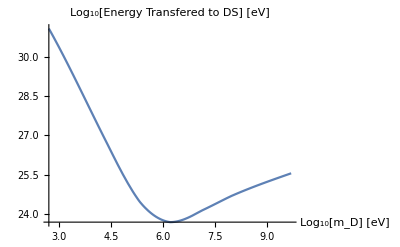

```mathematica
Plot[ΔEtottest[["f"]][mD],{mD,Log10[10^-3 me],Log10[10^4 me]},PlotLabel->"Log_10[Energy Transfered to DS] [eV]",AxesLabel->{"Log_10[m_D] [eV]"}]
```

#### Calculate ΔN_eff - my ham handed way

```mathematica
ΔEpD=0NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD=NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
TRSM = TR(*[eV]*)
TD =κ^2 2/3 (ΔEeD + ΔEpD)/1
gstar=2 (TD/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
Solve[ΔNeff==0.1,κ][[8]]
```

0.275

6.34425×10^23 κ^2

5.66528×10^97 κ^8

2.49454×10^98 κ^8

{κ→3.76163×10^-13}

#### Calculate ΔN_eff - David’s way

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

1.66481×10^25

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
TRSM = TR(*[eV]*)
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

0.275

```mathematica
N[Simplify[Solve[0==-nD Etot+ nD 3 TDn + π^2/15 TDn^4,TDn]]];
(TDn/.%)^4/.nD->1/.Etot->10^10
```

{1.51982×10^10-1600.89 ⅈ,1.51982×10^10+0.000019684 ⅈ,1.51982×10^10+0.000034447 ⅈ,1.51982×10^10+1600.89 ⅈ}

```mathematica
Plot[-nD Etot+ nD 3 TDn + π^2/15 TDn^4/.Etot->10^19/.nD->1 ,{TDn,0,70000},PlotRange->All]
```

-Graphics-

```mathematica
Clear[Findroot]
Findroot[f_,f0_:0,n_:20,ofmmin_:0,ofmmax_:10]:=Module[{xmin,interval,mid},
			(*This function finds the root of E(2R,κ) via binary search with a fixed number of iterations
			Input:
				ofmmin - the order of magnitude to initialize the search (f >= 10^offmin)
			  ofmmax - the maximum order of magnitude(f <= 10^offmax)
			  n - number of iterations
			  f0 - value being solved for

			Output:
					xmin - root of f
					fmin - the value of the function at the root to given precision
			*)

		interval={ofmmin,ofmmax};
		mid=0;
		 Do[mid = (interval[[2]]+interval[[1]])/2;
			interval =If[f[10^mid]-f0<0,{mid,interval[[2]]},{interval[[1]],mid}],
			{i,n}
		];
		xmin = N[10^mid];
			<|"root"->xmin,"f[root]"->N[fD[10^mid]],"frac rem"->N[(fD[10^mid]-f0)/f0]|>
	]
```

```mathematica
Clear[fD,f]
fD[T_,nD_:1]:=nD 3 T + π^2/15 T^4
(*Findroot[f[#,1],]*)
```

```mathematica
TDR[nD_,ED_]:=Findroot[fD[#,nD]&,nD ED][["root"]]
```

```mathematica
TDR[10^1,ΔEtot]
```

4.04406×10^6

```mathematica
InternDs= Subdivide[-15,0,15]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TDInterPoints=Table[{InternDs[[i]],Log10[Abs[TDR[10^InternDs[[i]],ΔEtot]]]},{i,Length[InternDs]}] (*Abs since numerical instability at early times*)
TDfnofnD=Interpolation[TDInterPoints]
```

{{-15,2.60682},{-14,2.85682},{-13,3.10683},{-12,3.35683},{-11,3.60682},{-10,3.85682},{-9,4.10682},{-8,4.35683},{-7,4.60683},{-6,4.85682},{-5,5.10682},{-4,5.35682},{-3,5.60683},{-2,5.85683},{-1,6.10682},{0,6.35682}}

InterpolatingFunction[…]

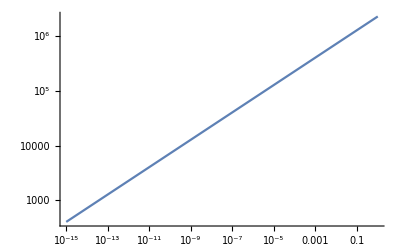

```mathematica
LogLogPlot[10^TDfnofnD[Log10[nDt]],{nDt,10^-15,1}]
```

```mathematica
gstar=2 (TDR/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
constraint = 0.1
Solve[ΔNeff==constraint,κ]
Simplify[(κ/.%[[2]])^2 nD]
```

349.703 TDR^4

1539.81 TDR^4

0.1

{}

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

nD (κ/.{}⟦2⟧)^2

```mathematica
N[3/(8 π)]((1.2 10^19 10^9))^2
```

1.71887×10^55

(7^(1/8) c^(1/8) √TSM)/(22^(1/6) √Tdark)

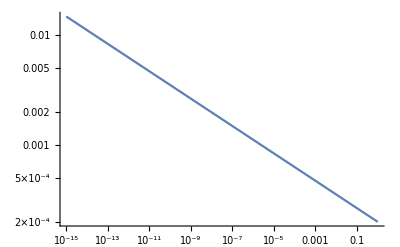

```mathematica
κmin =PowerExpand[ κ/.Solve[c==κ^8 gs 8/7(11/4)^(4/3),κ][[4]]/.gs ->2( Tdark/TSM)^4]
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

```mathematica
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

-Graphics-

```mathematica
TDR[1,1]
```

1.00002

```mathematica
Solve[nD 3 TDn == π^2/15 TDn^4,nD]
```

{{nD→(π^2 TDn^3)/45}}

#### n0 check

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
```

0.67

4.9379×10^-6

4.9379

```mathematica
Ωb= 0.05 
ρb = Ωb ρcritbaumannm
```

0.05

0.246895

see https://arxiv.org/pdf/1303.5076.pdf 

so baumann agrees with WMAP, our previous calculation is okay

```mathematica
ρcritbaumanneV = n0/0.05 2000 me
```

0.01

```mathematica
ρcritbaumannm eVm^3/.eVm -> N[200 10^-15 10^6]
```

3.95032×10^-20

```mathematica
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
```

1000500000

0.00270135

```mathematica
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)
```

```mathematica
LogLogPlot[nD0[fDt,mSMtot],{fDt,0,1}]
```

-Graphics-

```mathematica
LogLogPlot[nD0[fDt,mSMtot]/aR^3,{fDt,0,1}]
```

-Graphics-

```mathematica
ρcritbaumanneV
```

0.01

#### Neff correct way

```mathematica
gstar=2 (TDRt/TR)^4(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7(11/4)^(4/3)gstar (*[]*)
constraint = 0.1 (*[]constraint on ΔNeff*)
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] (*[eV]upper bound on TD at recombination*)
```

349.703 TDRt^4

1539.81 TDRt^4

0.1

0.0897704

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

1.66481×10^25

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
Clear[Ωb]
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
(*nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)*)
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD
nDR[fD_,mDMtot_] := 1/aR^3 nD0[fD,mDMtot]
```

1000500000

0.00270135

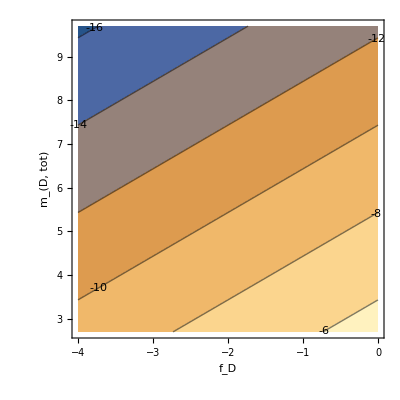

```mathematica
ContourPlot[Log10[nD0[10^fDt,10^mDM]],{fDt,-4,0},{mDM,Log10[10^-3 me],Log10[10^4 me]},ContourLabels->True,FrameLabel->{"f_D","m_(D, tot)"}]
```

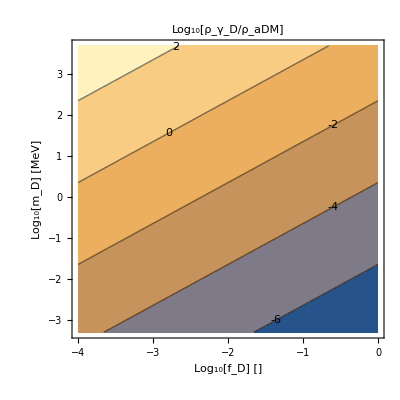

```mathematica
ContourPlot[Log10[π^2/45 TDRconst^3/nDR[10^fDt,10^(mDM+6)]],{fDt,-4,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"},PlotLabel->"Log_10[ρ_γ_D/ρ_aDM]"]
```

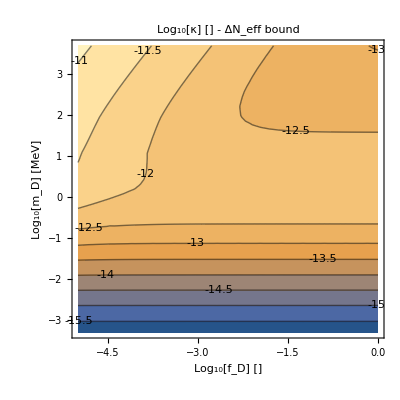

```mathematica
ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtottest[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]
```

```mathematica
Tdt
```

0.00025

### Corrected after n0 issue

#### Constants and thermo dynamics

```mathematica
Tdt
```

0.00025

Temperature at decoupling

```mathematica
Td = 5 10^5; (*[eV] annihilation temperature*)
ad =(2 10^9)^-1; (*[] scale factor (~1/z) at annihilation*)
Tdt = N[Td ad] (*[eV] \tilde{T}_d the projected / extrapolated electron bath temperature today - if recombination / reionization etc. never happened*)
aR = (1100)^-1;(*[] scale factor ~ 1/z at recombination*)
TR = Tdt/aR (*[eV] temperature at recombination*)
```

0.00025

0.275

density today (and at decoupling)

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
eVm = N[200 10^-15 10^6] (*[eV m] = 1 follows from 1 = 200 MeV fm*)
```

0.67

4.9379×10^-6

4.9379

2.×10^-7

```mathematica
Clear[ne,n0]
n0 = Ωb ρcritbaumannm eVm^3 /.ΛCDMrepl (*[eV^3] number density today*)
ne[β_]:= n0(1/(β Tdt))^3
nd = n0 (Td/Tdt)^3
```

1.97516×10^-21

1.58013×10^7

```mathematica
ne[1/TR]
```

0.0006655

Thermal Quantities

```mathematica
me = 5 10^5; (*[eV] electron mass*)
pth =( (me Tdt)/(2 π))^(1/2); (*[eV] thermal de-broglie momentum*)
g = 4; (*[] dofs in SM electron*)
Z1[β_] := (g pth^3)/n0(1/(Tdt β))^(-3/2)(*[] whether classical is good or not*)
kF = N[(3 π^2 n0)^(1/3)] (*[eV] fermi momentum today*)
EF = kF^2/(2 me)
EFd = EF Td/Tdt (*[eV]fermi energy at decoupling*)
Degen = EF/Tdt (*Degeneracy of gas today - degeneracy is independent of time*)
```

3.88157×10^-7

1.50666×10^-19

3.01332×10^-10

6.02664×10^-16

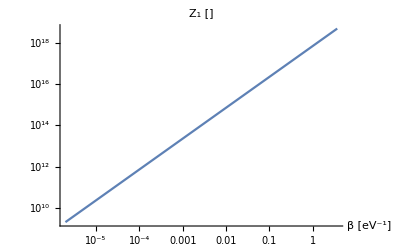

```mathematica
LogLogPlot[Z1[β],{β,1/Td,1/TR},PlotLabel->"Z_1 []",AxesLabel->{"β [eV^-1]"}]
```

```mathematica
Z1[1/me]
```

7.9367

Notice, fermi energy is about m/2. This is kinda interesting, numerology or dynamic?

fine structure constant

Debeye Cutoff

```mathematica
Λ[β_]:= 4 π α (2π n0)/(me Tdt)(1/(β Tdt))^2
```

```mathematica
1/Td Λ[1/Td]
1/Tdt Λ[1/Tdt]
10^-5/TR Λ[10^-5/TR]
```

0.0184425

9.22124×10^-12

0.00101434

```mathematica
1/Td
10^-5/TR
```

1/500000

0.0000363636

```mathematica
Plot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

-Graphics-

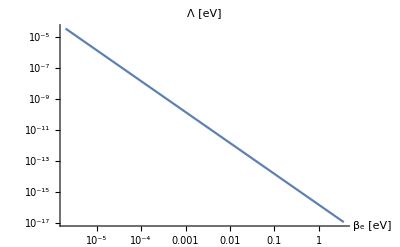

```mathematica
LogLogPlot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

#### compute hubble to convert to per a

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0inv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0= H0inv^-1 (*eV*) 
(*MP = (1.2 10^19 10^9)*)(*[eV] planck mass*)
```

1.51515×10^-33

```mathematica
N[200 10^-15 10^6]
```

2.×10^-7

```mathematica
ΛCDMrepl= {Ωk ->0.01,Ωr->9.4 10^-5, Ωm->0.32,ΩΛ->0.68,Ωb->0.05,Ωc->0.27}; (*[] ΛCDM density parameters*)
H[β_] :=H0(Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
aH[β_] :=a H0 (Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
```

```mathematica
LogLogPlot[aH[β],{β,1/Td,1/TR},PlotLabel->"ȧ [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

```mathematica
LogLogPlot[H[β],{β,1/Td,1/TR},PlotLabel->"H [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

#### Compare hubble and screening lengths - shows we can work in minkowski space

Screening energy - minimum energy transfered

```mathematica
LogPlot[Λ[β]/H[β],{β,1/Td,1/TR},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

Screening length (Debeye momentum) - minimum momentum transfered

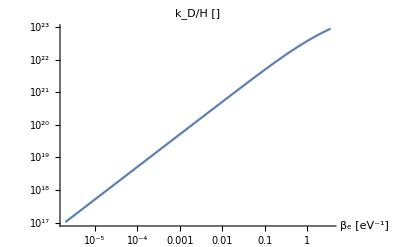

```mathematica
LogLogPlot[(√(2 me Λ[β]))/H[β],{β,1/Td,1/TR},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Temperature st. hubble is comparable to screening length

```mathematica
β/.Solve[(√(2 me Λ[β]))/H[β]==1,β][[3;;4]] (*[eV^-1]β*)
%^-1 (*[eV]photon temperatures*)
```

{1.22381×10^-27,1.53714×10^32}

{8.17118×10^26,6.50558×10^-33}

#### Numerically integrate, interpolate, numerically integrate

```mathematica
Clear[m,ESMt,Integrand]
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]];

(*Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]*)
(*Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESM_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}/.ESMt->ESM)*)
```

Ett^2/2-2 Ett (ESMt-ms+Λ)+(Λ (2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2))/(Ett+Λ)+(2 ESMt^2+2 ms^2+4 ESMt Λ-4 ms Λ+3 Λ^2) Log[Ett+Λ]

```mathematica
Clear[NumIntegrand]
(*NumIntegrand[mDt_,mt_,κ_,βt_,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.ESMt->1/β ξE + m/.{β->βt,m->mt,mD->mDt})*)
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/TR/.{m->mt,mD->mDt})*)
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[β],Qt->Z1[β]}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[m/ξβ NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}](*extra factor comes from jacobian*)

NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,∞},AccuracyGoal->Infinity]
ESMIntegral[me,me,1,me 10/Td]
```

4.93884×10^26

2.46942×10^31

Interpolate

```mathematica
(*InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Abs[ESMIntegral[mD,m,κ,Interξβs[[i]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
Interpolation[InterPoints]
]*) (*above is not log interpolated*)
InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,ΔEtransfered},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
ΔEtransfered = NIntegrate[Tdt 10^RateLogFnofβ[Log10[β m]],{β,1/Td,1/TR}];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ΔEtot"->ΔEtransfered,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]
inter1me=InterpolateEtransRate[me,me,1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1|>

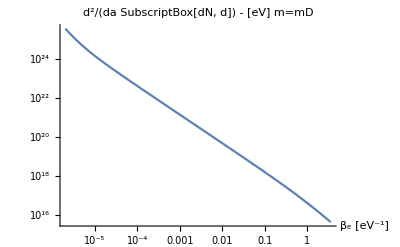

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

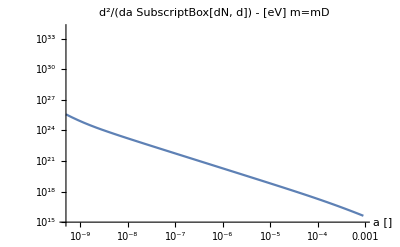

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

```mathematica
NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

2.07738×10^16

```mathematica
Tdt
```

0.00025

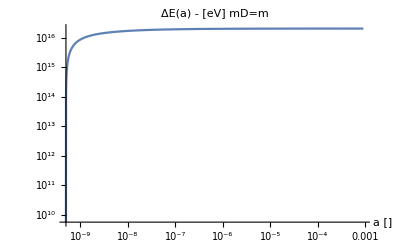

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

mD = 2000 me

```mathematica
inter2000me=InterpolateEtransRate[2000 me,me,1]
```

<|f→InterpolatingFunction[…],ΔEtot→2.53409×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.359},{0.481511,26.6604},{0.963021,25.9637},{1.44453,25.2668},{1.92604,24.5691},{2.40755,23.8701},{2.88906,23.1698},{3.37057,22.4682},{3.85208,21.7643},{4.3336,21.0561},{4.81511,20.3373},{5.29662,19.5925},{5.77813,18.7975},{6.25964,17.9383}},mD→1000000000,m→500000,κ→1|>

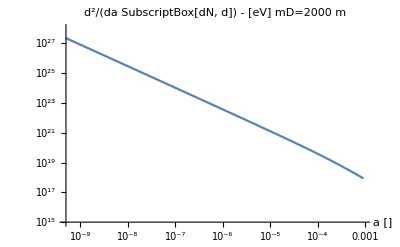

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

```mathematica
NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

2.53409×10^18

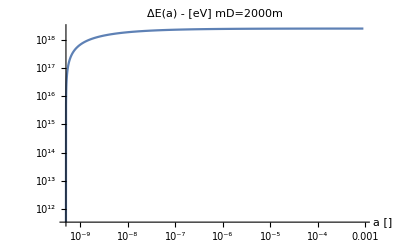

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

#### Interpolate total energy transferred as a function of mass

```mathematica
InterpolateTotEtrans[mD_:{10^-3 me,10^4 me},m_:me,κ_:1]:=Module[{n=Round[Log10[mD[[2]]]-Log10[mD[[1]]]]+1,Interms,TableofInters,ΔEPoints,TotLogFnofm},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interms= N[Subdivide[Log10[mD[[2]]],Log10[mD[[1]]],n]]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TableofInters=Table[InterpolateEtransRate[10^Interms[[i]],m,κ],{i,Length[Interms]}];(*table of interpolations*)
ΔEPoints=Table[{Interms[[i]],Log10[TableofInters[[i]][["ΔEtot"]]]},{i,Length[Interms]}] ;(*Abs since numerical instability at early times*)
TotLogFnofm=Interpolation[ΔEPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->TotLogFnofm,"Inters"->TableofInters,"Points"->ΔEPoints,"Interms"->Interms,"mD"->mD,"m"->m,"κ"->κ|>
]
```

```mathematica
ΔEtottest =InterpolateTotEtrans[]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.000202728}. NIntegrate obtained 3.81137×10^16 and 1.0023×10^14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 1.08532×10^16 and 6.11752×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 6.43939×10^16 and 6.87998×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],Inters→{<|f→InterpolatingFunction[…],ΔEtot→1.15169×10^19,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,28.0117},{0.481511,27.3157},{0.963021,26.6215},{1.44453,25.9272},{1.92604,25.2316},{2.40755,24.5346},{2.88906,23.8362},{3.37057,23.1361},{3.85208,22.4337},{4.3336,21.7268},{4.81511,21.0092},{5.29662,20.2656},{5.77813,19.4716},{6.25964,18.6133}},mD→5.×10^9,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.72834×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.1939},{0.481511,26.4947},{0.963021,25.7974},{1.44453,25.1},{1.92604,24.4017},{2.40755,23.7023},{2.88906,23.0017},{3.37057,22.2996},{3.85208,21.5954},{4.3336,20.8869},{4.81511,20.1678},{5.29662,19.4228},{5.77813,18.6276},{6.25964,17.7681}},mD→6.66761×10^8,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→2.56094×10^17,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.3693},{0.481511,25.6677},{0.963021,24.9678},{1.44453,24.268},{1.92604,23.5675},{2.40755,22.8661},{2.88906,22.1636},{3.37057,21.4599},{3.85208,20.7542},{4.3336,20.0444},{4.81511,19.3239},{5.29662,18.5778},{5.77813,17.7814},{6.25964,16.921}},mD→8.8914×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.81137×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5544},{0.481511,24.8415},{0.963021,24.1378},{1.44453,23.4357},{1.92604,22.7333},{2.40755,22.0302},{2.88906,21.3262},{3.37057,20.6211},{3.85208,19.9141},{4.3336,19.2031},{4.81511,18.4816},{5.29662,17.7344},{5.77813,16.9371},{6.25964,16.0758}},mD→1.18569×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.08532×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.2071},{0.481511,24.2847},{0.963021,23.5196},{1.44453,22.7988},{1.92604,22.0898},{2.40755,21.3839},{2.88906,20.6783},{3.37057,19.972},{3.85208,19.2641},{4.3336,18.5522},{4.81511,17.83},{5.29662,17.0821},{5.77813,16.2841},{6.25964,15.4222}},mD→1.58114×10^6,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→6.43939×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.0221},{0.481511,25.0552},{0.963021,24.2712},{1.44453,23.5442},{1.92604,22.8331},{2.40755,22.1264},{2.88906,21.4206},{3.37057,20.7142},{3.85208,20.0062},{4.3336,19.2942},{4.81511,18.5718},{5.29662,17.8239},{5.77813,17.0259},{6.25964,16.1639}},mD→210848.,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→9.27351×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.9478},{0.481511,27.2274},{0.963021,26.522},{1.44453,25.8192},{1.92604,25.1165},{2.40755,24.4132},{2.88906,23.709},{3.37057,23.0037},{3.85208,22.2966},{4.3336,21.5854},{4.81511,20.8638},{5.29662,20.1165},{5.77813,19.3191},{6.25964,18.4577}},mD→28117.1,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.46411×10^21,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,30.5012},{0.481511,29.7991},{0.963021,29.0989},{1.44453,28.3988},{1.92604,27.6981},{2.40755,26.9964},{2.88906,26.2937},{3.37057,25.5898},{3.85208,24.8839},{4.3336,24.1738},{4.81511,23.4532},{5.29662,22.7069},{5.77813,21.9104},{6.25964,21.0498}},mD→3749.47,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.31667×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.0764},{0.481511,32.3769},{0.963021,31.6792},{1.44453,30.9814},{1.92604,30.2828},{2.40755,29.5831},{2.88906,28.8822},{3.37057,28.1798},{3.85208,27.4754},{4.3336,26.7667},{4.81511,26.0474},{5.29662,25.3022},{5.77813,24.5068},{6.25964,23.6472}},mD→500.,m→500000,κ→1|>},Points→{{9.69897,19.0613},{8.82397,18.2376},{7.94897,17.4084},{7.07397,16.5811},{6.19897,16.0356},{5.32397,16.8088},{4.44897,18.9672},{3.57397,21.5396},{2.69897,24.1195}},Interms→{9.69897,8.82397,7.94897,7.07397,6.19897,5.32397,4.44897,3.57397,2.69897},mD→{500,5000000000},m→500000,κ→1|>

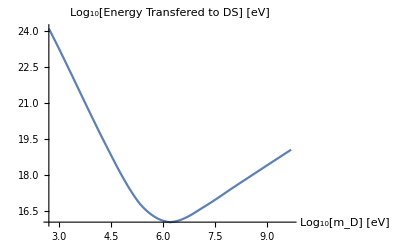

```mathematica
Plot[ΔEtottest[["f"]][mD],{mD,Log10[10^-3 me],Log10[10^4 me]},PlotLabel->"Log_10[Energy Transfered to DS] [eV]",AxesLabel->{"Log_10[m_D] [eV]"}]
```

#### Calculate ΔN_eff - my ham handed way

```mathematica
ΔEpD=0NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD=NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
TRSM = TR(*[eV]*)
TD =κ^2 2/3 (ΔEeD + ΔEpD)/1
gstar=2 (TD/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
Solve[ΔNeff==0.1,κ][[8]]
```

0.275

6.34425×10^23 κ^2

5.66528×10^97 κ^8

2.49454×10^98 κ^8

{κ→3.76163×10^-13}

#### Calculate ΔN_eff - v2

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

1.66481×10^25

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
TRSM = TR(*[eV]*)
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

0.275

```mathematica
N[Simplify[Solve[0==-nD Etot+ nD 3 TDn + π^2/15 TDn^4,TDn]]];
(TDn/.%)^4/.nD->1/.Etot->10^10
```

{1.51982×10^10-1600.89 ⅈ,1.51982×10^10+0.000019684 ⅈ,1.51982×10^10+0.000034447 ⅈ,1.51982×10^10+1600.89 ⅈ}

```mathematica
Plot[-nD Etot+ nD 3 TDn + π^2/15 TDn^4/.Etot->10^19/.nD->1 ,{TDn,0,70000},PlotRange->All]
```

-Graphics-

```mathematica
Clear[Findroot]
Findroot[f_,f0_:0,n_:20,ofmmin_:0,ofmmax_:10]:=Module[{xmin,interval,mid},
			(*This function finds the root of E(2R,κ) via binary search with a fixed number of iterations
			Input:
				ofmmin - the order of magnitude to initialize the search (f >= 10^offmin)
			  ofmmax - the maximum order of magnitude(f <= 10^offmax)
			  n - number of iterations
			  f0 - value being solved for

			Output:
					xmin - root of f
					fmin - the value of the function at the root to given precision
			*)

		interval={ofmmin,ofmmax};
		mid=0;
		 Do[mid = (interval[[2]]+interval[[1]])/2;
			interval =If[f[10^mid]-f0<0,{mid,interval[[2]]},{interval[[1]],mid}],
			{i,n}
		];
		xmin = N[10^mid];
			<|"root"->xmin,"f[root]"->N[fD[10^mid]],"frac rem"->N[(fD[10^mid]-f0)/f0]|>
	]
```

```mathematica
Clear[fD,f]
fD[T_,nD_:1]:=nD 3 T + π^2/15 T^4
(*Findroot[f[#,1],]*)
```

```mathematica
TDR[nD_,ED_]:=Findroot[fD[#,nD]&,nD ED][["root"]]
```

```mathematica
TDR[10^1,ΔEtot]
```

4.04406×10^6

```mathematica
InternDs= Subdivide[-15,0,15]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TDInterPoints=Table[{InternDs[[i]],Log10[Abs[TDR[10^InternDs[[i]],ΔEtot]]]},{i,Length[InternDs]}] (*Abs since numerical instability at early times*)
TDfnofnD=Interpolation[TDInterPoints]
```

{{-15,2.60682},{-14,2.85682},{-13,3.10683},{-12,3.35683},{-11,3.60682},{-10,3.85682},{-9,4.10682},{-8,4.35683},{-7,4.60683},{-6,4.85682},{-5,5.10682},{-4,5.35682},{-3,5.60683},{-2,5.85683},{-1,6.10682},{0,6.35682}}

InterpolatingFunction[…]

```mathematica
LogLogPlot[10^TDfnofnD[Log10[nDt]],{nDt,10^-15,1}]
```

-Graphics-

```mathematica
gstar=2 (TDR/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
constraint = 0.1
Solve[ΔNeff==constraint,κ]
Simplify[(κ/.%[[2]])^2 nD]
```

349.703 TDR^4

1539.81 TDR^4

0.1

{}

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

nD (κ/.{}⟦2⟧)^2

```mathematica
N[3/(8 π)]((1.2 10^19 10^9))^2
```

1.71887×10^55

```mathematica
κmin =PowerExpand[ κ/.Solve[c==κ^8 gs 8/7(11/4)^(4/3),κ][[4]]/.gs ->2( Tdark/TSM)^4]
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

(7^(1/8) c^(1/8) √TSM)/(22^(1/6) √Tdark)

-Graphics-

```mathematica
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

-Graphics-

```mathematica
TDR[1,1]
```

1.00002

```mathematica
Solve[nD 3 TDn == π^2/15 TDn^4,nD]
```

{{nD→(π^2 TDn^3)/45}}

#### n0 check

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
```

0.67

4.9379×10^-6

4.9379

```mathematica
Ωb= 0.05 
ρb = Ωb ρcritbaumannm
```

0.05

0.246895

see https://arxiv.org/pdf/1303.5076.pdf 

so baumann agrees with WMAP, our previous calculation is okay

```mathematica
ρcritbaumanneV = n0/0.05 2000 me
```

0.01

```mathematica
ρcritbaumannm eVm^3/.eVm -> N[200 10^-15 10^6]
```

3.95032×10^-20

```mathematica
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
```

1000500000

0.00270135

```mathematica
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)
```

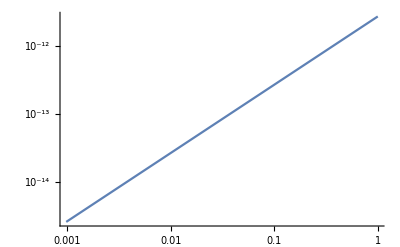

```mathematica
LogLogPlot[nD0[fDt,mSMtot],{fDt,0,1}]
```

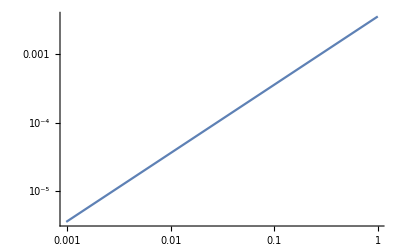

```mathematica
LogLogPlot[nD0[fDt,mSMtot]/aR^3,{fDt,0,1}]
```

```mathematica
ρcritbaumanneV
```

0.01

#### Neff correct way

```mathematica
gstar=2 (TDRt/TR)^4(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7(11/4)^(4/3)gstar (*[]*)
constraint = 0.1 (*[]constraint on ΔNeff*)
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] (*[eV]upper bound on TD at recombination*)
```

349.703 TDRt^4

1539.81 TDRt^4

0.1

0.0897704

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

1.66481×10^25

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

2.07738×10^16

```mathematica
Clear[Ωb]
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
(*nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)*)
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD
nDR[fD_,mDMtot_] := 1/aR^3 nD0[fD,mDMtot]
```

1000500000

0.00270135

```mathematica
n0
```

1.97516×10^-21

```mathematica
ContourPlot[Log10[nD0[10^fDt,10^mDM]],{fDt,-4,0},{mDM,Log10[10^-3 me],Log10[10^4 me]},ContourLabels->True,FrameLabel->{"f_D","m_(D, tot)"}]
```

-Graphics-

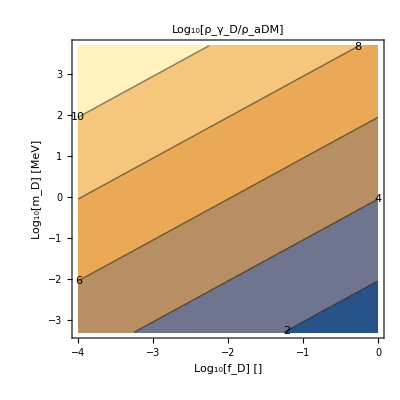

```mathematica
ContourPlot[Log10[π^2/45 TDRconst^3/nDR[10^fDt,10^(mDM+6)]],{fDt,-4,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"},PlotLabel->"Log_10[ρ_γ_D/ρ_aDM]"]
```

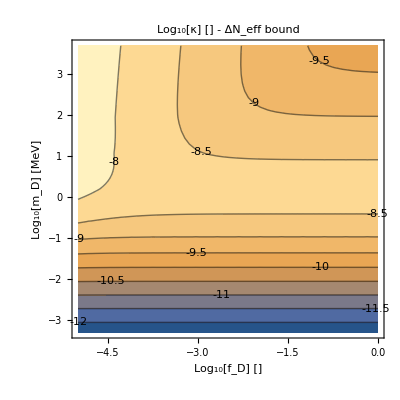

```mathematica
ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtottest[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]
```

```mathematica
Tdt
```

0.00025

### Corrected after n0 issue x 2

#### Constants and thermo dynamics

```mathematica
Tdt
```

0.00025

Temperature at decoupling

```mathematica
Td = 5 10^5; (*[eV] annihilation temperature*)
ad =(2 10^9)^-1; (*[] scale factor (~1/z) at annihilation*)
Tdt = N[Td ad] (*[eV] \tilde{T}_d the projected / extrapolated electron bath temperature today - if recombination / reionization etc. never happened*)
aR = (1100)^-1;(*[] scale factor ~ 1/z at recombination*)
TR = Tdt/aR (*[eV] temperature at recombination*)
```

0.00025

0.275

density today (and at decoupling)

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
eVm = N[200 10^-15 10^6] (*[eV m] = 1 follows from 1 = 200 MeV fm*)
```

0.67

4.9379×10^-6

4.9379

2.×10^-7

```mathematica
Clear[ne,n0]
n0 = Ωb ρcritbaumannm eVm^3 /.ΛCDMrepl (*[eV^3] number density today*)
ne[β_]:= n0(1/(β Tdt))^3
nd = n0 (Td/Tdt)^3
```

1.97516×10^-21

1.58013×10^7

```mathematica
ne[1/TR]
```

0.0006655

Thermal Quantities

```mathematica
me = 5 10^5; (*[eV] electron mass*)
pth =( (me Tdt)/(2 π))^(1/2); (*[eV] thermal de-broglie momentum*)
g = 4; (*[] dofs in SM electron*)
Z1[β_] := (g pth^3)/n0(1/(Tdt β))^(-3/2)(*[] whether classical is good or not*)
kF = N[(3 π^2 n0)^(1/3)] (*[eV] fermi momentum today*)
EF = kF^2/(2 me)
EFd = EF Td/Tdt (*[eV]fermi energy at decoupling*)
Degen = EF/Tdt (*Degeneracy of gas today - degeneracy is independent of time*)
```

3.88157×10^-7

1.50666×10^-19

3.01332×10^-10

6.02664×10^-16

```mathematica
LogLogPlot[Z1[β],{β,1/Td,1/TR},PlotLabel->"Z_1 []",AxesLabel->{"β [eV^-1]"}]
```

-Graphics-

```mathematica
Z1[1/me]
```

7.9367

Notice, fermi energy is about m/2. This is kinda interesting, numerology or dynamic?

fine structure constant

Debeye Cutoff

```mathematica
Λ[β_]:= 4 π α (2π n0)/(me Tdt)(1/(β Tdt))^2
```

```mathematica
1/Td Λ[1/Td]
1/Tdt Λ[1/Tdt]
10^-5/TR Λ[10^-5/TR]
```

0.0184425

9.22124×10^-12

0.00101434

```mathematica
1/Td
10^-5/TR
```

1/500000

0.0000363636

```mathematica
Plot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

-Graphics-

```mathematica
LogLogPlot[Λ[β],{β,1/Td,1/TR},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV]"}]
```

-Graphics-

#### compute hubble to convert to per a

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0inv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0= H0inv^-1 (*eV*) 
(*MP = (1.2 10^19 10^9)*)(*[eV] planck mass*)
```

1.51515×10^-33

```mathematica
N[200 10^-15 10^6]
```

2.×10^-7

```mathematica
ΛCDMrepl= {Ωk ->0.01,Ωr->9.4 10^-5, Ωm->0.32,ΩΛ->0.68,Ωb->0.05,Ωc->0.27}; (*[] ΛCDM density parameters*)
H[β_] :=H0(Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
aH[β_] :=a H0 (Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
```

```mathematica
LogLogPlot[aH[β],{β,1/Td,1/TR},PlotLabel->"ȧ [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

```mathematica
LogLogPlot[H[β],{β,1/Td,1/TR},PlotLabel->"H [eV]",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

#### Compare hubble and screening lengths - shows we can work in minkowski space

Screening energy - minimum energy transfered

```mathematica
LogPlot[Λ[β]/H[β],{β,1/Td,1/TR},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

Screening length (Debeye momentum) - minimum momentum transfered

```mathematica
LogLogPlot[(√(2 me Λ[β]))/H[β],{β,1/Td,1/TR},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

Temperature st. hubble is comparable to screening length

```mathematica
β/.Solve[(√(2 me Λ[β]))/H[β]==1,β][[3;;4]] (*[eV^-1]β*)
%^-1 (*[eV]photon temperatures*)
```

{1.22381×10^-27,1.53714×10^32}

{8.17118×10^26,6.50558×10^-33}

#### Numerically integrate, interpolate, numerically integrate

```mathematica
Clear[m,ESMt,Integrand]
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett]
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]]

(*Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) % /.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt})]*)
(*Integrand[mDt_,mt_,κ_,βt_,ESMt_]:=Simplify[2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{β->βt,m->mt,mD->mDt})]
NumIntegrand[mDt_,mt_,κ_,βt_,ESM_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.{β->βt,m->mt,mD->mDt}/.ESMt->ESM)*)
```

Ett^2/2-2 Ett (ESMt-ms+Λ)+(Λ (2 ESMt^2+2 ms^2+2 ESMt Λ-2 ms Λ+Λ^2))/(Ett+Λ)+(2 ESMt^2+2 ms^2+4 ESMt Λ-4 ms Λ+3 Λ^2) Log[Ett+Λ]

-2 ESMt^2-((m^2+mD^2)^2)/(2 mD^2)+(2 mD^2)/((-1+(ESMt+mD)^2/(ESMt^2-m^2))^2)+(2 (ESMt^2-m^2) (m^2+mD (-2 ESMt+mD-2 Λ)))/(m^2+mD (2 ESMt+mD))-2 ESMt Λ+((m^2+mD^2) Λ)/mD-Λ^2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/((2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ)-(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ]+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ]

```mathematica
Clear[NumIntegrand]
(*NumIntegrand[mDt_,mt_,κ_,βt_,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[βt],Qt->Q}/.ESMt->1/β ξE + m/.{β->βt,m->mt,mD->mDt})*)
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ) tempintegrand /.μ->m + 1/β Log[Qt]/.{Λ->Λ[β],Qt->Q}/.ESMt->1/β ξE + m/.β->ξβ/TR/.{m->mt,mD->mDt})*)
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[β],Qt->Z1[β]}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[m/ξβ NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}](*extra factor comes from jacobian*)

NIntegrate[NumIntegrand[me,me,1,me 10/Td,ξE],{ξE,0,∞},AccuracyGoal->Infinity]
ESMIntegral[me,me,1,me 10/Td]
```

NIntegrate::inumr: The integrand NumIntegrand[500000,500000,1,10,ξE] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[NumIntegrand[me,me,1,(me 10)/Td,ξE],{ξE,0,∞},AccuracyGoal→∞]

NIntegrate::inumr: The integrand 50000 NumIntegrand[500000,500000,1,10,ξE] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[500000/10 NumIntegrand[500000,500000,1,10,ξE],{ξE,0,∞}]

Interpolate

```mathematica
(*InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Abs[ESMIntegral[mD,m,κ,Interξβs[[i]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
Interpolation[InterPoints]
]*) (*above is not log interpolated*)
InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,ΔEtransfered},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
ΔEtransfered = NIntegrate[Tdt 10^RateLogFnofβ[Log10[β m]],{β,1/Td,1/TR}];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ΔEtot"->ΔEtransfered,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]
inter1me=InterpolateEtransRate[me,me,1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1|>

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

m=mD

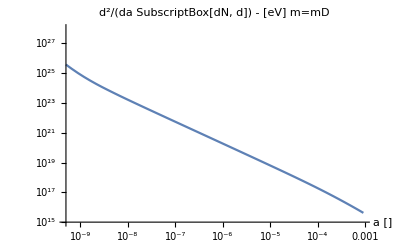

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

```mathematica
NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

2.07738×10^16

```mathematica
Tdt
```

0.00025

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

-Graphics-

mD = 2000 me

```mathematica
inter2000me=InterpolateEtransRate[2000 me,me,1]
```

<|f→InterpolatingFunction[…],ΔEtot→2.53409×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.359},{0.481511,26.6604},{0.963021,25.9637},{1.44453,25.2668},{1.92604,24.5691},{2.40755,23.8701},{2.88906,23.1698},{3.37057,22.4682},{3.85208,21.7643},{4.3336,21.0561},{4.81511,20.3373},{5.29662,19.5925},{5.77813,18.7975},{6.25964,17.9383}},mD→1000000000,m→500000,κ→1|>

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

-Graphics-

```mathematica
NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

2.53409×10^18

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

-Graphics-

#### Interpolate total energy transferred as a function of mass

```mathematica
InterpolateTotEtrans[mD_:{10^-3 me,10^4 me},m_:me,κ_:1]:=Module[{n=Round[Log10[mD[[2]]]-Log10[mD[[1]]]]+1,Interms,TableofInters,ΔEPoints,TotLogFnofm},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interms= N[Subdivide[Log10[mD[[2]]],Log10[mD[[1]]],n]]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TableofInters=Table[InterpolateEtransRate[10^Interms[[i]],m,κ],{i,Length[Interms]}];(*table of interpolations*)
ΔEPoints=Table[{Interms[[i]],Log10[TableofInters[[i]][["ΔEtot"]]]},{i,Length[Interms]}] ;(*Abs since numerical instability at early times*)
TotLogFnofm=Interpolation[ΔEPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->TotLogFnofm,"Inters"->TableofInters,"Points"->ΔEPoints,"Interms"->Interms,"mD"->mD,"m"->m,"κ"->κ|>
]
```

```mathematica
ΔEtottest =InterpolateTotEtrans[]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.000202728}. NIntegrate obtained 3.81137×10^16 and 1.0023×10^14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 1.08532×10^16 and 6.11752×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 6.43939×10^16 and 6.87998×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],Inters→{<|f→InterpolatingFunction[…],ΔEtot→1.15169×10^19,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,28.0117},{0.481511,27.3157},{0.963021,26.6215},{1.44453,25.9272},{1.92604,25.2316},{2.40755,24.5346},{2.88906,23.8362},{3.37057,23.1361},{3.85208,22.4337},{4.3336,21.7268},{4.81511,21.0092},{5.29662,20.2656},{5.77813,19.4716},{6.25964,18.6133}},mD→5.×10^9,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.72834×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.1939},{0.481511,26.4947},{0.963021,25.7974},{1.44453,25.1},{1.92604,24.4017},{2.40755,23.7023},{2.88906,23.0017},{3.37057,22.2996},{3.85208,21.5954},{4.3336,20.8869},{4.81511,20.1678},{5.29662,19.4228},{5.77813,18.6276},{6.25964,17.7681}},mD→6.66761×10^8,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→2.56094×10^17,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.3693},{0.481511,25.6677},{0.963021,24.9678},{1.44453,24.268},{1.92604,23.5675},{2.40755,22.8661},{2.88906,22.1636},{3.37057,21.4599},{3.85208,20.7542},{4.3336,20.0444},{4.81511,19.3239},{5.29662,18.5778},{5.77813,17.7814},{6.25964,16.921}},mD→8.8914×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.81137×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5544},{0.481511,24.8415},{0.963021,24.1378},{1.44453,23.4357},{1.92604,22.7333},{2.40755,22.0302},{2.88906,21.3262},{3.37057,20.6211},{3.85208,19.9141},{4.3336,19.2031},{4.81511,18.4816},{5.29662,17.7344},{5.77813,16.9371},{6.25964,16.0758}},mD→1.18569×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.08532×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.2071},{0.481511,24.2847},{0.963021,23.5196},{1.44453,22.7988},{1.92604,22.0898},{2.40755,21.3839},{2.88906,20.6783},{3.37057,19.972},{3.85208,19.2641},{4.3336,18.5522},{4.81511,17.83},{5.29662,17.0821},{5.77813,16.2841},{6.25964,15.4222}},mD→1.58114×10^6,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→6.43939×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.0221},{0.481511,25.0552},{0.963021,24.2712},{1.44453,23.5442},{1.92604,22.8331},{2.40755,22.1264},{2.88906,21.4206},{3.37057,20.7142},{3.85208,20.0062},{4.3336,19.2942},{4.81511,18.5718},{5.29662,17.8239},{5.77813,17.0259},{6.25964,16.1639}},mD→210848.,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→9.27351×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.9478},{0.481511,27.2274},{0.963021,26.522},{1.44453,25.8192},{1.92604,25.1165},{2.40755,24.4132},{2.88906,23.709},{3.37057,23.0037},{3.85208,22.2966},{4.3336,21.5854},{4.81511,20.8638},{5.29662,20.1165},{5.77813,19.3191},{6.25964,18.4577}},mD→28117.1,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.46411×10^21,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,30.5012},{0.481511,29.7991},{0.963021,29.0989},{1.44453,28.3988},{1.92604,27.6981},{2.40755,26.9964},{2.88906,26.2937},{3.37057,25.5898},{3.85208,24.8839},{4.3336,24.1738},{4.81511,23.4532},{5.29662,22.7069},{5.77813,21.9104},{6.25964,21.0498}},mD→3749.47,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.31667×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.0764},{0.481511,32.3769},{0.963021,31.6792},{1.44453,30.9814},{1.92604,30.2828},{2.40755,29.5831},{2.88906,28.8822},{3.37057,28.1798},{3.85208,27.4754},{4.3336,26.7667},{4.81511,26.0474},{5.29662,25.3022},{5.77813,24.5068},{6.25964,23.6472}},mD→500.,m→500000,κ→1|>},Points→{{9.69897,19.0613},{8.82397,18.2376},{7.94897,17.4084},{7.07397,16.5811},{6.19897,16.0356},{5.32397,16.8088},{4.44897,18.9672},{3.57397,21.5396},{2.69897,24.1195}},Interms→{9.69897,8.82397,7.94897,7.07397,6.19897,5.32397,4.44897,3.57397,2.69897},mD→{500,5000000000},m→500000,κ→1|>

```mathematica
Plot[ΔEtottest[["f"]][mD],{mD,Log10[10^-3 me],Log10[10^4 me]},PlotLabel->"Log_10[Energy Transfered to DS] [eV]",AxesLabel->{"Log_10[m_D] [eV]"}]
```

-Graphics-

#### Calculate ΔN_eff - my ham handed way

```mathematica
ΔEpD=0NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD=NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
TRSM = TR(*[eV]*)
TD =κ^2 2/3 (ΔEeD + ΔEpD)/1
gstar=2 (TD/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
Solve[ΔNeff==0.1,κ][[8]]
```

0.275

6.34425×10^23 κ^2

5.66528×10^97 κ^8

2.49454×10^98 κ^8

{κ→3.76163×10^-13}

#### Calculate ΔN_eff - v2

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
```

1.66481×10^25

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 9.51638×10^23 and 8.80941×10^19 for the integral and error estimates.

9.51638×10^23

```mathematica
TRSM = TR(*[eV]*)
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

0.275

```mathematica
N[Simplify[Solve[0==-nD Etot+ nD 3 TDn + π^2/15 TDn^4,TDn]]];
(TDn/.%)^4/.nD->1/.Etot->10^10
```

{1.51982×10^10-1600.89 ⅈ,1.51982×10^10+0.000019684 ⅈ,1.51982×10^10+0.000034447 ⅈ,1.51982×10^10+1600.89 ⅈ}

```mathematica
Plot[-nD Etot+ nD 3 TDn + π^2/15 TDn^4/.Etot->10^19/.nD->1 ,{TDn,0,70000},PlotRange->All]
```

-Graphics-

```mathematica
Clear[Findroot]
Findroot[f_,f0_:0,n_:20,ofmmin_:0,ofmmax_:10]:=Module[{xmin,interval,mid},
			(*This function finds the root of E(2R,κ) via binary search with a fixed number of iterations
			Input:
				ofmmin - the order of magnitude to initialize the search (f >= 10^offmin)
			  ofmmax - the maximum order of magnitude(f <= 10^offmax)
			  n - number of iterations
			  f0 - value being solved for

			Output:
					xmin - root of f
					fmin - the value of the function at the root to given precision
			*)

		interval={ofmmin,ofmmax};
		mid=0;
		 Do[mid = (interval[[2]]+interval[[1]])/2;
			interval =If[f[10^mid]-f0<0,{mid,interval[[2]]},{interval[[1]],mid}],
			{i,n}
		];
		xmin = N[10^mid];
			<|"root"->xmin,"f[root]"->N[fD[10^mid]],"frac rem"->N[(fD[10^mid]-f0)/f0]|>
	]
```

```mathematica
Clear[fD,f]
fD[T_,nD_:1]:=nD 3 T + π^2/15 T^4
(*Findroot[f[#,1],]*)
```

```mathematica
TDR[nD_,ED_]:=Findroot[fD[#,nD]&,nD ED][["root"]]
```

```mathematica
TDR[10^1,ΔEtot]
```

4.04406×10^6

```mathematica
InternDs= Subdivide[-15,0,15]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TDInterPoints=Table[{InternDs[[i]],Log10[Abs[TDR[10^InternDs[[i]],ΔEtot]]]},{i,Length[InternDs]}] (*Abs since numerical instability at early times*)
TDfnofnD=Interpolation[TDInterPoints]
```

{{-15,2.60682},{-14,2.85682},{-13,3.10683},{-12,3.35683},{-11,3.60682},{-10,3.85682},{-9,4.10682},{-8,4.35683},{-7,4.60683},{-6,4.85682},{-5,5.10682},{-4,5.35682},{-3,5.60683},{-2,5.85683},{-1,6.10682},{0,6.35682}}

InterpolatingFunction[…]

```mathematica
LogLogPlot[10^TDfnofnD[Log10[nDt]],{nDt,10^-15,1}]
```

-Graphics-

```mathematica
gstar=2 (TDR/TRSM)^4
ΔNeff = 8/7(11/4)^(4/3)gstar
constraint = 0.1
Solve[ΔNeff==constraint,κ]
Simplify[(κ/.%[[2]])^2 nD]
```

349.703 TDR^4

1539.81 TDR^4

0.1

{}

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

nD (κ/.{}⟦2⟧)^2

```mathematica
N[3/(8 π)]((1.2 10^19 10^9))^2
```

1.71887×10^55

```mathematica
κmin =PowerExpand[ κ/.Solve[c==κ^8 gs 8/7(11/4)^(4/3),κ][[4]]/.gs ->2( Tdark/TSM)^4]
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

(7^(1/8) c^(1/8) √TSM)/(22^(1/6) √Tdark)

-Graphics-

```mathematica
LogLogPlot[κmin/.{TSM->TRSM,Tdark->10^TDfnofnD[Log10[nDt]],c->constraint},{nDt,10^-15,1}]
```

-Graphics-

```mathematica
TDR[1,1]
```

1.00002

```mathematica
Solve[nD 3 TDn == π^2/15 TDn^4,nD]
```

{{nD→(π^2 TDn^3)/45}}

#### n0 check

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
```

0.67

4.9379×10^-6

4.9379

```mathematica
Ωb= 0.05 
ρb = Ωb ρcritbaumannm
```

0.05

0.246895

see https://arxiv.org/pdf/1303.5076.pdf 

so baumann agrees with WMAP, our previous calculation is okay

```mathematica
ρcritbaumanneV = n0/0.05 2000 me
```

0.01

```mathematica
ρcritbaumannm eVm^3/.eVm -> N[200 10^-15 10^6]
```

3.95032×10^-20

```mathematica
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
```

1000500000

0.00270135

```mathematica
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)
```

```mathematica
LogLogPlot[nD0[fDt,mSMtot],{fDt,0,1}]
```

-Graphics-

```mathematica
LogLogPlot[nD0[fDt,mSMtot]/aR^3,{fDt,0,1}]
```

-Graphics-

```mathematica
ρcritbaumanneV
```

0.01

#### Neff correct way

```mathematica
gstar=2 (TDRt/TR)^4(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7(11/4)^(4/3)gstar (*[]*)
constraint = 0.1 (*[]constraint on ΔNeff*)
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] (*[eV]upper bound on TD at recombination*)
```

349.703 TDRt^4

1539.81 TDRt^4

0.1

0.0897704

```mathematica
ΔEpD= NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,1/TR}] 
ΔEeD= NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR}]
(*TD =(15/π^2 nD κ^2  (ΔEeD + ΔEpD))^(1/4)*)
ΔEtot = (ΔEeD + ΔEpD);
```

1.66481×10^25

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

2.07738×10^16

```mathematica
Clear[Ωb]
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
(*nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD/(1-fD)*)
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD
nDR[fD_,mDMtot_] := 1/aR^3 nD0[fD,mDMtot]
```

1000500000

0.00270135

```mathematica
n0
```

1.97516×10^-21

```mathematica
ContourPlot[Log10[nD0[10^fDt,10^mDM]],{fDt,-4,0},{mDM,Log10[10^-3 me],Log10[10^4 me]},ContourLabels->True,FrameLabel->{"f_D","m_(D, tot)"}]
```

-Graphics-

```mathematica
ContourPlot[Log10[π^2/45 TDRconst^3/nDR[10^fDt,10^(mDM+6)]],{fDt,-4,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"},PlotLabel->"Log_10[ρ_γ_D/ρ_aDM]"]
```

-Graphics-

```mathematica
ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtottest[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]
```

-Graphics-

```mathematica
Tdt
```

0.00025

#### Private

Cosmo Constants - temperatures and scale factors

```mathematica
Td = 5 10^5; (*[eV] annihilation temperature*)
ad =(2 10^9)^-1; (*[] scale factor (~1/z) at annihilation*)
Tdt = 2.5 10^-4 (*[eV] Temperature of the Universe today*)
T0 = 2.5 10^-4 (*[eV] Temperature of the Universe today*)
aR = (1100)^-1;(*[] scale factor ~ 1/z at recombination*)
TR = Tdt/aR (*[eV] Temperature at recombination*)
```

0.00025

0.00025

0.275

Thermal Quantities

```mathematica
me = 5 10^5; (*[eV] electron mass*)
α=1/137;
pth =( (me Tdt)/(2 π))^(1/2); (*[eV] thermal de-broglie momentum*)
g = 4; (*[] dofs in SM electron*)
Z1[β_] := (g pth^3)/n0(1/(Tdt β))^(-3/2)(*[] single particle classical partition function*)
kF = N[(3 π^2 n0)^(1/3)] (*[eV] fermi momentum today*)
EF = kF^2/(2 me)
EFd = EF Td/Tdt (*[eV]fermi energy at decoupling*)
Degen = EF/Tdt (*Degeneracy of gas today - degeneracy is independent of time*)
```

3.09367 n0^(1/3)

9.57078×10^-6 n0^(2/3)

19141.6 n0^(2/3)

0.0382831 n0^(2/3)

Conversion

```mathematica
eVm = N[200 10^-15 10^6] (*[eV m] = 1 follows from 1 = 200 MeV fm*)
```

2.×10^-7

Hubble

```mathematica
H0tinv = 4.4 10^17; (*s*)
H0linv = 3 10^8 H0tinv; (*m*)
H0inv = (200 10^-15 10^6)^-1 H0linv; (*eV^-1*)
H0= H0inv^-1 (*eV*)
```

1.51515×10^-33

Critical density

```mathematica
h= 0.67 (*baumann 1.2.64*)
ρcritbaumanncm = 1.1 10^-5 h^2 (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  10^6 (*[protons m^-3]*)
```

0.67

4.9379×10^-6

4.9379

Define hubble and scale speed

```mathematica
ΛCDMrepl= {Ωk ->0.01,Ωr->9.4 10^-5, Ωm->0.32,ΩΛ->0.68,Ωb->0.05,Ωc->0.27}; (*[] ΛCDM density parameters*)
H[β_] :=H0(Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
aH[β_] :=a H0 (Ωr a^-4+Ωm a^-3+Ωk a^-2 + ΩΛ)^(1/2)/.ΛCDMrepl/.a->(Tdt β)
```

Number density today

```mathematica
n0 = Ωb ρcritbaumannm eVm^3 /.ΛCDMrepl  (*[eV^3] proton / electron number density today*)
ne[β_]:= n0(1/(β Tdt))^3 (*[eV^3] number density as a function of temperature*)
nd = n0 (Td/Tdt)^3 (*[eV^3] number density at decoupling*)
nr = n0 (Td/Tdt)^3 (*[eV^3] number density at decoupling*)
```

1.97516×10^-21

1.58013×10^7

1.58013×10^7

Debeye cutoff

```mathematica
Λ[β_]:= 4 π α (2π n0)/(me Tdt)(1/(β Tdt))^2
```

Determine interaction rate as a function of temperature

```mathematica
Integrate[Ett/(Ett+Λ)^2((ms + ESMt)^2+(ms+(Ett-ESMt))^2),Ett];
Simplify[%/.ms->(m^2+mD^2)/(2 mD)];
tempintegrand =Simplify[Simplify[(%/.Ett->(2 mD)/((ESMt+mD)^2/(ESMt^2-m^2)-1))-(%/.Ett->0)]];
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ]:=2/π(α^2 κ^2)/mDt (E^(-β ESMt + β μ)/aH[β] tempintegrand /.μ->m - 1/β Log[Qt]/.{Λ->Λ[β],Qt->Z1[β]}/.ESMt->1/β ξE + m/.β->ξβ/m/.{m->mt,mD->mDt})
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ]:=NIntegrate[m/ξβ NumIntegrand[mD,m,κ,ξβ,ξE],{ξE,0,∞}](*extra factor comes from jacobian*)
```

Interpolate over temperature, find total energy transfered to dark sector at recombination

```mathematica
InterpolateEtransRate[mD_,m_,κ_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,ΔEtransfered},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]]]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
ΔEtransfered = NIntegrate[Tdt 10^RateLogFnofβ[Log10[β me]],{β,1/Td,1/TR}];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ΔEtot"->ΔEtransfered,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]
```

Interpolate over a given mass range

```mathematica
InterpolateTotEtrans[mD_:{10^-3 me,10^4 me},m_:me,κ_:1]:=Module[{n=Round[Log10[mD[[2]]]-Log10[mD[[1]]]]+1,Interms,TableofInters,ΔEPoints,TotLogFnofm},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interms= N[Subdivide[Log10[mD[[2]]],Log10[mD[[1]]],n]]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TableofInters=Table[InterpolateEtransRate[10^Interms[[i]],m,κ],{i,Length[Interms]}];(*table of interpolations*)
ΔEPoints=Table[{Interms[[i]],Log10[TableofInters[[i]][["ΔEtot"]]]},{i,Length[Interms]}] ;(*Abs since numerical instability at early times*)
TotLogFnofm=Interpolation[ΔEPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->TotLogFnofm,"Inters"->TableofInters,"Points"->ΔEPoints,"Interms"->Interms,"mD"->mD,"m"->m,"κ"->κ|>
]
```

```mathematica
mSMtot= me + 2000 me
ρDM0= Ωc/Ωb n0 mSMtot/.ΛCDMrepl
nD0[fD_,mDMtot_] :=  ρDM0/mDMtot fD
nDR[fD_,mDMtot_] := 1/aR^3 nD0[fD,mDMtot]
```

1000500000

1.06712×10^-11

```mathematica
gstar=2 (TDRt/TR)^4(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7(11/4)^(4/3)gstar (*[]*)
constraint = 0.1 (*[]constraint on ΔNeff*)
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] (*[eV]upper bound on TD at recombination*)
```

349.703 TDRt^4

1539.81 TDRt^4

0.1

0.0897704

#### Plots

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

m=mD

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

-Graphics-

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

-Graphics-

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

-Graphics-

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

-Graphics-

```mathematica
ContourPlot[Log10[π^2/45 TDRconst^3/nDR[10^fDt,10^(mDM+6)]],{fDt,-4,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"},PlotLabel->"Log_10[ρ_γ_D/ρ_aDM]"]
```

-Graphics-

```mathematica
ΔEtottest =InterpolateTotEtrans[]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.000202728}. NIntegrate obtained 3.81137×10^16 and 1.0023×10^14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 1.08532×10^16 and 6.11752×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 6.43939×10^16 and 6.87998×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],Inters→{<|f→InterpolatingFunction[…],ΔEtot→1.15169×10^19,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,28.0117},{0.481511,27.3157},{0.963021,26.6215},{1.44453,25.9272},{1.92604,25.2316},{2.40755,24.5346},{2.88906,23.8362},{3.37057,23.1361},{3.85208,22.4337},{4.3336,21.7268},{4.81511,21.0092},{5.29662,20.2656},{5.77813,19.4716},{6.25964,18.6133}},mD→5.×10^9,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.72834×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.1939},{0.481511,26.4947},{0.963021,25.7974},{1.44453,25.1},{1.92604,24.4017},{2.40755,23.7023},{2.88906,23.0017},{3.37057,22.2996},{3.85208,21.5954},{4.3336,20.8869},{4.81511,20.1678},{5.29662,19.4228},{5.77813,18.6276},{6.25964,17.7681}},mD→6.66761×10^8,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→2.56094×10^17,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.3693},{0.481511,25.6677},{0.963021,24.9678},{1.44453,24.268},{1.92604,23.5675},{2.40755,22.8661},{2.88906,22.1636},{3.37057,21.4599},{3.85208,20.7542},{4.3336,20.0444},{4.81511,19.3239},{5.29662,18.5778},{5.77813,17.7814},{6.25964,16.921}},mD→8.8914×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.81137×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5544},{0.481511,24.8415},{0.963021,24.1378},{1.44453,23.4357},{1.92604,22.7333},{2.40755,22.0302},{2.88906,21.3262},{3.37057,20.6211},{3.85208,19.9141},{4.3336,19.2031},{4.81511,18.4816},{5.29662,17.7344},{5.77813,16.9371},{6.25964,16.0758}},mD→1.18569×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.08532×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.2071},{0.481511,24.2847},{0.963021,23.5196},{1.44453,22.7988},{1.92604,22.0898},{2.40755,21.3839},{2.88906,20.6783},{3.37057,19.972},{3.85208,19.2641},{4.3336,18.5522},{4.81511,17.83},{5.29662,17.0821},{5.77813,16.2841},{6.25964,15.4222}},mD→1.58114×10^6,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→6.43939×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.0221},{0.481511,25.0552},{0.963021,24.2712},{1.44453,23.5442},{1.92604,22.8331},{2.40755,22.1264},{2.88906,21.4206},{3.37057,20.7142},{3.85208,20.0062},{4.3336,19.2942},{4.81511,18.5718},{5.29662,17.8239},{5.77813,17.0259},{6.25964,16.1639}},mD→210848.,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→9.27351×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.9478},{0.481511,27.2274},{0.963021,26.522},{1.44453,25.8192},{1.92604,25.1165},{2.40755,24.4132},{2.88906,23.709},{3.37057,23.0037},{3.85208,22.2966},{4.3336,21.5854},{4.81511,20.8638},{5.29662,20.1165},{5.77813,19.3191},{6.25964,18.4577}},mD→28117.1,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.46411×10^21,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,30.5012},{0.481511,29.7991},{0.963021,29.0989},{1.44453,28.3988},{1.92604,27.6981},{2.40755,26.9964},{2.88906,26.2937},{3.37057,25.5898},{3.85208,24.8839},{4.3336,24.1738},{4.81511,23.4532},{5.29662,22.7069},{5.77813,21.9104},{6.25964,21.0498}},mD→3749.47,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.31667×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.0764},{0.481511,32.3769},{0.963021,31.6792},{1.44453,30.9814},{1.92604,30.2828},{2.40755,29.5831},{2.88906,28.8822},{3.37057,28.1798},{3.85208,27.4754},{4.3336,26.7667},{4.81511,26.0474},{5.29662,25.3022},{5.77813,24.5068},{6.25964,23.6472}},mD→500.,m→500000,κ→1|>},Points→{{9.69897,19.0613},{8.82397,18.2376},{7.94897,17.4084},{7.07397,16.5811},{6.19897,16.0356},{5.32397,16.8088},{4.44897,18.9672},{3.57397,21.5396},{2.69897,24.1195}},Interms→{9.69897,8.82397,7.94897,7.07397,6.19897,5.32397,4.44897,3.57397,2.69897},mD→{500,5000000000},m→500000,κ→1|>

```mathematica
ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtottest[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]
```

-Graphics-

```mathematica
nR
```

nR

```mathematica
?nDR
```

### Unit testing NeffConstraint package

```mathematica
"n0"/.CosmoParams[]
"nd"/.CosmoParams[]
"nr"/.CosmoParams[]
```

1.97516×10^-21

1.58013×10^7

2.62894×10^-12

```mathematica
"ρcrit"/.CosmoParams[]
```

3.95032×10^-20

```mathematica
"ΩΛ"/.ΛCDMrepl
```

0.68

```mathematica
NeffConstrain`Z1
```

NeffConstrain`Z1

```mathematica
Information[NeffConstrain`Z1]
```

```mathematica
aH::usage
```

ȧ as a function of temperature

```mathematica
?nD0
```

```mathematica
Integrate[Ett/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett];
Simplify[%/."ms"->("m"^2+"mD"^2)/(2 "mD")];
Integrand =Simplify[Simplify[(%/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(%/.Ett->0)]]
```

-2 ESMt^2-((m^2+mD^2)^2)/(2 mD^2)+(2 mD^2)/((-1+(ESMt+mD)^2/(ESMt^2-m^2))^2)+(2 (ESMt^2-m^2) (m^2+mD (-2 ESMt+mD-2 Λ)))/(m^2+mD (2 ESMt+mD))-2 ESMt Λ+((m^2+mD^2) Λ)/mD-Λ^2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/((2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ)-(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ]+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[(2 (ESMt^2-m^2) mD)/(m^2+mD (2 ESMt+mD))+Λ]

```mathematica
NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ,params_]:=2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"] Integrand /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params
ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ,params_]:=(m/.params)/ξβ NIntegrate[ NumIntegrand[mD,m,κ,ξβ,ξE,params],{ξE,0,∞}](*extra factor comes from jacobian*)
```

```mathematica
N[NumIntegrand["me","me",1,1,1]/.CosmoParams[]]
N[ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,1,CosmoParams[]]]
```

2.34565×10^19

3.8526×10^25

```mathematica
(*InterpolateEtransRate[mD_,m_,κ_,params_]:=Module[{n=13,Interξβs,InterPoints,RateLogFnofβ,ΔEtransfered,Td,TR,Tdt},

Td = "Td"/.params;
TR = "TR" /.params;
Tdt = "Tdt"/.params;

(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/Td],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
InterPoints=Table[{Interξβs[[i]],Log10[Abs[ESMIntegral[mD,m,κ,10^Interξβs[[i]],params]]]},{i,Length[Interξβs]}] ;(*Abs since numerical instability at early times*)
RateLogFnofβ=Interpolation[InterPoints];
ΔEtransfered = NIntegrate[Tdt 10^RateLogFnofβ[Log10[β m]],{β,1/Td,1/TR}];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->RateLogFnofβ,"ΔEtot"->ΔEtransfered,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ|>
]*)
```

```mathematica
(*InterpolateTotEtrans[mD_:{10^-3 ("me"/.CosmoParams[]),10^4 ("me"/.CosmoParams[])},m_:("me"/.CosmoParams[]),κ_:1,params_:CosmoParams[]]:=Module[{n=Round[Log10[mD[[2]]]-Log10[mD[[1]]]]+1,Interms,TableofInters,ΔEPoints,TotLogFnofm},
(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interms= N[Subdivide[Log10[mD[[2]]],Log10[mD[[1]]],n]]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
TableofInters=Table[InterpolateEtransRate[10^Interms[[i]],m,κ,params],{i,Length[Interms]}];(*table of interpolations*)
ΔEPoints=Table[{Interms[[i]],Log10[TableofInters[[i]][["ΔEtot"]]]},{i,Length[Interms]}] ;(*Abs since numerical instability at early times*)
TotLogFnofm=Interpolation[ΔEPoints];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->TotLogFnofm,"Inters"->TableofInters,"Points"->ΔEPoints,"Interms"->Interms,"mD"->mD,"m"->m,"κ"->κ|>
]*)
```

```mathematica
Interpolatetest[mD_:{10^-3 ("me"/.CosmoParams[]),10^4 ("me"/.CosmoParams[])},m_:("me"/.CosmoParams[]),κ_:1,params_:CosmoParams[]]:= Module[{},Print[mD,m,κ,params]]
```

```mathematica
Interpolatetest[]
```

{500,5000000000}5000001{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}

```mathematica
interpolatetest= InterpolateEtransRate["me"/.CosmoParams[],"me"/.CosmoParams[],1,CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1|>

```mathematica
Plot[interpolatetest[["f"]][β],{β,0,6.26}]
```

-Graphics-

```mathematica
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-3,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 3.81137×10^16 and 1.0023×10^14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.08532×10^16 and 6.11752×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 6.43939×10^16 and 6.87998×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

<|f→InterpolatingFunction[…],Inters→{<|f→InterpolatingFunction[…],ΔEtot→1.15169×10^19,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,28.0117},{0.481511,27.3157},{0.963021,26.6215},{1.44453,25.9272},{1.92604,25.2316},{2.40755,24.5346},{2.88906,23.8362},{3.37057,23.1361},{3.85208,22.4337},{4.3336,21.7268},{4.81511,21.0092},{5.29662,20.2656},{5.77813,19.4716},{6.25964,18.6133}},mD→5.×10^9,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.72834×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.1939},{0.481511,26.4947},{0.963021,25.7974},{1.44453,25.1},{1.92604,24.4017},{2.40755,23.7023},{2.88906,23.0017},{3.37057,22.2996},{3.85208,21.5954},{4.3336,20.8869},{4.81511,20.1678},{5.29662,19.4228},{5.77813,18.6276},{6.25964,17.7681}},mD→6.66761×10^8,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→2.56094×10^17,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.3693},{0.481511,25.6677},{0.963021,24.9678},{1.44453,24.268},{1.92604,23.5675},{2.40755,22.8661},{2.88906,22.1636},{3.37057,21.4599},{3.85208,20.7542},{4.3336,20.0444},{4.81511,19.3239},{5.29662,18.5778},{5.77813,17.7814},{6.25964,16.921}},mD→8.8914×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.81137×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5544},{0.481511,24.8415},{0.963021,24.1378},{1.44453,23.4357},{1.92604,22.7333},{2.40755,22.0302},{2.88906,21.3262},{3.37057,20.6211},{3.85208,19.9141},{4.3336,19.2031},{4.81511,18.4816},{5.29662,17.7344},{5.77813,16.9371},{6.25964,16.0758}},mD→1.18569×10^7,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.08532×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.2071},{0.481511,24.2847},{0.963021,23.5196},{1.44453,22.7988},{1.92604,22.0898},{2.40755,21.3839},{2.88906,20.6783},{3.37057,19.972},{3.85208,19.2641},{4.3336,18.5522},{4.81511,17.83},{5.29662,17.0821},{5.77813,16.2841},{6.25964,15.4222}},mD→1.58114×10^6,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→6.43939×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,26.0221},{0.481511,25.0552},{0.963021,24.2712},{1.44453,23.5442},{1.92604,22.8331},{2.40755,22.1264},{2.88906,21.4206},{3.37057,20.7142},{3.85208,20.0062},{4.3336,19.2942},{4.81511,18.5718},{5.29662,17.8239},{5.77813,17.0259},{6.25964,16.1639}},mD→210848.,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→9.27351×10^18,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,27.9478},{0.481511,27.2274},{0.963021,26.522},{1.44453,25.8192},{1.92604,25.1165},{2.40755,24.4132},{2.88906,23.709},{3.37057,23.0037},{3.85208,22.2966},{4.3336,21.5854},{4.81511,20.8638},{5.29662,20.1165},{5.77813,19.3191},{6.25964,18.4577}},mD→28117.1,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→3.46411×10^21,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,30.5012},{0.481511,29.7991},{0.963021,29.0989},{1.44453,28.3988},{1.92604,27.6981},{2.40755,26.9964},{2.88906,26.2937},{3.37057,25.5898},{3.85208,24.8839},{4.3336,24.1738},{4.81511,23.4532},{5.29662,22.7069},{5.77813,21.9104},{6.25964,21.0498}},mD→3749.47,m→500000,κ→1|>,<|f→InterpolatingFunction[…],ΔEtot→1.31667×10^24,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,33.0764},{0.481511,32.3769},{0.963021,31.6792},{1.44453,30.9814},{1.92604,30.2828},{2.40755,29.5831},{2.88906,28.8822},{3.37057,28.1798},{3.85208,27.4754},{4.3336,26.7667},{4.81511,26.0474},{5.29662,25.3022},{5.77813,24.5068},{6.25964,23.6472}},mD→500.,m→500000,κ→1|>},Points→{{9.69897,19.0613},{8.82397,18.2376},{7.94897,17.4084},{7.07397,16.5811},{6.19897,16.0356},{5.32397,16.8088},{4.44897,18.9672},{3.57397,21.5396},{2.69897,24.1195}},Interms→{9.69897,8.82397,7.94897,7.07397,6.19897,5.32397,4.44897,3.57397,2.69897},mD→{500,5000000000},m→500000,κ→1|>

```mathematica
(*ComputeΔNeffConstraint[ΔEtotDict_]:=Module[{gstar,ΔNeff,constraint,TDRconst},
gstar=2 (TDRt/"TR")^4/.ΔEtotDict[["params"]];(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7 (11/4)^(4/3) gstar; (*[]*)
constraint = 0.1; (*[]constraint on ΔNeff*)
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] ;(*[eV]upper bound on TD at recombination*)
Print[ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtotDict[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])/.ΔEtotDict[["params"]]],{fDt,-5,0},{mDM,Log10[ΔEtotDict[["mD"]][[1]]]-6,Log10[ΔEtotDict[["mD"]][[2]]]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]]
(*Print[ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtotDict[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]]*)
]*)
```

```mathematica
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-3,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
ComputeΔNeffConstraint[testΔEdict]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 3.81137×10^16 and 1.0023×10^14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.08532×10^16 and 6.11752×10^11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 6.43939×10^16 and 6.87998×10^12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

-Graphics-

-Graphics-

```mathematica
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
ComputeΔNeffConstraint[testΔEdict]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.72523×10^16 and 8.434×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.24981×10^16 and 1.72128×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.18099×10^17 and 1.94891×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
testΔEdict[["f"]][6+1]
```

16.5096

```mathematica
TDRconst = 0.09;
ΔEtotDict=testΔEdict;
Print[ContourPlot[1/2 Log10[(3TDRconst)/(10^ΔEtotDict[["f"]][6+mDM])(1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[ΔEtotDict[["mD"]][[1]]]-6,Log10[ΔEtotDict[["mD"]][[2]]]-6},ContourLabels->True,PlotLabel->"Log_10[κ] [] - ΔN_eff bound",FrameLabel->{"Log_10[f_D] []","Log_10[m_D] [MeV]"}]]
```

-Graphics-

```mathematica
1/2 Log10[(3TDRconst)/(10^ΔEtotDict[["f"]][6+1])(1+π^2/45 TDRconst^3/nDR[10^-3,10^(6+1)])]
```

Log[8.35238×10^-18 (1+(1.59888×10^6 aR^3)/ρDM0)]/(2 Log[10])

### Clean

#### Initialize

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in β near {β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

#### Plot hubble and aH

```mathematica
LogLogPlot[aH[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

-Graphics-

```mathematica
LogLogPlot[H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

-Graphics-

#### Screening length comparison and Expected rate scaling

Λ and 1/(Z_1 β ȧ) control the scaling of the rate

```mathematica
LogLogPlot[1/(Z1[β] aH[β]β)/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"a Dependent prefactor in rate []",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Λ[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Z1[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],10/("TR")/.CosmoParams[]},PlotLabel->"Z1 []",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

-Graphics-

-Graphics-

So it seems like partition function dominates over temperature scaling of a, and the reduced screening at late times.

```mathematica
Z1[1/("Td")]/.CosmoParams[]
```

2.00913×10^9

```mathematica
LogPlot[Λ[β]/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

Screening length (Debeye momentum) - minimum momentum transfered

```mathematica
LogPlot[(√(2 "me" Λ[β]))/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

#### Rate and Energy plots - SM aDM mass values

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

-Graphics-

m=mD

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

-Graphics-

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

-Graphics-

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

-Graphics-

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

-Graphics-

#### Neff constraint

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

-Graphics-

-Graphics-

-Graphics-

#### more scrap

```mathematica
Print["The rough temperature at which the dark photon bath can be populated is:"]
Tγ=10^7 GeV (gp/0.1)^2 ϵ/10^-8 
Print["Now solve for ϵ st the dark photon bath is populated at recombination"]
Solve[Tγ == TR,ϵ][[1]]
Print["Where TR is Recombination temperature gp is dark coupling. For gp=0.1 we have"]
%%/.{gp->0.1,TR ->0.25 10^-9 GeV}
```

The rough temperature at which the dark photon bath can be populated is:

1.×10^17 GeV gp^2 ϵ

Now solve for ϵ st the dark photon bath is populated at recombination

{ϵ→(1.×10^-17 TR)/(GeV gp^2)}

Where TR is Recombination temperature gp is dark coupling. For gp=0.1 we have

{ϵ→2.5×10^-25}